```mathematica
Clear["Global`*"]
```

#### Copying width data from 1811.03474 Fig. 3 left panel

```mathematica
SetDirectory[NotebookDirectory[]];
widthdata=Import["./constraints/decay\ width.csv","Data"]; (* from MIT paper, below is the full data *)
```

```mathematica
widthdata
```

{{0.0766077,0.00122477},{0.0849566,0.0020662},{0.0974512,0.00341789},{0.108024,0.00524628},{0.115148,0.00938441},{0.122561,0.0145476},{0.132481,0.0259004},{0.134473,0.0554863},{0.134521,0.0886491},{0.134562,0.132463},{0.134699,0.505229},{0.136616,0.00696664},{0.136985,0.258697},{0.138909,0.00381413},{0.141013,0.0116266},{0.150629,0.00223274},{0.152574,0.00106881},{0.154834,0.00216205},{0.163423,0.00352812},{0.172002,0.00528209},{0.182716,0.00727172},{0.200954,0.0121109},{0.22302,0.0199658},{0.238014,0.0265717},{0.253228,0.0349929},{0.28688,0.0604603},{0.317936,0.0931829},{0.351009,0.153619},{0.383507,0.250171},{0.417155,0.413268},{0.43874,0.669817},{0.461759,1.0637},{0.479032,1.62166},{0.499206,3.35755},{0.513628,6.32021},{0.525191,13.3554},{0.528105,20.3609},{0.541103,42.8789},{0.546434,81.9131},{0.547427,245.42},{0.547532,680.753},{0.547582,1110.88},{0.549832,400.487},{0.549845,148.868},{0.56551,42.4437},{0.571157,16.6593},{0.585436,7.7245},{0.616944,3.59386},{0.642769,2.99093},{0.685844,3.08389},{0.726061,3.61838},{0.760527,3.9261},{0.794992,4.20242},{0.832343,5.18883},{0.855373,9.18743},{0.874107,18.0147},{0.884251,45.123},{0.887072,27.6516},{0.892937,90.9172},{0.89874,163.184},{0.90454,285.033},{0.914783,618.921},{0.924394,1321.27},{0.929173,2590.74},{0.934719,6250.99},{0.942788,14528.7},{0.945522,595714.},{0.945896,310075.},{0.946347,25171.},{0.946601,933238.},{0.946651,1.5229×10^6},{0.946702,2.48513×10^6},{0.946752,4.05534×10^6},{0.946798,6.35305×10^6},{0.947329,142799.},{0.949091,46805.},{0.949139,74937.6},{0.963414,15980.2},{0.986716,7850.61},{1.03408,6423.39},{1.07144,8994.58},{1.1117,15604.3},{1.14478,27348.7},{1.17785,44628.8},{1.21522,65763.6},{1.2497,88706.6},{1.28993,117636.},{1.32442,150785.},{1.35889,175123.},{1.39336,203389.},{1.42784,236218.},{1.46231,270638.},{1.52262,297676.},{1.58293,318627.},{1.61739,322991.},{1.65184,318627.},{1.67194,316467.},{1.71357,292026.},{1.76094,256306.},{1.79539,239453.},{1.82984,217704.},{1.86142,214762.},{1.89588,214762.},{1.92746,208998.},{1.97916,227667.},{2.01362,230661.},{2.04807,230661.},{2.07679,228319.},{2.12274,247028.},{2.1572,250276.},{2.19166,255436.},{2.22611,246057.},{2.25771,263375.},{2.29217,274345.},{2.32375,274345.},{2.35821,274345.},{2.39267,274345.},{2.44437,297676.},{2.47882,294654.},{2.51328,297676.},{2.54487,297676.},{2.57454,301753.},{2.62241,322991.},{2.65687,327414.},{2.68845,319712.},{2.72291,322991.},{2.75736,319712.},{2.79182,322991.},{2.82342,354052.},{2.85788,357683.},{2.88659,350458.},{2.92105,345723.}}

```mathematica
width=widthdata;
width[[All,2]]=widthdata[[All,2]]/(32 Pi^2)^2/10^9; (* width is now in units of GeV for Subscript[f, a]=TeV *)
```

#### Various input params

```mathematica
mu=2.2/1000;
md=4.7/1000;
ms=20*md;
mc=1.275;
mb=4.18;
mt = 172.4;

mPi=135/1000;
mEta=0.548;
mEtap=0.958;

mK=497/1000;
Mz=91.1876;
Mz=91.18;
GammaZ=2.495;
Mw=80.379;

GF=1.166 10^(-5);
ThetawatMz = ArcSin[Sqrt[0.231]];
v=Sqrt[1/(Sqrt[2]GF)];

g2atMz=2 Mz Cos[ThetawatMz]/v;
gpatMz = g2atMz Tan[ThetawatMz];
g1atMz=Sqrt[5/3]gpatMz;
alpha1atMz = g1atMz^2/4/Pi;
alpha2atMz = g2atMz^2/4/Pi;

b1=41/10;
b2=-19/6;

alpha1[μ_]:=1/(1/alpha1atMz-b1/(2Pi)Log[μ/Mz]);
alpha2[μ_]:=1/(1/alpha2atMz-b2/(2Pi)Log[μ/Mz]);
alphaEM[mu_]:=3/5alpha1[mu]alpha2[mu]/(alpha2[mu]+3/5alpha1[mu]);

LambdaQCD=0.48;
Nf[μ_]:=4(*using 4 quark flavors*)
beta0[μ_]=11-2/3Nf[μ];
beta1[μ_] = 102-38/3Nf[μ];
z[mu_]:=-beta0[mu]^2/E/beta1[mu](LambdaQCD^2/mu^2)^(beta0[mu]^2/beta1[mu]);

alphas[μ_]:=-4Pi beta0[μ]/beta1[μ]/ProductLog[-1,z[μ]];(* using the expression in 1604.08082v3 eq. 3.21 *)
nflav=3;
EA=(97/4-7/6nflav);
KggNNLO[ma_,c3_,fa_]:=1+alphas[ma]/Pi EA+(alphas[ma]/Pi)^2EA(3/4 EA+(51/8-19/24nflav)/(11/4-nflav/6));
KggNLO[ma_]:=1+alphas[ma]/Pi EA;
GammaaglugluNLO[ma_,c3_,fa_]:=1/(32Pi^3)alphas[ma]^2ma^3/fa^2c3^2KggNLO[ma];
GammaaglugluNNLO[ma_,c3_,fa_]:=1/(32Pi^3)alphas[ma]^2ma^3/fa^2c3^2KggNNLO[ma,c3,fa];
(*This is in GeV*)
LifetimeinmmNLO[ma_,c3_,fa_]:=1/GammaaglugluNLO[ma,c3,fa]*0.198*10^(-12);(*this is in mm*)
LifetimeinmmNNLO[ma_,c3_,fa_]:=1/GammaaglugluNNLO[ma,c3,fa]*0.198*10^(-12);(*this is in mm*)
```

#### Details of mixing

```mathematica
c2=1;c1=1;
c3=1;
cgamma[ma_]:=2c3((4+mu/md)/(3+3mu/md)-1/2*ma^2/(ma^2-mPi^2)*(1-mu/md)/(1+mu/md));
GammaPhoton[ma_,fa_]:=alphaEM[ma]^2/(256 Pi^3)cgamma[ma]^2 ma^3/fa^2;
LifetimePhoton[ma_,fa_]:=1/GammaPhoton[ma,fa]*0.198*10^(-15); (*in meter*)
fpi=0.093; (* differs from FASER value of fpi = 0.130 *)

(*mixingAPi[ma_,fa_]:=(1/6)ma^2/(ma^2-mPi^2)fpi/fa;
mixingAEta[ma_,fa_]:=(ma^2/Sqrt[6]-Sqrt[2/3] mPi^2/9)1/(ma^2-mEta^2)fpi/fa;
mixingAEtap[ma_,fa_]:=(ma^2/(2Sqrt[3])-4Sqrt[1/3] mPi^2/9)1/(ma^2-mEtap^2)fpi/fa;*)
mixingAPi[ma_,fa_]:=((1-mu/md)/(1+mu/md))fpi/(2fa)ma^2/(ma^2-mPi^2);
mixingAEta[ma_,fa_]:=(0.6)fpi/(2fa)ma^2/(ma^2-mEta^2);
mixingAEtap[ma_,fa_]:=(0.8)fpi/(2fa)ma^2/(ma^2-mEtap^2);

NPOT=1.47*10^22;
Naxions[ma_,fa_,seleff_]:=NPOT*(2.89*mixingAPi[ma,fa]^2+0.33*mixingAEta[ma,fa]^2+0.03*mixingAEtap[ma,fa]^2)*seleff;
```

```mathematica
LifetimePhoton[0.1,1/(4 Pi^2)]//ScientificForm
```

2.9241×10^-9

#### Numerical width function and comparison with a > γγ

InterpolatingFunction::dmval: Input value {0.015061} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

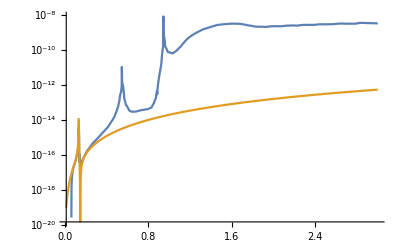

```mathematica
WidthFunc=Interpolation[width,InterpolationOrder->1];
LogPlot[{WidthFunc[ma],GammaPhoton[ma,1000]},{ma,0.015,3}]
```

#### Width function for f_a=1 TeV

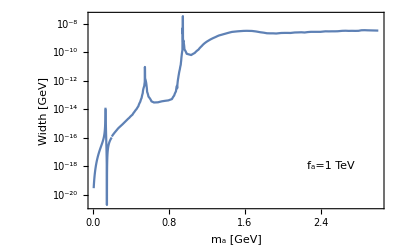

```mathematica
WidthFinal[ma_]:=Piecewise[{{GammaPhoton[ma,1000],ma≤0.2},{WidthFunc[ma],ma>0.2}}];

LifetimeFinal[ma_]:=1/WidthFinal[ma]*0.198*10^(-15); (*in meter*);

LogPlot[WidthFinal[ma],{ma,10^-2,3},Frame->True,FrameLabel->{"m_a [GeV]","Width [GeV]"},Epilog->Inset[Framed["f_a=1 TeV"],{2.5,Log[10^-18]}]]
```

```mathematica
(WidthFunc[0.19]-GammaPhoton[0.19,1000])/GammaPhoton[0.19,1000]
```

0.115838

#### Lifetime calculation

```mathematica
LifetimeFinal[0.4] 1/((1000*4 Pi^2)^2)
```

3.83866×10^-11

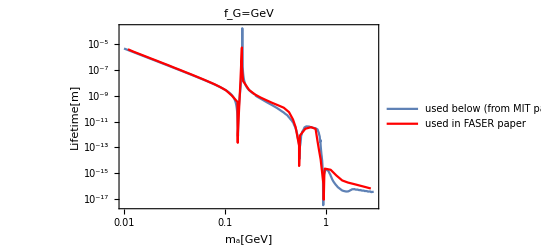

```mathematica
lifetimeFASER=Import["./constraints/lifetime-faser.csv","Data"]; 
lifetimeFASER[[All,2]]=lifetimeFASER[[All,2]]/10^9; 
Show[LogLogPlot[LifetimeFinal[ma] 1/((1000*4 Pi^2)^2),{ma,0.01,3},FrameLabel-> {"m_a[GeV]","Lifetime[m]"},PlotLegends->{"used below (from MIT paper)"},PlotLabel->"f_G=GeV",Frame->True],ListLogLogPlot[lifetimeFASER,Joined-> True,PlotStyle->Red,PlotLegends->{"used in FASER paper"}]]
```

```mathematica
LifetimeFinal[0.05] 1/((1000*4 Pi^2)^2)
```

3.29657×10^-8

#### Importing Pythia data

```mathematica
(*pi0=Import["/Users/soubhik/Documents/pythia8244/examples/mesons-pn-1M.txt","Data"];*)
pi0=Import["/Users/soubhik/Documents/pythia8244/examples/mesons-pn-100K.txt","Data"];
(* I am not copying the simulation files, but here is the order of various quantities in pi0:
part.id(); part.px(); part.py(); part.pz(); part.e(); part.eta(); part.pT(); part.m()
*)
```

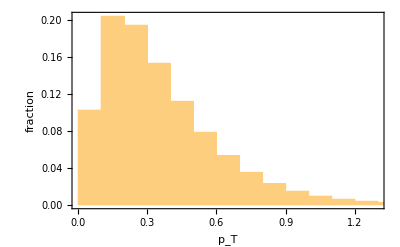

```mathematica
Histogram[pi0[[All,7]],{0.1},"Probability",Frame->True,FrameLabel->{"p_T","fraction"}]
```

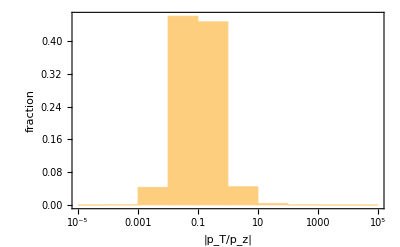

```mathematica
Histogram[Abs[pi0[[All,7]]/pi0[[All,4]]],(*{0.01},"Probability",*){"Log",10},"Probability",Frame-> True,FrameLabel->{"|p_T/p_z|","fraction"}]
```

#### Boost of pions

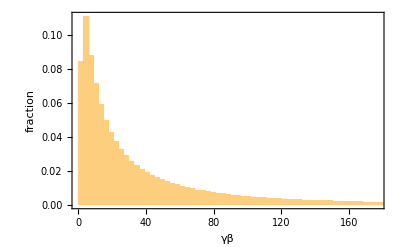

```mathematica
Histogram[Sqrt[pi0[[All,7]]^2+pi0[[All,4]]^2]/pi0[[All,8]],{3.0},"Probability",FrameLabel->{"γβ","fraction"},Frame->True]
```

#### Boost of axions, m_a=input

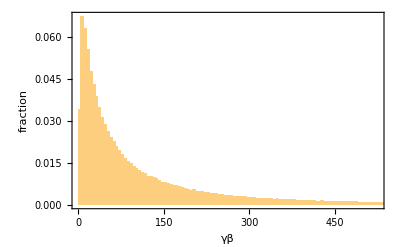

```mathematica
ma=0.05;
Histogram[Sqrt[pi0[[All,7]]^2+pi0[[All,4]]^2]/ma,{5.0},"Probability",FrameLabel->{"γβ","fraction"},Frame->True]
```

#### Energy distribution of axions at ND, m_a= input

```mathematica
ma=0.05;
enlist={};
dist=579; (* distance in m to HPTPC *)
length=5; (* decay length in m of HPTPC *)
radius=2.5; (* radius in m of HPTPC *)
For[i=1,i<Length[pi0]+1,i++,
If[Abs[(pi0[[i]][[7]])/(pi0[[i]][[4]])]<radius/dist ,AppendTo[enlist,pi0[[i]][[5]]],Continue]];
```

```mathematica
Length[enlist]/Length[pi0]//N
```

0.0102782

```mathematica
Naxions[0.05,1/(4 Pi^2),Length[enlist]/Length[pi0]]
```

4.8868×10^18

```mathematica
NPOT*2.89(**mixingAPi[0.05,1/(4 Pi^2)]^2*)
```

4.2483×10^22

```mathematica
NPOT*2.89*Length[enlist]/Length[pi0]*mixingAPi[0.05,1/(4 Pi^2)]^2
```

5.07749×10^18

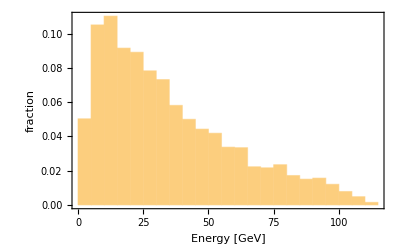

```mathematica
Histogram[enlist,{5.0},"Probability",FrameLabel->{"Energy [GeV]","fraction"},Frame->True]
```

```mathematica
Histogram[enlist,{1.0},NPOT*2.49*mixingAPi[0.05,1/(4 Pi^2)]^2/Length[pi0]#2&,Frame->True,FrameLabel->{"Energy [GeV]","N_a"}]
```

-Graphics-

#### Main code

```mathematica
dist=574; (* distance in m to HPTPC *)
length=10; (* decay length in m of HPTPC *)
radius=2.5; (* radius in m of HPTPC *)
lifetime=Table[10^x,{x,-3,6,1/3}];
masslist=Flatten[{Table[0.01+y*0.01,{y,0,11,1}],Table[0.12+y*0.001,{y,1,50,1}],Table[0.17+y*0.03,{y,1,7,1}],Table[0.40+y*0.01,{y,1,30,1}],Table[0.70+y*0.05,{y,1,2,1}]}];
axions={};
For[nn=1,nn<Length[masslist]+1,nn++,ma=masslist[[nn]];
For[j=1,j<Length[lifetime]+1,j++,
(*fa=(alphaEM[ma]cgamma[ma])/Sqrt[256 Pi^3] ma^(3/2)Sqrt[lifetime[[j]]/(0.198*10^(-15))];*)
fa=Sqrt[lifetime[[j]]/LifetimeFinal[ma]]*1000;
decayprob={};
list={};
For[i=1,i<Length[pi0]+1,i++,gabeta=Sqrt[(pi0[[i]][[7]])^2+(pi0[[i]][[4]])^2]/ma;
If[Abs[(pi0[[i]][[7]])/(pi0[[i]][[4]])]<radius/dist ,AppendTo[decayprob,Exp[-dist/(gabeta*lifetime[[j]])]-Exp[-(dist+length)/(gabeta*lifetime[[j]])]],Continue]];

AppendTo[axions,{ma,fa,Sum[decayprob[[i]],{i,Length[decayprob]}]*Naxions[ma,fa,Length[decayprob]/Length[pi0]]/Length[decayprob],lifetime[[j]]}]]]
```

General::munfl: Exp[-6264.07] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6373.2] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2942.75] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
(alphaEM[ma]cgamma[ma])/Sqrt[256 Pi^3] ma^(3/2)Sqrt[lifetime/(0.198*10^(-15))]
```

{11.8705,17.4236,25.5743,37.5379,55.0981,80.873,118.705,174.236,255.743,375.379,550.981,808.73,1187.05,1742.36,2557.43,3753.79,5509.81,8087.3,11870.5,17423.6,25574.3,37537.9,55098.1,80873.,118705.,174236.,255743.,375379.}

```mathematica
Sqrt[lifetime/LifetimeFinal[ma]]*1000
```

{11.8705,17.4236,25.5743,37.5379,55.0981,80.873,118.705,174.236,255.743,375.379,550.981,808.73,1187.05,1742.36,2557.43,3753.79,5509.81,8087.3,11870.5,17423.6,25574.3,37537.9,55098.1,80873.,118705.,174236.,255743.,375379.}

#### Produce plots

```mathematica
falistmin={};
falistmax={};
(*masslist={0.41000000000000003,0.42000000000000004,0.43000000000000005,0.44,0.45,0.46,0.47000000000000003,0.48000000000000004,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.5700000000000001,0.5800000000000001,0.5900000000000001,0.6000000000000001,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09};*)
For[nn=1,nn<Length[masslist]+1,nn++,mass=masslist[[nn]];
falist={};
For[i=1,i<Length[axions]+1,i++,If[axions[[i]][[1]]== mass,AppendTo[falist,{axions[[i]][[2]],axions[[i]][[3]]}],Continue]];
pts={};
pts=Graphics`Mesh`FindIntersections@Show[ListLogLogPlot[{falist},PlotStyle-> Red, Mesh-> All,Joined->True],LogLogPlot[10,{fa,0.1,10^8}]];
AppendTo[falistmin,{mass,1/(4 Pi^2 Exp[pts[[1,1]]])}];
AppendTo[falistmax,{mass,1/(4 Pi^2 Exp[pts[[2,1]]])}]]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 2 of {{3.66637,2.30259}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
pts
```

{{13.2003,2.30259},{16.3085,2.30259}}

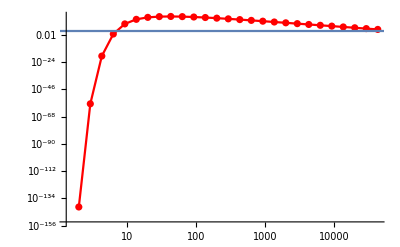

```mathematica
Show[ListLogLogPlot[{falist},PlotStyle-> Red, Mesh-> All,Joined->True],LogLogPlot[10,{fa,0.1,10^8}]]
```

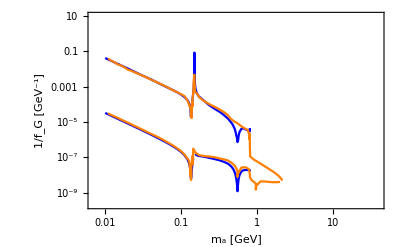

```mathematica
faprimemin=Import["./constraints/faprimemin.csv","Data"];
faprimemax=Import["./constraints/faprimemax.csv","Data"];
faexisting=Import["./constraints/existing.csv","Data"];
ListLogLogPlot[{falistmin,falistmax,faprimemin,faprimemax(*,faexisting*)},PlotStyle-> {Blue,Blue,Orange,Orange,Gray},Frame->True,Joined->True,(*Mesh->Full,*)FrameLabel->{"m_a [GeV]","1/f_G [GeV^-1]"},ImageSize->400]
```

## Final lists:

```mathematica
axionfinallist=axions;
```

```mathematica
axionfinallist
```

{{0.01,0.381396,1.49505×10^-12,1/1000},{0.01,0.559813,0.915458,1/(100 10^(2/3))},{0.01,0.821694,220413.,1/(100 10^(1/3))},{0.01,1.20608,5.37579×10^7,1/100},{0.01,1.77029,5.14262×10^8,1/(10 10^(2/3))},{0.01,2.59842,1.05637×10^9,1/(10 10^(1/3))},{0.01,3.81396,9.83188×10^8,1/10},{0.01,5.59813,5.7441×10^8,1/10^(2/3)},{0.01,8.21694,2.45637×10^8,1/10^(1/3)},{0.01,12.0608,8.37526×10^7,1},{0.01,17.7029,2.43026×10^7,10^(1/3)},{0.01,25.9842,6.29178×10^6,10^(2/3)},{0.01,38.1396,1.51059×10^6,10},{0.01,55.9813,346129.,10 10^(1/3)},{0.01,82.1694,77072.8,10 10^(2/3)},{0.01,120.608,16883.2,100},{0.01,177.029,3666.78,100 10^(1/3)},{0.01,259.842,793.002,100 10^(2/3)},{0.01,381.396,171.153,1000},{0.01,559.813,36.9045,1000 10^(1/3)},{0.01,821.694,7.95392,1000 10^(2/3)},{0.01,1206.08,1.71393,10000},{0.01,1770.29,0.369286,10000 10^(1/3)},{0.01,2598.42,0.0795632,10000 10^(2/3)},{0.01,3813.96,0.0171417,100000},{0.01,5598.13,0.0036931,100000 10^(1/3)},{0.01,8216.94,0.000795656,100000 10^(2/3)},{0.01,12060.8,0.000171419,1000000},{0.02,1.08528,1.04299×10^-34,1/1000},{0.02,1.59297,5.84425×10^-11,1/(100 10^(2/3))},{0.02,2.33816,4.98003,1/(100 10^(1/3))},{0.02,3.43195,478615.,1/100},{0.02,5.03741,7.58355×10^7,1/(10 10^(2/3))},{0.02,7.39391,5.9232×10^8,1/(10 10^(1/3))},{0.02,10.8528,1.10143×10^9,1/10},{0.02,15.9297,9.69702×10^8,1/10^(2/3)},{0.02,23.3816,5.46951×10^8,1/10^(1/3)},{0.02,34.3195,2.28056×10^8,1},{0.02,50.3741,7.63579×10^7,10^(1/3)},{0.02,73.9391,2.18728×10^7,10^(2/3)},{0.02,108.528,5.61253×10^6,10},{0.02,159.297,1.34002×10^6,10 10^(1/3)},{0.02,233.816,305989.,10 10^(2/3)},{0.02,343.195,67995.6,100},{0.02,503.741,14878.3,100 10^(1/3)},{0.02,739.391,3229.55,100 10^(2/3)},{0.02,1085.28,698.256,1000},{0.02,1592.97,150.685,1000 10^(1/3)},{0.02,2338.16,32.4892,1000 10^(2/3)},{0.02,3431.95,7.0021,10000},{0.02,5037.41,1.50881,10000 10^(1/3)},{0.02,7393.91,0.325088,10000 10^(2/3)},{0.02,10852.8,0.0700407,100000},{0.02,15929.7,0.0150901,100000 10^(1/3)},{0.02,23381.6,0.00325108,100000 10^(2/3)},{0.02,34319.5,0.000700426,1000000},{0.03,2.00779,6.21033×10^-57,1/1000},{0.03,2.94704,3.29746×10^-21,1/(100 10^(2/3))},{0.03,4.32566,0.0000992766,1/(100 10^(1/3))},{0.03,6.3492,3614.72,1/100},{0.03,9.31935,9.27699×10^6,1/(10 10^(2/3))},{0.03,13.6789,2.68025×10^8,1/(10 10^(1/3))},{0.03,20.0779,9.37071×10^8,1/10},{0.03,29.4704,1.16054×10^9,1/10^(2/3)},{0.03,43.2566,8.0751×10^8,1/10^(1/3)},{0.03,63.492,3.90188×10^8,1},{0.03,93.1935,1.45369×10^8,10^(1/3)},{0.03,136.789,4.49192×10^7,10^(2/3)},{0.03,200.779,1.21541×10^7,10},{0.03,294.704,3.00166×10^6,10 10^(1/3)},{0.03,432.566,699890.,10 10^(2/3)},{0.03,634.92,157500.,100},{0.03,931.935,34703.9,100 10^(1/3)},{0.03,1367.89,7559.78,100 10^(2/3)},{0.03,2007.79,1637.32,1000},{0.03,2947.04,353.625,1000 10^(1/3)},{0.03,4325.66,76.2746,1000 10^(2/3)},{0.03,6349.2,16.4417,10000},{0.03,9319.35,3.54315,10000 10^(1/3)},{0.03,13678.9,0.763438,10000 10^(2/3)},{0.03,20077.9,0.164487,100000},{0.03,29470.4,0.0354385,100000 10^(1/3)},{0.03,43256.6,0.00763507,100000 10^(2/3)},{0.03,63492.,0.00164494,1000000},{0.04,3.11934,3.49683×10^-79,1/1000},{0.04,4.57857,1.77485×10^-31,1/(100 10^(2/3))},{0.04,6.72042,1.91174×10^-9,1/(100 10^(1/3))},{0.04,9.86422,26.1162,1/100},{0.04,14.4787,1.06924×10^6,1/(10 10^(2/3))},{0.04,21.2518,1.13469×10^8,1/(10 10^(1/3))},{0.04,31.1934,7.33899×10^8,1/10},{0.04,45.7857,1.24292×10^9,1/10^(2/3)},{0.04,67.2042,1.03789×10^9,1/10^(1/3)},{0.04,98.6422,5.65897×10^8,1},{0.04,144.787,2.30238×10^8,10^(1/3)},{0.04,212.518,7.57457×10^7,10^(2/3)},{0.04,311.934,2.14282×10^7,10},{0.04,457.857,5.45169×10^6,10 10^(1/3)},{0.04,672.042,1.29472×10^6,10 10^(2/3)},{0.04,986.422,294675.,100},{0.04,1447.87,65354.7,100 10^(1/3)},{0.04,2125.18,14285.6,100 10^(2/3)},{0.04,3119.34,3099.28,1000},{0.04,4578.57,669.924,1000 10^(1/3)},{0.04,6720.42,144.553,1000 10^(2/3)},{0.04,9864.22,31.1655,10000},{0.04,14478.7,6.71665,10000 10^(1/3)},{0.04,21251.8,1.44728,10000 10^(2/3)},{0.04,31193.4,0.31183,100000},{0.04,45785.7,0.067184,100000 10^(1/3)},{0.04,67204.2,0.0144746,100000 10^(2/3)},{0.04,98642.2,0.00311848,1000000},{0.05,4.41173,1.93131×10^-101,1/1000},{0.05,6.47554,9.3839×10^-42,1/(100 10^(2/3))},{0.05,9.50479,3.64744×10^-14,1/(100 10^(1/3))},{0.05,13.9511,0.186943,1/100},{0.05,20.4774,120950.,1/(10 10^(2/3))},{0.05,30.0568,4.69201×10^7,1/(10 10^(1/3))},{0.05,44.1173,5.58196×10^8,1/10},{0.05,64.7554,1.27502×10^9,1/10^(2/3)},{0.05,95.0479,1.25815×10^9,1/10^(1/3)},{0.05,139.511,7.62409×10^8,1},{0.05,204.774,3.34636×10^8,10^(1/3)},{0.05,300.568,1.16262×10^8,10^(2/3)},{0.05,441.173,3.41888×10^7,10},{0.05,647.554,8.93367×10^6,10 10^(1/3)},{0.05,950.479,2.15744×10^6,10 10^(2/3)},{0.05,1395.11,496134.,100},{0.05,2047.74,110714.,100 10^(1/3)},{0.05,3005.68,24281.1,100 10^(2/3)},{0.05,4411.73,5276.62,1000},{0.05,6475.54,1141.49,1000 10^(1/3)},{0.05,9504.79,246.4,1000 10^(2/3)},{0.05,13951.1,53.1329,10000},{0.05,20477.4,11.4519,10000 10^(1/3)},{0.05,30056.8,2.46772,10000 10^(2/3)},{0.05,44117.3,0.531702,100000},{0.05,64755.4,0.114556,100000 10^(1/3)},{0.05,95047.9,0.0246809,100000 10^(2/3)},{0.05,139511.,0.00531739,1000000},{0.06,5.89185,1.06524×10^-123,1/1000},{0.06,8.64806,4.95759×10^-52,1/(100 10^(2/3))},{0.06,12.6936,6.98655×10^-19,1/(100 10^(1/3))},{0.06,18.6317,0.00134688,1/100},{0.06,27.3476,13698.6,1/(10 10^(2/3))},{0.06,40.1407,1.93451×10^7,1/(10 10^(1/3))},{0.06,58.9185,4.22189×10^8,1/10},{0.06,86.4806,1.29127×10^9,1/10^(2/3)},{0.06,126.936,1.49071×10^9,1/10^(1/3)},{0.06,186.317,9.94427×10^8,1},{0.06,273.476,4.66824×10^8,10^(1/3)},{0.06,401.407,1.70297×10^8,10^(2/3)},{0.06,589.185,5.18417×10^7,10},{0.06,864.806,1.38797×10^7,10 10^(1/3)},{0.06,1269.36,3.40437×10^6,10 10^(2/3)},{0.06,1863.17,790431.,100},{0.06,2734.76,177415.,100 10^(1/3)},{0.06,4014.07,39035.,100 10^(2/3)},{0.06,5891.85,8496.85,1000},{0.06,8648.06,1839.59,1000 10^(1/3)},{0.06,12693.6,397.242,1000 10^(2/3)},{0.06,18631.7,85.6754,10000},{0.06,27347.6,18.4674,10000 10^(1/3)},{0.06,40140.7,3.97962,10000 10^(2/3)},{0.06,58918.5,0.857475,100000},{0.06,86480.6,0.184747,100000 10^(1/3)},{0.06,126936.,0.0398034,100000 10^(2/3)},{0.06,186317.,0.00857547,1000000},{0.07,7.5841,5.93864×10^-146,1/1000},{0.07,11.1319,2.65004×10^-62,1/(100 10^(2/3))},{0.07,16.3395,1.35719×10^-23,1/(100 10^(1/3))},{0.07,23.983,9.87×10^-6,1/100},{0.07,35.2023,1573.85,1/(10 10^(2/3))},{0.07,51.6699,8.06214×10^6,1/(10 10^(1/3))},{0.07,75.841,3.2225×10^8,1/10},{0.07,111.319,1.31439×10^9,1/10^(2/3)},{0.07,163.395,1.76313×10^9,1/10^(1/3)},{0.07,239.83,1.28628×10^9,1},{0.07,352.023,6.41732×10^8,10^(1/3)},{0.07,516.699,2.44734×10^8,10^(2/3)},{0.07,758.41,7.68871×10^7,10},{0.07,1113.19,2.10499×10^7,10 10^(1/3)},{0.07,1633.95,5.23898×10^6,10 10^(2/3)},{0.07,2398.3,1.2274×10^6,100},{0.07,3520.23,277017.,100 10^(1/3)},{0.07,5166.99,61140.3,100 10^(2/3)},{0.07,7584.1,13330.1,1000},{0.07,11131.9,2888.31,1000 10^(1/3)},{0.07,16339.5,623.939,1000 10^(2/3)},{0.07,23983.,134.592,10000},{0.07,35202.3,29.014,10000 10^(1/3)},{0.07,51669.9,6.25257,10000 10^(2/3)},{0.07,75841.,1.34725,100000},{0.07,111319.,0.290272,100000 10^(1/3)},{0.07,163395.,0.062539,100000 10^(2/3)},{0.07,239830.,0.0134738,1000000},{0.08,9.54096,3.3832×10^-168,1/1000},{0.08,14.0042,1.44975×10^-72,1/(100 10^(2/3))},{0.08,20.5554,2.70102×10^-28,1/(100 10^(1/3))},{0.08,30.1712,7.42928×10^-8,1/100},{0.08,44.2852,185.529,1/(10 10^(2/3))},{0.08,65.0018,3.43725×10^6,1/(10 10^(1/3))},{0.08,95.4096,2.51321×10^8,1/10},{0.08,140.042,1.36377×10^9,1/10^(2/3)},{0.08,205.554,2.11531×10^9,1/10^(1/3)},{0.08,301.712,1.67958×10^9,1},{0.08,442.852,8.86281×10^8,10^(1/3)},{0.08,650.018,3.52109×10^8,10^(2/3)},{0.08,954.096,1.13888×10^8,10},{0.08,1400.42,3.18318×10^7,10 10^(1/3)},{0.08,2055.54,8.03257×10^6,10 10^(2/3)},{0.08,3017.12,1.898×10^6,100},{0.08,4428.52,430628.,100 10^(1/3)},{0.08,6500.18,95332.5,100 10^(2/3)},{0.08,9540.96,20818.1,1000},{0.08,14004.2,4514.32,1000 10^(1/3)},{0.08,20555.4,975.564,1000 10^(2/3)},{0.08,30171.2,210.48,10000},{0.08,44285.2,45.3768,10000 10^(1/3)},{0.08,65001.8,9.77918,10000 10^(2/3)},{0.08,95409.6,2.10716,100000},{0.08,140042.,0.454005,100000 10^(1/3)},{0.08,205554.,0.0978155,100000 10^(2/3)},{0.08,301712.,0.021074,1000000},{0.09,11.8705,1.99489×10^-190,1/1000},{0.09,17.4236,8.22305×10^-83,1/(100 10^(2/3))},{0.09,25.5743,5.57568×10^-33,1/(100 10^(1/3))},{0.09,37.5379,5.81281×10^-10,1/100},{0.09,55.0981,22.728,1/(10 10^(2/3))},{0.09,80.873,1.51934×10^6,1/(10 10^(1/3))},{0.09,118.705,2.02994×10^8,1/10},{0.09,174.236,1.46328×10^9,1/10^(2/3)},{0.09,255.743,2.61525×10^9,1/10^(1/3)},{0.09,375.379,2.25159×10^9,1},{0.09,550.981,1.25199×10^9,10^(1/3)},{0.09,808.73,5.16677×10^8,10^(2/3)},{0.09,1187.05,1.7172×10^8,10},{0.09,1742.36,4.89319×10^7,10 10^(1/3)},{0.09,2557.43,1.25107×10^7,10 10^(2/3)},{0.09,3753.79,2.98031×10^6,100},{0.09,5509.81,679599.,100 10^(1/3)},{0.09,8087.3,150894.,100 10^(2/3)},{0.09,11870.5,33003.,1000},{0.09,17423.6,7162.18,1000 10^(1/3)},{0.09,25574.3,1548.36,1000 10^(2/3)},{0.09,37537.9,334.122,10000},{0.09,55098.1,72.0384,10000 10^(1/3)},{0.09,80873.,15.5256,10000 10^(2/3)},{0.09,118705.,3.34543,100000},{0.09,174236.,0.720806,100000 10^(1/3)},{0.09,255743.,0.155298,100000 10^(2/3)},{0.09,375379.,0.0334586,1000000},{0.1,14.813,1.23924×10^-212,1/1000},{0.1,21.7426,4.92221×10^-93,1/(100 10^(2/3))},{0.1,31.9137,1.21486×10^-37,1/(100 10^(1/3))},{0.1,46.843,4.8085×10^-12,1/100},{0.1,68.7561,2.94438,1/(10 10^(2/3))},{0.1,100.92,708913.,1/(10 10^(1/3))},{0.1,148.13,1.72901×10^8,1/10},{0.1,217.426,1.65402×10^9,1/10^(2/3)},{0.1,319.137,3.39758×10^9,1/10^(1/3)},{0.1,468.43,3.16222×10^9,1},{0.1,687.561,1.84747×10^9,10^(1/3)},{0.1,1009.2,7.90041×10^8,10^(2/3)},{0.1,1481.3,2.69373×10^8,10},{0.1,2174.26,7.81644×10^7,10 10^(1/3)},{0.1,3191.37,2.02362×10^7,10 10^(2/3)},{0.1,4684.3,4.85849×10^6,100},{0.1,6875.61,1.11325×10^6,100 10^(1/3)},{0.1,10092.,247889.,100 10^(2/3)},{0.1,14813.,54301.4,1000},{0.1,21742.6,11793.4,1000 10^(1/3)},{0.1,31913.7,2550.53,1000 10^(2/3)},{0.1,46843.,550.477,10000},{0.1,68756.1,118.696,10000 10^(1/3)},{0.1,100920.,25.5821,10000 10^(2/3)},{0.1,148130.,5.51249,100000},{0.1,217426.,1.18773,100000 10^(1/3)},{0.1,319137.,0.255899,100000 10^(2/3)},{0.1,468430.,0.0551327,1000000},{0.11,19.0025,8.34257×10^-235,1/1000},{0.11,27.8918,3.19794×10^-103,1/(100 10^(2/3))},{0.11,40.9396,2.87331×10^-42,1/(100 10^(1/3))},{0.11,60.0911,4.3232×10^-14,1/100},{0.11,88.2016,0.414767,1/(10 10^(2/3))},{0.11,129.462,359175.,1/(10 10^(1/3))},{0.11,190.025,1.59764×10^8,1/10},{0.11,278.918,2.02682×10^9,1/10^(2/3)},{0.11,409.396,4.77605×10^9,1/10^(1/3)},{0.11,600.911,4.79369×10^9,1},{0.11,882.016,2.93565×10^9,10^(1/3)},{0.11,1294.62,1.29817×10^9,10^(2/3)},{0.11,1900.25,4.53463×10^8,10},{0.11,2789.18,1.33861×10^8,10 10^(1/3)},{0.11,4093.96,3.50721×10^7,10 10^(2/3)},{0.11,6009.11,8.4841×10^6,100},{0.11,8820.16,1.95308×10^6,100 10^(1/3)},{0.11,12946.2,436110.,100 10^(2/3)},{0.11,19002.5,95678.1,1000},{0.11,27891.8,20795.9,1000 10^(1/3)},{0.11,40939.6,4499.14,1000 10^(2/3)},{0.11,60091.1,971.216,10000},{0.11,88201.6,209.434,10000 10^(1/3)},{0.11,129462.,45.1404,10000 10^(2/3)},{0.11,190025.,9.72714,100000},{0.11,278918.,2.09584,100000 10^(1/3)},{0.11,409396.,0.451554,100000 10^(2/3)},{0.11,600911.,0.0972864,1000000},{0.12,26.7757,6.41227×10^-257,1/1000},{0.12,39.3014,2.37532×10^-113,1/(100 10^(2/3))},{0.12,57.6865,7.77017×10^-47,1/(100 10^(1/3))},{0.12,84.6722,4.44832×10^-16,1/100},{0.12,124.282,0.0669063,1/(10 10^(2/3))},{0.12,182.421,208172.,1/(10 10^(1/3))},{0.12,267.757,1.68725×10^8,1/10},{0.12,393.014,2.83717×10^9,1/10^(2/3)},{0.12,576.865,7.65847×10^9,1/10^(1/3)},{0.12,846.722,8.27248×10^9,1},{0.12,1242.82,5.30002×10^9,10^(1/3)},{0.12,1824.21,2.41929×10^9,10^(2/3)},{0.12,2677.57,8.64745×10^8,10},{0.12,3930.14,2.59469×10^8,10 10^(1/3)},{0.12,5768.65,6.87641×10^7,10 10^(2/3)},{0.12,8467.22,1.6756×10^7,100},{0.12,12428.2,3.87473×10^6,100 10^(1/3)},{0.12,18242.1,867556.,100 10^(2/3)},{0.12,26775.7,190619.,1000},{0.12,39301.4,41463.3,1000 10^(1/3)},{0.12,57686.5,8973.82,1000 10^(2/3)},{0.12,84672.2,1937.5,10000},{0.12,124282.,417.838,10000 10^(1/3)},{0.12,182421.,90.0624,10000 10^(2/3)},{0.12,267757.,19.4075,100000},{0.12,393014.,4.18165,100000 10^(1/3)},{0.12,576865.,0.900951,100000 10^(2/3)},{0.12,846722.,0.194108,1000000},{0.121,28.0397,3.98353×10^-259,1/1000},{0.121,41.1566,2.33088×10^-114,1/(100 10^(2/3))},{0.121,60.4096,2.74379×10^-47,1/(100 10^(1/3))},{0.121,88.6692,2.84556×10^-16,1/100},{0.121,130.149,0.0563614,1/(10 10^(2/3))},{0.121,191.032,199279.,1/(10 10^(1/3))},{0.121,280.397,1.71498×10^8,1/10},{0.121,411.566,2.96613×10^9,1/10^(2/3)},{0.121,604.096,8.11558×10^9,1/10^(1/3)},{0.121,886.692,8.82997×10^9,1},{0.121,1301.49,5.68226×10^9,10^(1/3)},{0.121,1910.32,2.60178×10^9,10^(2/3)},{0.121,2803.97,9.32063×10^8,10},{0.121,4115.66,2.80112×10^8,10 10^(1/3)},{0.121,6040.96,7.4318×10^7,10 10^(2/3)},{0.121,8866.92,1.81223×10^7,100},{0.121,13014.9,4.19253×10^6,100 10^(1/3)},{0.121,19103.2,938965.,100 10^(2/3)},{0.121,28039.7,206340.,1000},{0.121,41156.6,44886.3,1000 10^(1/3)},{0.121,60409.6,9715.02,1000 10^(2/3)},{0.121,88669.2,2097.56,10000},{0.121,130149.,452.361,10000 10^(1/3)},{0.121,191032.,97.504,10000 10^(2/3)},{0.121,280397.,21.0112,100000},{0.121,411566.,4.52718,100000 10^(1/3)},{0.121,604096.,0.975397,100000 10^(2/3)},{0.121,886692.,0.210147,1000000},{0.122,29.4731,2.48098×10^-261,1/1000},{0.122,43.2606,2.29309×10^-115,1/(100 10^(2/3))},{0.122,63.4979,9.71352×10^-48,1/(100 10^(1/3))},{0.122,93.2022,1.82494×10^-16,1/100},{0.122,136.802,0.0476,1/(10 10^(2/3))},{0.122,200.798,191254.,1/(10 10^(1/3))},{0.122,294.731,1.74759×10^8,1/10},{0.122,432.606,3.10883×10^9,1/10^(2/3)},{0.122,634.979,8.62174×10^9,1/10^(1/3)},{0.122,932.022,9.44874×10^9,1},{0.122,1368.02,6.10729×10^9,10^(1/3)},{0.122,2007.98,2.80499×10^9,10^(2/3)},{0.122,2947.31,1.0071×10^9,10},{0.122,4326.06,3.03144×10^8,10 10^(1/3)},{0.122,6349.79,8.05181×10^7,10 10^(2/3)},{0.122,9320.22,1.96483×10^7,100},{0.122,13680.2,4.54755×10^6,100 10^(1/3)},{0.122,20079.8,1.01875×10^6,100 10^(2/3)},{0.122,29473.1,223906.,1000},{0.122,43260.6,48711.2,1000 10^(1/3)},{0.122,63497.9,10543.3,1000 10^(2/3)},{0.122,93202.2,2276.43,10000},{0.122,136802.,490.94,10000 10^(1/3)},{0.122,200798.,105.82,10000 10^(2/3)},{0.122,294731.,22.8032,100000},{0.122,432606.,4.9133,100000 10^(1/3)},{0.122,634979.,1.05859,100000 10^(2/3)},{0.122,932022.,0.228071,1000000},{0.123,31.1183,1.5494×10^-263,1/1000},{0.123,45.6754,2.2621×10^-116,1/(100 10^(2/3))},{0.123,67.0423,3.4482×10^-48,1/(100 10^(1/3))},{0.123,98.4046,1.1736×10^-16,1/100},{0.123,144.438,0.0403114,1/(10 10^(2/3))},{0.123,212.006,184056.,1/(10 10^(1/3))},{0.123,311.183,1.78571×10^8,1/10},{0.123,456.754,3.26732×10^9,1/10^(2/3)},{0.123,670.423,9.18444×10^9,1/10^(1/3)},{0.123,984.046,1.01383×10^10,1},{0.123,1444.38,6.58179×10^9,10^(1/3)},{0.123,2120.06,3.03217×10^9,10^(2/3)},{0.123,3111.83,1.09109×10^9,10},{0.123,4567.54,3.28942×10^8,10 10^(1/3)},{0.123,6704.23,8.74673×10^7,10 10^(2/3)},{0.123,9840.46,2.13592×10^7,100},{0.123,14443.8,4.94573×10^6,100 10^(1/3)},{0.123,21200.6,1.10824×10^6,100 10^(2/3)},{0.123,31118.3,243612.,1000},{0.123,45675.4,53002.3,1000 10^(1/3)},{0.123,67042.3,11472.5,1000 10^(2/3)},{0.123,98404.6,2477.1,10000},{0.123,144438.,534.221,10000 10^(1/3)},{0.123,212006.,115.149,10000 10^(2/3)},{0.123,311183.,24.8137,100000},{0.123,456754.,5.34649,100000 10^(1/3)},{0.123,670423.,1.15192,100000 10^(2/3)},{0.123,984046.,0.24818,1000000},{0.124,33.0327,9.70472×10^-266,1/1000},{0.124,48.4853,2.23813×10^-117,1/(100 10^(2/3))},{0.124,71.1667,1.2277×10^-48,1/(100 10^(1/3))},{0.124,104.458,7.56973×10^-17,1/100},{0.124,153.324,0.0342403,1/(10 10^(2/3))},{0.124,225.049,177654.,1/(10 10^(1/3))},{0.124,330.327,1.83006×10^8,1/10},{0.124,484.853,3.44403×10^9,1/10^(2/3)},{0.124,711.667,9.81266×10^9,1/10^(1/3)},{0.124,1044.58,1.09099×10^10,1},{0.124,1533.24,7.11382×10^9,10^(1/3)},{0.124,2250.49,3.28725×10^9,10^(2/3)},{0.124,3303.27,1.1855×10^9,10},{0.124,4848.53,3.57963×10^8,10 10^(1/3)},{0.124,7116.67,9.52895×10^7,10 10^(2/3)},{0.124,10445.8,2.32859×10^7,100},{0.124,15332.4,5.39421×10^6,100 10^(1/3)},{0.124,22504.9,1.20906×10^6,100 10^(2/3)},{0.124,33032.7,265813.,1000},{0.124,48485.3,57837.,1000 10^(1/3)},{0.124,71166.7,12519.4,1000 10^(2/3)},{0.124,104458.,2703.2,10000},{0.124,153324.,582.988,10000 10^(1/3)},{0.124,225049.,125.661,10000 10^(2/3)},{0.124,330327.,27.079,100000},{0.124,484853.,5.83459,100000 10^(1/3)},{0.124,711667.,1.25708,100000 10^(2/3)},{0.124,1.04458×10^6,0.270837,1000000},{0.125,35.2968,6.09799×10^-268,1/1000},{0.125,51.8087,2.22151×10^-118,1/(100 10^(2/3))},{0.125,76.0447,4.3851×10^-49,1/(100 10^(1/3))},{0.125,111.618,4.89814×10^-17,1/100},{0.125,163.833,0.0291771,1/(10 10^(2/3))},{0.125,240.474,172026.,1/(10 10^(1/3))},{0.125,352.968,1.88151×10^8,1/10},{0.125,518.087,3.6419×10^9,1/10^(2/3)},{0.125,760.447,1.05173×10^10,1/10^(1/3)},{0.125,1116.18,1.17776×10^10,1},{0.125,1638.33,7.71313×10^9,10^(1/3)},{0.125,2404.74,3.57499×10^9,10^(2/3)},{0.125,3529.68,1.2921×10^9,10},{0.125,5180.87,3.90763×10^8,10 10^(1/3)},{0.125,7604.47,1.04135×10^8,10 10^(2/3)},{0.125,11161.8,2.54656×10^7,100},{0.125,16383.3,5.90171×10^6,100 10^(1/3)},{0.125,24047.4,1.32316×10^6,100 10^(2/3)},{0.125,35296.8,290942.,1000},{0.125,51808.7,63309.4,1000 10^(1/3)},{0.125,76044.7,13704.5,1000 10^(2/3)},{0.125,111618.,2959.13,10000},{0.125,163833.,638.19,10000 10^(1/3)},{0.125,240474.,137.56,10000 10^(2/3)},{0.125,352968.,29.6432,100000},{0.125,518087.,6.38709,100000 10^(1/3)},{0.125,760447.,1.37612,100000 10^(2/3)},{0.125,1.11618×10^6,0.296484,1000000},{0.126,38.0272,3.84498×10^-270,1/1000},{0.126,55.8162,2.21268×10^-119,1/(100 10^(2/3))},{0.126,81.927,1.57173×10^-49,1/(100 10^(1/3))},{0.126,120.252,3.18049×10^-17,1/100},{0.126,176.506,0.0249494,1/(10 10^(2/3))},{0.126,259.076,167156.,1/(10 10^(1/3))},{0.126,380.272,1.94114×10^8,1/10},{0.126,558.162,3.86453×10^9,1/10^(2/3)},{0.126,819.27,1.13116×10^10,1/10^(1/3)},{0.126,1202.52,1.27581×10^10,1},{0.126,1765.06,8.39165×10^9,10^(1/3)},{0.126,2590.76,3.90121×10^9,10^(2/3)},{0.126,3802.72,1.4131×10^9,10},{0.126,5581.62,4.2802×10^8,10 10^(1/3)},{0.126,8192.7,1.14189×10^8,10 10^(2/3)},{0.126,12025.2,2.79438×10^7,100},{0.126,17650.6,6.47888×10^6,100 10^(1/3)},{0.126,25907.6,1.45295×10^6,100 10^(2/3)},{0.126,38027.2,319527.,1000},{0.126,55816.2,69534.9,1000 10^(1/3)},{0.126,81927.,15052.7,1000 10^(2/3)},{0.126,120252.,3250.29,10000},{0.126,176506.,700.989,10000 10^(1/3)},{0.126,259076.,151.097,10000 10^(2/3)},{0.126,380272.,32.5603,100000},{0.126,558162.,7.01565,100000 10^(1/3)},{0.126,819270.,1.51155,100000 10^(2/3)},{0.126,1.20252×10^6,0.325661,1000000},{0.127,41.3982,2.43355×10^-272,1/1000},{0.127,60.7642,2.21224×10^-120,1/(100 10^(2/3))},{0.127,89.1897,5.65483×10^-50,1/(100 10^(1/3))},{0.127,130.913,2.07302×10^-17,1/100},{0.127,192.153,0.0214155,1/(10 10^(2/3))},{0.127,282.043,163042.,1/(10 10^(1/3))},{0.127,413.982,2.01025×10^8,1/10},{0.127,607.642,4.1163×10^9,1/10^(2/3)},{0.127,891.897,1.22118×10^10,1/10^(1/3)},{0.127,1309.13,1.38723×10^10,1},{0.127,1921.53,9.16408×10^9,10^(1/3)},{0.127,2820.43,4.2731×10^9,10^(2/3)},{0.127,4139.82,1.55119×10^9,10},{0.127,6076.42,4.70572×10^8,10 10^(1/3)},{0.127,8918.97,1.25678×10^8,10 10^(2/3)},{0.127,13091.3,3.07771×10^7,100},{0.127,19215.3,7.13888×10^6,100 10^(1/3)},{0.127,28204.3,1.60138×10^6,100 10^(2/3)},{0.127,41398.2,352222.,1000},{0.127,60764.2,76655.7,1000 10^(1/3)},{0.127,89189.7,16594.8,1000 10^(2/3)},{0.127,130913.,3583.34,10000},{0.127,192153.,772.824,10000 10^(1/3)},{0.127,282043.,166.582,10000 10^(2/3)},{0.127,413982.,35.8972,100000},{0.127,607642.,7.73464,100000 10^(1/3)},{0.127,891897.,1.66646,100000 10^(2/3)},{0.127,1.30913×10^6,0.359036,1000000},{0.128,45.6842,1.54661×10^-274,1/1000},{0.128,67.0553,2.22097×10^-121,1/(100 10^(2/3))},{0.128,98.4237,2.04296×10^-50,1/(100 10^(1/3))},{0.128,144.466,1.35679×10^-17,1/100},{0.128,212.047,0.0184587,1/(10 10^(2/3))},{0.128,311.243,159689.,1/(10 10^(1/3))},{0.128,456.842,2.09045×10^8,1/10},{0.128,670.553,4.40263×10^9,1/10^(2/3)},{0.128,984.237,1.32382×10^10,1/10^(1/3)},{0.128,1444.66,1.51459×10^10,1},{0.128,2120.47,1.00487×10^10,10^(1/3)},{0.128,3112.43,4.69958×10^9,10^(2/3)},{0.128,4568.42,1.70971×10^9,10},{0.128,6705.53,5.19462×10^8,10 10^(1/3)},{0.128,9842.37,1.38886×10^8,10 10^(2/3)},{0.128,14446.6,3.40355×10^7,100},{0.128,21204.7,7.89809×10^6,100 10^(1/3)},{0.128,31124.3,1.77216×10^6,100 10^(2/3)},{0.128,45684.2,389841.,1000},{0.128,67055.3,84849.4,1000 10^(1/3)},{0.128,98423.7,18369.2,1000 10^(2/3)},{0.128,144466.,3966.58,10000},{0.128,212047.,855.484,10000 10^(1/3)},{0.128,311243.,184.4,10000 10^(2/3)},{0.128,456842.,39.7369,100000},{0.128,670553.,8.56198,100000 10^(1/3)},{0.128,984237.,1.84471,100000 10^(2/3)},{0.128,1.44466×10^6,0.397441,1000000},{0.129,51.3424,9.87396×10^-277,1/1000},{0.129,75.3604,2.2399×10^-122,1/(100 10^(2/3))},{0.129,110.614,7.41438×10^-51,1/(100 10^(1/3))},{0.129,162.359,8.92071×10^-18,1/100},{0.129,238.311,0.0159827,1/(10 10^(2/3))},{0.129,349.792,157119.,1/(10 10^(1/3))},{0.129,513.424,2.18376×10^8,1/10},{0.129,753.604,4.73032×10^9,1/10^(2/3)},{0.129,1106.14,1.44161×10^10,1/10^(1/3)},{0.129,1623.59,1.66113×10^10,1},{0.129,2383.11,1.10684×10^10,10^(1/3)},{0.129,3497.92,5.19188×10^9,10^(2/3)},{0.129,5134.24,1.8929×10^9,10},{0.129,7536.04,5.76004×10^8,10 10^(1/3)},{0.129,11061.4,1.5417×10^8,10 10^(2/3)},{0.129,16235.9,3.78074×10^7,100},{0.129,23831.1,8.77717×10^6,100 10^(1/3)},{0.129,34979.2,1.96992×10^6,100 10^(2/3)},{0.129,51342.4,433409.,1000},{0.129,75360.4,94339.2,1000 10^(1/3)},{0.129,110614.,20424.5,1000 10^(2/3)},{0.129,162359.,4410.45,10000},{0.129,238311.,951.224,10000 10^(1/3)},{0.129,349792.,205.038,10000 10^(2/3)},{0.129,513424.,44.1843,100000},{0.129,753604.,9.52024,100000 10^(1/3)},{0.129,1.10614×10^6,2.05118,100000 10^(2/3)},{0.129,1.62359×10^6,0.441923,1000000},{0.13,59.1957,6.33543×10^-279,1/1000},{0.13,86.8874,2.27034×10^-123,1/(100 10^(2/3))},{0.13,127.533,2.70439×10^-51,1/(100 10^(1/3))},{0.13,187.193,5.89478×10^-18,1/100},{0.13,274.762,0.0139087,1/(10 10^(2/3))},{0.13,403.296,155369.,1/(10 10^(1/3))},{0.13,591.957,2.2927×10^8,1/10},{0.13,868.874,5.10794×10^9,1/10^(2/3)},{0.13,1275.33,1.57775×10^10,1/10^(1/3)},{0.13,1871.93,1.83096×10^10,1},{0.13,2747.62,1.22525×10^10,10^(1/3)},{0.13,4032.96,5.76429×10^9,10^(2/3)},{0.13,5919.57,2.10612×10^9,10},{0.13,8688.74,6.41865×10^8,10 10^(1/3)},{0.13,12753.3,1.71984×10^8,10 10^(2/3)},{0.13,18719.3,4.22053×10^7,100},{0.13,27476.2,9.80237×10^6,100 10^(1/3)},{0.13,40329.6,2.20059×10^6,100 10^(2/3)},{0.13,59195.7,484230.,1000},{0.13,86887.4,105409.,1000 10^(1/3)},{0.13,127533.,22822.,1000 10^(2/3)},{0.13,187193.,4928.27,10000},{0.13,274762.,1062.91,10000 10^(1/3)},{0.13,403296.,229.113,10000 10^(2/3)},{0.13,591957.,49.3725,100000},{0.13,868874.,10.6381,100000 10^(1/3)},{0.13,1.27533×10^6,2.29203,100000 10^(2/3)},{0.13,1.87193×10^6,0.493815,1000000},{0.131,70.8899,4.08764×10^-281,1/1000},{0.131,104.052,2.31403×10^-124,1/(100 10^(2/3))},{0.131,152.728,9.91927×10^-52,1/(100 10^(1/3))},{0.131,224.173,3.917×10^-18,1/100},{0.131,329.042,0.0121715,1/(10 10^(2/3))},{0.131,482.967,154497.,1/(10 10^(1/3))},{0.131,708.899,2.4205×10^8,1/10},{0.131,1040.52,5.54645×10^9,1/10^(2/3)},{0.131,1527.28,1.73635×10^10,1/10^(1/3)},{0.131,2241.73,2.02936×10^10,1},{0.131,3290.42,1.36383×10^10,10^(1/3)},{0.131,4829.67,6.43515×10^9,10^(2/3)},{0.131,7088.99,2.35629×10^9,10},{0.131,10405.2,7.19197×10^8,10 10^(1/3)},{0.131,15272.8,1.92912×10^8,10 10^(2/3)},{0.131,22417.3,4.73739×10^7,100},{0.131,32904.2,1.10075×10^7,100 10^(1/3)},{0.131,48296.7,2.47179×10^6,100 10^(2/3)},{0.131,70889.9,543987.,1000},{0.131,104052.,118426.,1000 10^(1/3)},{0.131,152728.,25641.3,1000 10^(2/3)},{0.131,224173.,5537.16,10000},{0.131,329042.,1194.25,10000 10^(1/3)},{0.131,482967.,257.423,10000 10^(2/3)},{0.131,708899.,55.4733,100000},{0.131,1.04052×10^6,11.9527,100000 10^(1/3)},{0.131,1.52728×10^6,2.57525,100000 10^(2/3)},{0.131,2.24173×10^6,0.554835,1000000},{0.132,90.265,2.65374×10^-283,1/1000},{0.132,132.491,2.37324×10^-125,1/(100 10^(2/3))},{0.132,194.47,3.66087×10^-52,1/(100 10^(1/3))},{0.132,285.443,2.619×10^-18,1/100},{0.132,418.973,0.0107176,1/(10 10^(2/3))},{0.132,614.969,154586.,1/(10 10^(1/3))},{0.132,902.65,2.57132×10^8,1/10},{0.132,1324.91,6.06004×10^9,1/10^(2/3)},{0.132,1944.7,1.92277×10^10,1/10^(1/3)},{0.132,2854.43,2.26319×10^10,1},{0.132,4189.73,1.52746×10^10,10^(1/3)},{0.132,6149.69,7.2284×10^9,10^(2/3)},{0.132,9026.5,2.65239×10^9,10},{0.132,13249.1,8.10803×10^8,10 10^(1/3)},{0.132,19447.,2.17716×10^8,10 10^(2/3)},{0.132,28544.3,5.35023×10^7,100},{0.132,41897.3,1.24368×10^7,100 10^(1/3)},{0.132,61496.9,2.79348×10^6,100 10^(2/3)},{0.132,90265.,614872.,1000},{0.132,132491.,133868.,1000 10^(1/3)},{0.132,194470.,28985.8,1000 10^(2/3)},{0.132,285443.,6259.51,10000},{0.132,418973.,1350.05,10000 10^(1/3)},{0.132,614969.,291.009,10000 10^(2/3)},{0.132,902650.,62.7109,100000},{0.132,1.32491×10^6,13.5121,100000 10^(1/3)},{0.132,1.9447×10^6,2.91125,100000 10^(2/3)},{0.132,2.85443×10^6,0.627225,1000000},{0.133,128.842,1.73485×10^-285,1/1000},{0.133,189.114,2.45095×10^-126,1/(100 10^(2/3))},{0.133,277.581,1.36054×10^-52,1/(100 10^(1/3))},{0.133,407.434,1.76336×10^-18,1/100},{0.133,598.031,0.00950342,1/(10 10^(2/3))},{0.133,877.789,155756.,1/(10 10^(1/3))},{0.133,1288.42,2.75061×10^8,1/10},{0.133,1891.14,6.6674×10^9,1/10^(2/3)},{0.133,2775.81,2.14404×10^10,1/10^(1/3)},{0.133,4074.34,2.54152×10^10,1},{0.133,5980.31,1.72261×10^10,10^(1/3)},{0.133,8777.89,8.1757×10^9,10^(2/3)},{0.133,12884.2,3.00638×10^9,10},{0.133,18911.4,9.20397×10^8,10 10^(1/3)},{0.133,27758.1,2.47408×10^8,10 10^(2/3)},{0.133,40743.4,6.08409×10^7,100},{0.133,59803.1,1.41487×10^7,100 10^(1/3)},{0.133,87778.9,3.17883×10^6,100 10^(2/3)},{0.133,128842.,699794.,1000},{0.133,189114.,152369.,1000 10^(1/3)},{0.133,277581.,32992.8,1000 10^(2/3)},{0.133,407434.,7124.96,10000},{0.133,598031.,1536.73,10000 10^(1/3)},{0.133,877789.,331.248,10000 10^(2/3)},{0.133,1.28842×10^6,71.3823,100000},{0.133,1.89114×10^6,15.3806,100000 10^(1/3)},{0.133,2.77581×10^6,3.31381,100000 10^(2/3)},{0.133,4.07434×10^6,0.713957,1000000},{0.134,244.223,1.14308×10^-287,1/1000},{0.134,358.47,2.55118×10^-127,1/(100 10^(2/3))},{0.134,526.163,5.09627×10^-53,1/(100 10^(1/3))},{0.134,772.301,1.19664×10^-18,1/100},{0.134,1133.58,0.0084934,1/(10 10^(2/3))},{0.134,1663.87,158175.,1/(10 10^(1/3))},{0.134,2442.23,2.96563×10^8,1/10},{0.134,3584.7,7.3935×10^9,1/10^(2/3)},{0.134,5261.63,2.40962×10^10,1/10^(1/3)},{0.134,7723.01,2.87653×10^10,1},{0.134,11335.8,1.95795×10^10,10^(1/3)},{0.134,16638.7,9.31966×10^9,10^(2/3)},{0.134,24422.3,3.4343×10^9,10},{0.134,35847.,1.05298×10^9,10 10^(1/3)},{0.134,52616.3,2.83348×10^8,10 10^(2/3)},{0.134,77230.1,6.97272×10^7,100},{0.134,113358.,1.62222×10^7,100 10^(1/3)},{0.134,166387.,3.64561×10^6,100 10^(2/3)},{0.134,244223.,802671.,1000},{0.134,358470.,174782.,1000 10^(1/3)},{0.134,526163.,37847.4,1000 10^(2/3)},{0.134,772301.,8173.47,10000},{0.134,1.13358×10^6,1762.88,10000 10^(1/3)},{0.134,1.66387×10^6,379.999,10000 10^(2/3)},{0.134,2.44223×10^6,81.8881,100000},{0.134,3.5847×10^6,17.6442,100000 10^(1/3)},{0.134,5.26163×10^6,3.80153,100000 10^(2/3)},{0.134,7.72301×10^6,0.819035,1000000},{0.135,ComplexInfinity,Indeterminate,1/1000},{0.135,ComplexInfinity,Indeterminate,1/(100 10^(2/3))},{0.135,ComplexInfinity,Indeterminate,1/(100 10^(1/3))},{0.135,ComplexInfinity,Indeterminate,1/100},{0.135,ComplexInfinity,Indeterminate,1/(10 10^(2/3))},{0.135,ComplexInfinity,Indeterminate,1/(10 10^(1/3))},{0.135,ComplexInfinity,Indeterminate,1/10},{0.135,ComplexInfinity,Indeterminate,1/10^(2/3)},{0.135,ComplexInfinity,Indeterminate,1/10^(1/3)},{0.135,ComplexInfinity,Indeterminate,1},{0.135,ComplexInfinity,Indeterminate,10^(1/3)},{0.135,ComplexInfinity,Indeterminate,10^(2/3)},{0.135,ComplexInfinity,Indeterminate,10},{0.135,ComplexInfinity,Indeterminate,10 10^(1/3)},{0.135,ComplexInfinity,Indeterminate,10 10^(2/3)},{0.135,ComplexInfinity,Indeterminate,100},{0.135,ComplexInfinity,Indeterminate,100 10^(1/3)},{0.135,ComplexInfinity,Indeterminate,100 10^(2/3)},{0.135,ComplexInfinity,Indeterminate,1000},{0.135,ComplexInfinity,Indeterminate,1000 10^(1/3)},{0.135,ComplexInfinity,Indeterminate,1000 10^(2/3)},{0.135,ComplexInfinity,Indeterminate,10000},{0.135,ComplexInfinity,Indeterminate,10000 10^(1/3)},{0.135,ComplexInfinity,Indeterminate,10000 10^(2/3)},{0.135,ComplexInfinity,Indeterminate,100000},{0.135,ComplexInfinity,Indeterminate,100000 10^(1/3)},{0.135,ComplexInfinity,Indeterminate,100000 10^(2/3)},{0.135,ComplexInfinity,Indeterminate,1000000},{0.136,216.247,5.10433×10^-292,1/1000},{0.136,317.407,2.84313×10^-129,1/(100 10^(2/3))},{0.136,465.889,7.355×10^-54,1/(100 10^(1/3))},{0.136,683.832,5.66843×10^-19,1/100},{0.136,1003.73,0.00697821,1/(10 10^(2/3))},{0.136,1473.27,167795.,1/(10 10^(1/3))},{0.136,2162.47,3.54597×10^8,1/10},{0.136,3174.07,9.35142×10^9,1/10^(2/3)},{0.136,4658.89,3.13047×10^10,1/10^(1/3)},{0.136,6838.32,3.78995×10^10,1},{0.136,10037.3,2.60151×10^10,10^(1/3)},{0.136,14732.7,1.24546×10^10,10^(2/3)},{0.136,21624.7,4.60886×10^9,10},{0.136,31740.7,1.41734×10^9,10 10^(1/3)},{0.136,46588.9,3.82198×10^8,10 10^(2/3)},{0.136,68383.2,9.41818×10^7,100},{0.136,100373.,2.19301×10^7,100 10^(1/3)},{0.136,147327.,4.93092×10^6,100 10^(2/3)},{0.136,216247.,1.08598×10^6,1000},{0.136,317407.,236508.,1000 10^(1/3)},{0.136,465889.,51217.4,1000 10^(2/3)},{0.136,683832.,11061.2,10000},{0.136,1.00373×10^6,2385.77,10000 10^(1/3)},{0.136,1.47327×10^6,514.27,10000 10^(2/3)},{0.136,2.16247×10^6,110.823,100000},{0.136,3.17407×10^6,23.8788,100000 10^(1/3)},{0.136,4.65889×10^6,5.14481,100000 10^(2/3)},{0.136,6.83832×10^6,1.10844,1000000},{0.137,100.863,3.46966×10^-294,1/1000},{0.137,148.047,3.05314×10^-130,1/(100 10^(2/3))},{0.137,217.304,2.8423×10^-54,1/(100 10^(1/3))},{0.137,318.958,3.9686×10^-19,1/100},{0.137,468.167,0.00643435,1/(10 10^(2/3))},{0.137,687.175,175803.,1/(10 10^(1/3))},{0.137,1008.63,3.94426×10^8,1/10},{0.137,1480.47,1.06982×10^10,1/10^(2/3)},{0.137,2173.04,3.62957×10^10,1/10^(1/3)},{0.137,3189.58,4.42509×10^10,1},{0.137,4681.67,3.05025×10^10,10^(1/3)},{0.137,6871.75,1.46448×10^10,10^(2/3)},{0.137,10086.3,5.4307×10^9,10},{0.137,14804.7,1.67255×10^9,10 10^(1/3)},{0.137,21730.4,4.51492×10^8,10 10^(2/3)},{0.137,31895.8,1.11333×10^8,100},{0.137,46816.7,2.59348×10^7,100 10^(1/3)},{0.137,68717.5,5.83287×10^6,100 10^(2/3)},{0.137,100863.,1.28481×10^6,1000},{0.137,148047.,279831.,1000 10^(1/3)},{0.137,217304.,60601.6,1000 10^(2/3)},{0.137,318958.,13088.1,10000},{0.137,468167.,2822.97,10000 10^(1/3)},{0.137,687175.,608.513,10000 10^(2/3)},{0.137,1.00863×10^6,131.132,100000},{0.137,1.48047×10^6,28.2549,100000 10^(1/3)},{0.137,2.17304×10^6,6.08765,100000 10^(2/3)},{0.137,3.18958×10^6,1.31158,1000000},{0.138,62.2834,2.39181×10^-296,1/1000},{0.138,91.4196,3.32499×10^-131,1/(100 10^(2/3))},{0.138,134.186,1.11392×10^-54,1/(100 10^(1/3))},{0.138,196.957,2.8178×10^-19,1/100},{0.138,289.094,0.00601681,1/(10 10^(2/3))},{0.138,424.332,186798.,1/(10 10^(1/3))},{0.138,622.834,4.44931×10^8,1/10},{0.138,914.196,1.24119×10^10,1/10^(2/3)},{0.138,1341.86,4.26768×10^10,1/10^(1/3)},{0.138,1969.57,5.23958×10^10,1},{0.138,2890.94,3.62683×10^10,10^(1/3)},{0.138,4243.32,1.74628×10^10,10^(2/3)},{0.138,6228.34,6.48918×10^9,10},{0.138,9141.96,2.00149×10^9,10 10^(1/3)},{0.138,13418.6,5.40853×10^8,10 10^(2/3)},{0.138,19695.7,1.3346×10^8,100},{0.138,28909.4,3.11022×10^7,100 10^(1/3)},{0.138,42433.2,6.99684×10^6,100 10^(2/3)},{0.138,62283.4,1.54143×10^6,1000},{0.138,91419.6,335747.,1000 10^(1/3)},{0.138,134186.,72713.6,1000 10^(2/3)},{0.138,196957.,15704.2,10000},{0.138,289094.,3387.26,10000 10^(1/3)},{0.138,424332.,730.154,10000 10^(2/3)},{0.138,622834.,157.346,100000},{0.138,914196.,33.9031,100000 10^(1/3)},{0.138,1.34186×10^6,7.30459,100000 10^(2/3)},{0.138,1.96957×10^6,1.57377,1000000},{0.139,42.9037,1.6766×10^-298,1/1000},{0.139,62.974,3.68215×10^-132,1/(100 10^(2/3))},{0.139,92.4332,4.43921×10^-55,1/(100 10^(1/3))},{0.139,135.673,2.03447×10^-19,1/100},{0.139,199.141,0.00572136,1/(10 10^(2/3))},{0.139,292.299,201830.,1/(10 10^(1/3))},{0.139,429.037,5.1037×10^8,1/10},{0.139,629.74,1.46431×10^10,1/10^(2/3)},{0.139,924.332,5.1026×10^10,1/10^(1/3)},{0.139,1356.73,6.30852×10^10,1},{0.139,1991.41,4.385×10^10,10^(1/3)},{0.139,2922.99,2.11734×10^10,10^(2/3)},{0.139,4290.37,7.88435×10^9,10},{0.139,6297.4,2.43539×10^9,10 10^(1/3)},{0.139,9243.32,6.58789×10^8,10 10^(2/3)},{0.139,13567.3,1.62672×10^8,100},{0.139,19914.1,3.79259×10^7,100 10^(1/3)},{0.139,29229.9,8.53411×10^6,100 10^(2/3)},{0.139,42903.7,1.88036×10^6,1000},{0.139,62974.,409604.,1000 10^(1/3)},{0.139,92433.2,88712.3,1000 10^(2/3)},{0.139,135673.,19159.9,10000},{0.139,199141.,4132.65,10000 10^(1/3)},{0.139,292299.,890.831,10000 10^(2/3)},{0.139,429037.,191.972,100000},{0.139,629740.,41.3639,100000 10^(1/3)},{0.139,924332.,8.91206,100000 10^(2/3)},{0.139,1.35673×10^6,1.92009,1000000},{0.14,31.2036,1.19933×10^-300,1/1000},{0.14,45.8007,4.16121×10^-133,1/(100 10^(2/3))},{0.14,67.2262,1.80537×10^-55,1/(100 10^(1/3))},{0.14,98.6746,1.499×10^-19,1/100},{0.14,144.834,0.00555194,1/(10 10^(2/3))},{0.14,212.588,222542.,1/(10 10^(1/3))},{0.14,312.036,5.97429×10^8,1/10},{0.14,458.007,1.76292×10^10,1/10^(2/3)},{0.14,672.262,6.22579×10^10,1/10^(1/3)},{0.14,986.746,7.751×10^10,1},{0.14,1448.34,5.4101×10^10,10^(1/3)},{0.14,2125.88,2.61972×10^10,10^(2/3)},{0.14,3120.36,9.77522×10^9,10},{0.14,4580.07,3.02388×10^9,10 10^(1/3)},{0.14,6722.62,8.18831×10^8,10 10^(2/3)},{0.14,9867.46,2.02328×10^8,100},{0.14,14483.4,4.71911×10^7,100 10^(1/3)},{0.14,21258.8,1.06217×10^7,100 10^(2/3)},{0.14,31203.6,2.34067×10^6,1000},{0.14,45800.7,509912.,1000 10^(1/3)},{0.14,67226.2,110441.,1000 10^(2/3)},{0.14,98674.6,23853.2,10000},{0.14,144834.,5145.01,10000 10^(1/3)},{0.14,212588.,1109.06,10000 10^(2/3)},{0.14,312036.,239.,100000},{0.14,458007.,51.497,100000 10^(1/3)},{0.14,672262.,11.0953,100000 10^(2/3)},{0.14,986746.,2.39047,1000000},{0.141,23.3432,8.79717×10^-303,1/1000},{0.141,34.2631,4.82211×10^-134,1/(100 10^(2/3))},{0.141,50.2913,7.52883×10^-56,1/(100 10^(1/3))},{0.141,73.8176,1.13254×10^-19,1/100},{0.141,108.349,0.00552453,1/(10 10^(2/3))},{0.141,159.035,251618.,1/(10 10^(1/3))},{0.141,233.432,7.17114×10^8,1/10},{0.141,342.631,2.17636×10^10,1/10^(2/3)},{0.141,502.913,7.78923×10^10,1/10^(1/3)},{0.141,738.176,9.76515×10^10,1},{0.141,1083.49,6.84426×10^10,10^(1/3)},{0.141,1590.35,3.32353×10^10,10^(2/3)},{0.141,2334.32,1.2427×10^10,10},{0.141,3426.31,3.84979×10^9,10 10^(1/3)},{0.141,5029.13,1.04355×10^9,10 10^(2/3)},{0.141,7381.76,2.5803×10^8,100},{0.141,10834.9,6.02082×10^7,100 10^(1/3)},{0.141,15903.5,1.3555×10^7,100 10^(2/3)},{0.141,23343.2,2.98751×10^6,1000},{0.141,34263.1,650874.,1000 10^(1/3)},{0.141,50291.3,140977.,1000 10^(2/3)},{0.141,73817.6,30449.,10000},{0.141,108349.,6567.74,10000 10^(1/3)},{0.141,159035.,1415.75,10000 10^(2/3)},{0.141,233432.,305.091,100000},{0.141,342631.,65.7377,100000 10^(1/3)},{0.141,502913.,14.1635,100000 10^(2/3)},{0.141,738176.,3.05152,1000000},{0.142,17.6765,6.66167×10^-305,1/1000},{0.142,25.9455,5.7689×10^-135,1/(100 10^(2/3))},{0.142,38.0828,3.24137×10^-56,1/(100 10^(1/3))},{0.142,55.8979,8.83384×10^-20,1/100},{0.142,82.0468,0.00567531,1/(10 10^(2/3))},{0.142,120.428,293707.,1/(10 10^(1/3))},{0.142,176.765,8.88646×10^8,1/10},{0.142,259.455,2.77376×10^10,1/10^(2/3)},{0.142,380.828,1.00607×10^11,1/10^(1/3)},{0.142,558.979,1.27007×10^11,1},{0.142,820.468,8.93867×10^10,10^(1/3)},{0.142,1204.28,4.35275×10^10,10^(2/3)},{0.142,1767.65,1.63087×10^10,10},{0.142,2594.55,5.05966×10^9,10 10^(1/3)},{0.142,3808.28,1.37292×10^9,10 10^(2/3)},{0.142,5589.79,3.397×10^8,100},{0.142,8204.68,7.92978×10^7,100 10^(1/3)},{0.142,12042.8,1.78573×10^7,100 10^(2/3)},{0.142,17676.5,3.9363×10^6,1000},{0.142,25945.5,857648.,1000 10^(1/3)},{0.142,38082.8,185771.,1000 10^(2/3)},{0.142,55897.9,40124.4,10000},{0.142,82046.8,8654.76,10000 10^(1/3)},{0.142,120428.,1865.64,10000 10^(2/3)},{0.142,176765.,402.042,100000},{0.142,259455.,86.6277,100000 10^(1/3)},{0.142,380828.,18.6644,100000 10^(2/3)},{0.142,558979.,4.02122,1000000},{0.143,13.3806,5.25935×10^-307,1/1000},{0.143,19.64,7.19615×10^-136,1/(100 10^(2/3))},{0.143,28.8276,1.45506×10^-56,1/(100 10^(1/3))},{0.143,42.3132,7.18452×10^-20,1/100},{0.143,62.1072,0.00607911,1/(10 10^(2/3))},{0.143,91.161,357470.,1/(10 10^(1/3))},{0.143,133.806,1.14821×10^9,1/10},{0.143,196.4,3.686×10^10,1/10^(2/3)},{0.143,288.276,1.35491×10^11,1/10^(1/3)},{0.143,423.132,1.72235×10^11,1},{0.143,621.072,1.21718×10^11,10^(1/3)},{0.143,911.61,5.94376×10^10,10^(2/3)},{0.143,1338.06,2.23152×10^10,10},{0.143,1964.,6.93319×10^9,10 10^(1/3)},{0.143,2882.76,1.88323×10^9,10 10^(2/3)},{0.143,4231.32,4.66278×10^8,100},{0.143,6210.72,1.08891×10^8,100 10^(1/3)},{0.143,9116.1,2.45277×10^7,100 10^(2/3)},{0.143,13380.6,5.40744×10^6,1000},{0.143,19640.,1.17827×10^6,1000 10^(1/3)},{0.143,28827.6,255228.,1000 10^(2/3)},{0.143,42313.2,55127.5,10000},{0.143,62107.2,11891.,10000 10^(1/3)},{0.143,91161.,2563.26,10000 10^(2/3)},{0.143,133806.,552.379,100000},{0.143,196400.,119.021,100000 10^(1/3)},{0.143,288276.,25.6436,100000 10^(2/3)},{0.143,423132.,5.5249,1000000},{0.144,9.99844,4.52565×10^-309,1/1000},{0.144,14.6757,9.50531×10^-137,1/(100 10^(2/3))},{0.144,21.541,6.91663×10^-57,1/(100 10^(1/3))},{0.144,31.6178,6.18739×10^-20,1/100},{0.144,46.4086,0.00689532,1/(10 10^(2/3))},{0.144,68.1186,460712.,1/(10 10^(1/3))},{0.144,99.9844,1.57099×10^9,1/10},{0.144,146.757,5.18683×10^10,1/10^(2/3)},{0.144,215.41,1.93219×10^11,1/10^(1/3)},{0.144,316.178,2.47324×10^11,1},{0.144,464.086,1.75504×10^11,10^(1/3)},{0.144,681.186,8.59408×10^10,10^(2/3)},{0.144,999.844,3.23312×10^10,10},{0.144,1467.57,1.00596×10^10,10 10^(1/3)},{0.144,2154.1,2.73523×10^9,10 10^(2/3)},{0.144,3161.78,6.77683×10^8,100},{0.144,4640.86,1.58326×10^8,100 10^(1/3)},{0.144,6811.86,3.56721×10^7,100 10^(2/3)},{0.144,9998.44,7.8655×10^6,1000},{0.144,14675.7,1.71401×10^6,1000 10^(1/3)},{0.144,21541.,371289.,1000 10^(2/3)},{0.144,31617.8,80197.1,10000},{0.144,46408.6,17298.7,10000 10^(1/3)},{0.144,68118.6,3728.96,10000 10^(2/3)},{0.144,99984.4,803.589,100000},{0.144,146757.,173.149,100000 10^(1/3)},{0.144,215410.,37.3059,100000 10^(2/3)},{0.144,316178.,8.03752,1000000},{0.145,7.25567,0.,1/1000},{0.145,10.6499,1.36451×10^-137,1/(100 10^(2/3))},{0.145,15.6319,3.57318×10^-57,1/(100 10^(1/3))},{0.145,22.9445,5.79115×10^-20,1/100},{0.145,33.6779,0.00850001,1/(10 10^(2/3))},{0.145,49.4323,645309.,1/(10 10^(1/3))},{0.145,72.5567,2.33599×10^9,1/10},{0.145,106.499,7.93218×10^10,1/10^(2/3)},{0.145,156.319,2.99454×10^11,1/10^(1/3)},{0.145,229.445,3.85965×10^11,1},{0.145,336.779,2.7501×10^11,10^(1/3)},{0.145,494.323,1.35041×10^11,10^(2/3)},{0.145,725.567,5.09057×10^10,10},{0.145,1064.99,1.58616×10^10,10 10^(1/3)},{0.145,1563.19,4.31723×10^9,10 10^(2/3)},{0.145,2294.45,1.07036×10^9,100},{0.145,3367.79,2.50169×10^8,100 10^(1/3)},{0.145,4943.23,5.63793×10^7,100 10^(2/3)},{0.145,7255.67,1.24331×10^7,1000},{0.145,10649.9,2.70956×10^6,1000 10^(1/3)},{0.145,15631.9,586967.,1000 10^(2/3)},{0.145,22944.5,126785.,10000},{0.145,33677.9,27348.,10000 10^(1/3)},{0.145,49432.3,5895.26,10000 10^(2/3)},{0.145,72556.7,1270.43,100000},{0.145,106499.,273.738,100000 10^(1/3)},{0.145,156319.,58.9785,100000 10^(2/3)},{0.145,229445.,12.7069,1000000},{0.146,4.97776,0.,1/1000},{0.146,7.30635,2.2358×10^-138,1/(100 10^(2/3))},{0.146,10.7243,2.10697×10^-57,1/(100 10^(1/3))},{0.146,15.7411,6.18683×10^-20,1/100},{0.146,23.1047,0.0119601,1/(10 10^(2/3))},{0.146,33.9131,1.0317×10^6,1/(10 10^(1/3))},{0.146,49.7776,3.96473×10^9,1/10},{0.146,73.0635,1.38461×10^11,1/10^(2/3)},{0.146,107.243,5.29727×10^11,1/10^(1/3)},{0.146,157.411,6.87489×10^11,1},{0.146,231.047,4.9186×10^11,10^(1/3)},{0.146,339.131,2.42191×10^11,10^(2/3)},{0.146,497.776,9.14815×10^10,10},{0.146,730.635,2.85454×10^10,10 10^(1/3)},{0.146,1072.43,7.77741×10^9,10 10^(2/3)},{0.146,1574.11,1.92951×10^9,100},{0.146,2310.47,4.51161×10^8,100 10^(1/3)},{0.146,3391.31,1.01702×10^8,100 10^(2/3)},{0.146,4977.76,2.24311×10^7,1000},{0.146,7306.35,4.88879×10^6,1000 10^(1/3)},{0.146,10724.3,1.05909×10^6,1000 10^(2/3)},{0.146,15741.1,228768.,10000},{0.146,23104.7,49346.5,10000 10^(1/3)},{0.146,33913.1,10637.4,10000 10^(2/3)},{0.146,49777.6,2292.36,100000},{0.146,73063.5,493.934,100000 10^(1/3)},{0.146,107243.,106.421,100000 10^(2/3)},{0.146,157411.,22.9283,1000000},{0.147,3.04832,0.,1/1000},{0.147,4.47432,4.674×10^-139,1/(100 10^(2/3))},{0.147,6.56741,1.58514×10^-57,1/(100 10^(1/3))},{0.147,9.63964,8.43288×10^-20,1/100},{0.147,14.1491,0.0214711,1/(10 10^(2/3))},{0.147,20.768,2.10448×10^6,1/(10 10^(1/3))},{0.147,30.4832,8.58537×10^9,1/10},{0.147,44.7432,3.08363×10^11,1/10^(2/3)},{0.147,65.6741,1.19556×10^12,1/10^(1/3)},{0.147,96.3964,1.56234×10^12,1},{0.147,141.491,1.12234×10^12,10^(1/3)},{0.147,207.68,5.54158×10^11,10^(2/3)},{0.147,304.832,2.0974×10^11,10},{0.147,447.432,6.55396×10^10,10 10^(1/3)},{0.147,656.741,1.78748×10^10,10 10^(2/3)},{0.147,963.964,4.43755×10^9,100},{0.147,1414.91,1.03802×10^9,100 10^(1/3)},{0.147,2076.8,2.34052×10^8,100 10^(2/3)},{0.147,3048.32,5.16293×10^7,1000},{0.147,4474.32,1.12533×10^7,1000 10^(1/3)},{0.147,6567.41,2.43796×10^6,1000 10^(2/3)},{0.147,9639.64,526620.,10000},{0.147,14149.1,113596.,10000 10^(1/3)},{0.147,20768.,24487.4,10000 10^(2/3)},{0.147,30483.2,5277.04,100000},{0.147,44743.2,1137.04,100000 10^(1/3)},{0.147,65674.1,244.983,100000 10^(2/3)},{0.147,96396.4,52.7813,1000000},{0.148,1.38681,0.,1/1000},{0.148,2.03555,1.79506×10^-139,1/(100 10^(2/3))},{0.148,2.98778,2.19084×10^-57,1/(100 10^(1/3))},{0.148,4.38546,2.11164×10^-19,1/100},{0.148,6.43698,0.0708129,1/(10 10^(2/3))},{0.148,9.44819,7.88629×10^6,1/(10 10^(1/3))},{0.148,13.8681,3.41538×10^10,1/10},{0.148,20.3555,1.26163×10^12,1/10^(2/3)},{0.148,29.8778,4.95706×10^12,1/10^(1/3)},{0.148,43.8546,6.52251×10^12,1},{0.148,64.3698,4.70466×10^12,10^(1/3)},{0.148,94.4819,2.32931×10^12,10^(2/3)},{0.148,138.681,8.83373×10^11,10},{0.148,203.555,2.76429×10^11,10 10^(1/3)},{0.148,298.778,7.54672×10^10,10 10^(2/3)},{0.148,438.546,1.87477×10^10,100},{0.148,643.698,4.38721×10^9,100 10^(1/3)},{0.148,944.819,9.89473×10^8,100 10^(2/3)},{0.148,1386.81,2.18299×10^8,1000},{0.148,2035.55,4.75847×10^7,1000 10^(1/3)},{0.148,2987.78,1.03093×10^7,1000 10^(2/3)},{0.148,4385.46,2.22694×10^6,10000},{0.148,6436.98,480370.,10000 10^(1/3)},{0.148,9448.19,103552.,10000 10^(2/3)},{0.148,13868.1,22315.5,100000},{0.148,20355.5,4808.33,100000 10^(1/3)},{0.148,29877.8,1035.98,100000 10^(2/3)},{0.148,43854.6,223.202,1000000},{0.149,0.0643359,0.,1/1000},{0.149,0.0944322,6.70804×10^-138,1/(100 10^(2/3))},{0.149,0.138608,2.94632×10^-55,1/(100 10^(1/3))},{0.149,0.203448,5.14508×10^-17,1/100},{0.149,0.298621,22.7249,1/(10 10^(2/3))},{0.149,0.438316,2.87561×10^9,1/(10 10^(1/3))},{0.149,0.643359,1.32204×10^13,1/10},{0.149,0.944322,5.02257×10^14,1/10^(2/3)},{0.149,1.38608,1.99985×10^15,1/10^(1/3)},{0.149,2.03448,2.64954×10^15,1},{0.149,2.98621,1.91887×10^15,10^(1/3)},{0.149,4.38316,9.52643×10^14,10^(2/3)},{0.149,6.43359,3.62003×10^14,10},{0.149,9.44322,1.1344×10^14,10 10^(1/3)},{0.149,13.8608,3.10011×10^13,10 10^(2/3)},{0.149,20.3448,7.70645×10^12,100},{0.149,29.8621,1.80415×10^12,100 10^(1/3)},{0.149,43.8316,4.07002×10^11,100 10^(2/3)},{0.149,64.3359,8.98061×10^10,1000},{0.149,94.4322,1.95774×10^10,1000 10^(1/3)},{0.149,138.608,4.24164×10^9,1000 10^(2/3)},{0.149,203.448,9.16261×10^8,10000},{0.149,298.621,1.97647×10^8,10000 10^(1/3)},{0.149,438.316,4.26064×10^7,10000 10^(2/3)},{0.149,643.359,9.18173×10^6,100000},{0.149,944.322,1.97839×10^6,100000 10^(1/3)},{0.149,1386.08,426256.,100000 10^(2/3)},{0.149,2034.48,91836.5,1000000},{0.15,1.3473,0.,1/1000},{0.15,1.97756,1.24265×10^-141,1/(100 10^(2/3))},{0.15,2.90267,1.96421×10^-58,1/(100 10^(1/3))},{0.15,4.26053,6.21445×10^-20,1/100},{0.15,6.25361,0.036152,1/(10 10^(2/3))},{0.15,9.17904,5.19791×10^6,1/(10 10^(1/3))},{0.15,13.473,2.53682×10^10,1/10},{0.15,19.7756,9.91189×10^11,1/10^(2/3)},{0.15,29.0267,3.99951×10^12,1/10^(1/3)},{0.15,42.6053,5.33527×10^12,1},{0.15,62.5361,3.87962×10^12,10^(1/3)},{0.15,91.7904,1.93131×10^12,10^(2/3)},{0.15,134.73,7.35355×10^11,10},{0.15,197.756,2.30761×10^11,10 10^(1/3)},{0.15,290.267,6.3126×10^10,10 10^(2/3)},{0.15,426.053,1.57026×10^10,100},{0.15,625.361,3.67762×10^9,100 10^(1/3)},{0.15,917.904,8.29852×10^8,100 10^(2/3)},{0.15,1347.3,1.83135×10^8,1000},{0.15,1977.56,3.99257×10^7,1000 10^(1/3)},{0.15,2902.67,8.65064×10^6,1000 10^(2/3)},{0.15,4260.53,1.86871×10^6,10000},{0.15,6253.61,403103.,10000 10^(1/3)},{0.15,9179.04,86896.5,10000 10^(2/3)},{0.15,13473.,18726.3,100000},{0.15,19775.6,4034.97,100000 10^(1/3)},{0.15,29026.7,869.359,100000 10^(2/3)},{0.15,42605.3,187.303,1000000},{0.151,2.49373,0.,1/1000},{0.151,3.6603,2.97274×10^-143,1/(100 10^(2/3))},{0.151,5.37258,1.69104×10^-59,1/(100 10^(1/3))},{0.151,7.88587,9.69333×10^-21,1/100},{0.151,11.5749,0.00742721,1/(10 10^(2/3))},{0.151,16.9896,1.21336×10^6,1/(10 10^(1/3))},{0.151,24.9373,6.28625×10^9,1/10},{0.151,36.603,2.52606×10^11,1/10^(2/3)},{0.151,53.7258,1.03293×10^12,1/10^(1/3)},{0.151,78.8587,1.38737×10^12,1},{0.151,115.749,1.01293×10^12,10^(1/3)},{0.151,169.896,5.05612×10^11,10^(2/3)},{0.151,249.373,1.92894×10^11,10},{0.151,366.03,6.06171×10^10,10 10^(1/3)},{0.151,537.258,1.65987×10^10,10 10^(2/3)},{0.151,788.587,4.13166×10^9,100},{0.151,1157.49,9.68046×10^8,100 10^(1/3)},{0.151,1698.96,2.18493×10^8,100 10^(2/3)},{0.151,2493.73,4.82249×10^7,1000},{0.151,3660.3,1.05144×10^7,1000 10^(1/3)},{0.151,5372.58,2.27822×10^6,1000 10^(2/3)},{0.151,7885.87,492149.,10000},{0.151,11574.9,106164.,10000 10^(1/3)},{0.151,16989.6,22885.6,10000 10^(2/3)},{0.151,24937.3,4931.9,100000},{0.151,36603.,1062.68,100000 10^(1/3)},{0.151,53725.8,228.961,100000 10^(2/3)},{0.151,78858.7,49.3294,1000000},{0.152,3.52784,0.,1/1000},{0.152,5.17815,1.22676×10^-144,1/(100 10^(2/3))},{0.152,7.60049,2.5114×10^-60,1/(100 10^(1/3))},{0.152,11.156,2.60819×10^-21,1/100},{0.152,16.3748,0.00263219,1/(10 10^(2/3))},{0.152,24.0349,488591.,1/(10 10^(1/3))},{0.152,35.2784,2.68713×10^9,1/10},{0.152,51.7815,1.11052×10^11,1/10^(2/3)},{0.152,76.0049,4.60178×10^11,1/10^(1/3)},{0.152,111.56,6.22323×10^11,1},{0.152,163.748,4.56193×10^11,10^(1/3)},{0.152,240.349,2.28329×10^11,10^(2/3)},{0.152,352.784,8.72806×10^10,10},{0.152,517.815,2.74663×10^10,10 10^(1/3)},{0.152,760.049,7.52854×10^9,10 10^(2/3)},{0.152,1115.6,1.8752×10^9,100},{0.152,1637.48,4.39536×10^8,100 10^(1/3)},{0.152,2403.49,9.92304×10^7,100 10^(2/3)},{0.152,3527.84,2.19048×10^7,1000},{0.152,5178.15,4.77624×10^6,1000 10^(1/3)},{0.152,7600.49,1.03494×10^6,1000 10^(2/3)},{0.152,11156.,223574.,10000},{0.152,16374.8,48228.5,10000 10^(1/3)},{0.152,24034.9,10396.6,10000 10^(2/3)},{0.152,35278.4,2240.5,100000},{0.152,51781.5,482.763,100000 10^(1/3)},{0.152,76004.9,104.014,100000 10^(2/3)},{0.152,111560.,22.4098,1000000},{0.153,4.46843,0.,1/1000},{0.153,6.55876,6.35828×10^-146,1/(100 10^(2/3))},{0.153,9.62695,4.68441×10^-61,1/(100 10^(1/3))},{0.153,14.1304,8.81421×10^-22,1/100},{0.153,20.7406,0.00117163,1/(10 10^(2/3))},{0.153,30.4431,247105.,1/(10 10^(1/3))},{0.153,44.6843,1.44266×10^9,1/10},{0.153,65.5876,6.13173×10^10,1/10^(2/3)},{0.153,96.2695,2.57486×10^11,1/10^(1/3)},{0.153,141.304,3.50596×10^11,1},{0.153,207.406,2.58038×10^11,10^(1/3)},{0.153,304.431,1.29498×10^11,10^(2/3)},{0.153,446.843,4.95989×10^10,10},{0.153,655.876,1.56301×10^10,10 10^(1/3)},{0.153,962.695,4.28845×10^9,10 10^(2/3)},{0.153,1413.04,1.06886×10^9,100},{0.153,2074.06,2.50637×10^8,100 10^(1/3)},{0.153,3044.31,5.65982×10^7,100 10^(2/3)},{0.153,4468.43,1.24957×10^7,1000},{0.153,6558.76,2.72482×10^6,1000 10^(1/3)},{0.153,9626.95,590448.,1000 10^(2/3)},{0.153,14130.4,127555.,10000},{0.153,20740.6,27515.9,10000 10^(1/3)},{0.153,30443.1,5931.63,10000 10^(2/3)},{0.153,44684.3,1278.28,100000},{0.153,65587.6,275.433,100000 10^(1/3)},{0.153,96269.5,59.3438,100000 10^(2/3)},{0.153,141304.,12.7856,1000000},{0.154,5.33038,0.,1/1000},{0.154,7.82393,3.73794×10^-147,1/(100 10^(2/3))},{0.154,11.484,9.9108×10^-62,1/(100 10^(1/3))},{0.154,16.8561,3.37865×10^-22,1/100},{0.154,24.7414,0.000591533,1/(10 10^(2/3))},{0.154,36.3155,141754.,1/(10 10^(1/3))},{0.154,53.3038,8.78519×10^8,1/10},{0.154,78.2393,3.8402×10^10,1/10^(2/3)},{0.154,114.84,1.63416×10^11,1/10^(1/3)},{0.154,168.561,2.2403×10^11,1},{0.154,247.414,1.65548×10^11,10^(1/3)},{0.154,363.155,8.33036×10^10,10^(2/3)},{0.154,533.038,3.19685×10^10,10},{0.154,782.393,1.00882×10^10,10 10^(1/3)},{0.154,1148.4,2.77066×10^9,10 10^(2/3)},{0.154,1685.61,6.91015×10^8,100},{0.154,2474.14,1.62101×10^8,100 10^(1/3)},{0.154,3631.55,3.66144×10^7,100 10^(2/3)},{0.154,5330.38,8.08483×10^6,1000},{0.154,7823.93,1.76312×10^6,1000 10^(1/3)},{0.154,11484.,382068.,1000 10^(2/3)},{0.154,16856.1,82539.9,10000},{0.154,24741.4,17805.5,10000 10^(1/3)},{0.154,36315.5,3838.36,10000 10^(2/3)},{0.154,53303.8,827.18,100000},{0.154,78239.3,178.233,100000 10^(1/3)},{0.154,114840.,38.4015,100000 10^(2/3)},{0.154,168561.,8.27359,1000000},{0.155,6.12557,0.,1/1000},{0.155,8.99111,2.38071×10^-148,1/(100 10^(2/3))},{0.155,13.1971,2.27167×10^-62,1/(100 10^(1/3))},{0.155,19.3708,1.4031×10^-22,1/100},{0.155,28.4324,0.000323561,1/(10 10^(2/3))},{0.155,41.733,88099.5,1/(10 10^(1/3))},{0.155,61.2557,5.79592×10^8,1/10},{0.155,89.9111,2.60559×10^10,1/10^(2/3)},{0.155,131.971,1.1236×10^11,1/10^(1/3)},{0.155,193.708,1.55089×10^11,1},{0.155,284.324,1.15062×10^11,10^(1/3)},{0.155,417.33,5.80539×10^10,10^(2/3)},{0.155,612.557,2.23221×10^10,10},{0.155,899.111,7.05389×10^9,10 10^(1/3)},{0.155,1319.71,1.93921×10^9,10 10^(2/3)},{0.155,1937.08,4.83963×10^8,100},{0.155,2843.24,1.13576×10^8,100 10^(1/3)},{0.155,4173.3,2.56601×10^7,100 10^(2/3)},{0.155,6125.57,5.66683×10^6,1000},{0.155,8991.11,1.2359×10^6,1000 10^(1/3)},{0.155,13197.1,267829.,1000 10^(2/3)},{0.155,19370.8,57861.4,10000},{0.155,28432.4,12481.9,10000 10^(1/3)},{0.155,41733.,2690.77,10000 10^(2/3)},{0.155,61255.7,579.87,100000},{0.155,89911.1,124.945,100000 10^(1/3)},{0.155,131971.,26.9203,100000 10^(2/3)},{0.155,193708.,5.79997,1000000},{0.156,6.86362,0.,1/1000},{0.156,10.0744,1.60273×10^-149,1/(100 10^(2/3))},{0.156,14.7872,5.50382×10^-63,1/(100 10^(1/3))},{0.156,21.7047,6.15906×10^-23,1/100},{0.156,31.8581,0.000187076,1/(10 10^(2/3))},{0.156,46.7613,57875.8,1/(10 10^(1/3))},{0.156,68.6362,4.0418×10^8,1/10},{0.156,100.744,1.8687×10^10,1/10^(2/3)},{0.156,147.872,8.16604×10^10,1/10^(1/3)},{0.156,217.047,1.13483×10^11,1},{0.156,318.581,8.45302×10^10,10^(1/3)},{0.156,467.613,4.27627×10^10,10^(2/3)},{0.156,686.362,1.64745×10^10,10},{0.156,1007.44,5.21319×10^9,10 10^(1/3)},{0.156,1478.72,1.43458×10^9,10 10^(2/3)},{0.156,2170.47,3.58258×10^8,100},{0.156,3185.81,8.41091×10^7,100 10^(1/3)},{0.156,4676.13,1.90075×10^7,100 10^(2/3)},{0.156,6863.62,4.19824×10^6,1000},{0.156,10074.4,915676.,1000 10^(1/3)},{0.156,14787.2,198442.,1000 10^(2/3)},{0.156,21704.7,42871.8,10000},{0.156,31858.1,9248.44,10000 10^(1/3)},{0.156,46761.3,1993.72,10000 10^(2/3)},{0.156,68636.2,429.655,100000},{0.156,100744.,92.5784,100000 10^(1/3)},{0.156,147872.,19.9466,100000 10^(2/3)},{0.156,217047.,4.29749,1000000},{0.157,7.55241,0.,1/1000},{0.157,11.0854,1.12378×10^-150,1/(100 10^(2/3))},{0.157,16.2712,1.38883×10^-63,1/(100 10^(1/3))},{0.157,23.8828,2.81584×10^-23,1/100},{0.157,35.0552,0.000112654,1/(10 10^(2/3))},{0.157,51.4539,39599.4,1/(10 10^(1/3))},{0.157,75.5241,2.93558×10^8,1/10},{0.157,110.854,1.39584×10^10,1/10^(2/3)},{0.157,162.712,6.1812×10^10,1/10^(1/3)},{0.157,238.828,8.64844×10^10,1},{0.157,350.552,6.46765×10^10,10^(1/3)},{0.157,514.539,3.28057×10^10,10^(2/3)},{0.157,755.241,1.2663×10^10,10},{0.157,1108.54,4.01259×10^9,10 10^(1/3)},{0.157,1627.12,1.10527×10^9,10 10^(2/3)},{0.157,2388.28,2.76199×10^8,100},{0.157,3505.52,6.487×10^7,100 10^(1/3)},{0.157,5145.39,1.46633×10^7,100 10^(2/3)},{0.157,7552.41,3.23919×10^6,1000},{0.157,11085.4,706551.,1000 10^(1/3)},{0.157,16271.2,153127.,1000 10^(2/3)},{0.157,23882.8,33082.4,10000},{0.157,35055.2,7136.7,10000 10^(1/3)},{0.157,51453.9,1538.49,10000 10^(2/3)},{0.157,75524.1,331.551,100000},{0.157,110854.,71.4399,100000 10^(1/3)},{0.157,162712.,15.3922,100000 10^(2/3)},{0.157,238828.,3.31624,1000000},{0.158,8.19843,0.,1/1000},{0.158,12.0336,8.12858×10^-152,1/(100 10^(2/3))},{0.158,17.663,3.61536×10^-64,1/(100 10^(1/3))},{0.158,25.9257,1.32807×10^-23,1/100},{0.158,38.0537,0.0000699839,1/(10 10^(2/3))},{0.158,55.8552,27951.1,1/(10 10^(1/3))},{0.158,81.9843,2.19953×10^8,1/10},{0.158,120.336,1.0756×10^10,1/10^(2/3)},{0.158,176.63,4.82667×10^10,1/10^(1/3)},{0.158,259.257,6.79915×10^10,1},{0.158,380.537,5.10488×10^10,10^(1/3)},{0.158,558.552,2.59618×10^10,10^(2/3)},{0.158,819.843,1.00406×10^10,10},{0.158,1203.36,3.18596×10^9,10 10^(1/3)},{0.158,1766.3,8.78433×10^8,10 10^(2/3)},{0.158,2592.57,2.19656×10^8,100},{0.158,3805.37,5.16104×10^7,100 10^(1/3)},{0.158,5585.52,1.1669×10^7,100 10^(2/3)},{0.158,8198.43,2.57809×10^6,1000},{0.158,12033.6,562390.,1000 10^(1/3)},{0.158,17663.,121888.,1000 10^(2/3)},{0.158,25925.7,26333.9,10000},{0.158,38053.7,5680.92,10000 10^(1/3)},{0.158,55855.2,1224.67,10000 10^(2/3)},{0.158,81984.3,263.921,100000},{0.158,120336.,56.8676,100000 10^(1/3)},{0.158,176630.,12.2525,100000 10^(2/3)},{0.158,259257.,2.6398,1000000},{0.159,8.80711,0.,1/1000},{0.159,12.9271,6.02592×10^-153,1/(100 10^(2/3))},{0.159,18.9743,9.64557×10^-65,1/(100 10^(1/3))},{0.159,27.8505,6.41958×10^-24,1/100},{0.159,40.879,0.0000445582,1/(10 10^(2/3))},{0.159,60.0021,20220.3,1/(10 10^(1/3))},{0.159,88.0711,1.68904×10^8,1/10},{0.159,129.271,8.49449×10^9,1/10^(2/3)},{0.159,189.743,3.86273×10^10,1/10^(1/3)},{0.159,278.505,5.47822×10^10,1},{0.159,408.79,4.12942×10^10,10^(1/3)},{0.159,600.021,2.10562×10^10,10^(2/3)},{0.159,880.711,8.15899×10^9,10},{0.159,1292.71,2.59246×10^9,10 10^(1/3)},{0.159,1897.43,7.15486×10^8,10 10^(2/3)},{0.159,2785.05,1.79026×10^8,100},{0.159,4087.9,4.20807×10^7,100 10^(1/3)},{0.159,6000.21,9.51667×10^6,100 10^(2/3)},{0.159,8807.11,2.10287×10^6,1000},{0.159,12927.1,458758.,1000 10^(1/3)},{0.159,18974.3,99431.3,1000 10^(2/3)},{0.159,27850.5,21482.5,10000},{0.159,40879.,4634.39,10000 10^(1/3)},{0.159,60002.1,999.063,10000 10^(2/3)},{0.159,88071.1,215.303,100000},{0.159,129271.,46.3918,100000 10^(1/3)},{0.159,189743.,9.99544,100000 10^(2/3)},{0.159,278505.,2.15351,1000000},{0.16,9.383,0.,1/1000},{0.16,13.7724,4.55697×10^-154,1/(100 10^(2/3))},{0.16,20.2151,2.62513×10^-65,1/(100 10^(1/3))},{0.16,29.6716,3.16549×10^-24,1/100},{0.16,43.552,0.0000289404,1/(10 10^(2/3))},{0.16,63.9256,14921.9,1/(10 10^(1/3))},{0.16,93.83,1.32311×10^8,1/10},{0.16,137.724,6.84335×10^9,1/10^(2/3)},{0.16,202.151,3.15344×10^10,1/10^(1/3)},{0.16,296.716,4.50261×10^10,1},{0.16,435.52,3.40744×10^10,10^(1/3)},{0.16,639.256,1.74203×10^10,10^(2/3)},{0.16,938.3,6.76305×10^9,10},{0.16,1377.24,2.15184×10^9,10 10^(1/3)},{0.16,2021.51,5.94454×10^8,10 10^(2/3)},{0.16,2967.16,1.48837×10^8,100},{0.16,4355.2,3.49988×10^7,100 10^(1/3)},{0.16,6392.56,7.91701×10^6,100 10^(2/3)},{0.16,9383.,1.74964×10^6,1000},{0.16,13772.4,381727.,1000 10^(1/3)},{0.16,20215.1,82738.6,1000 10^(2/3)},{0.16,29671.6,17876.3,10000},{0.16,43552.,3856.46,10000 10^(1/3)},{0.16,63925.6,831.364,10000 10^(2/3)},{0.16,93830.,179.163,100000},{0.16,137724.,38.6048,100000 10^(1/3)},{0.16,202151.,8.31766,100000 10^(2/3)},{0.16,296716.,1.79204,1000000},{0.161,9.92994,0.,1/1000},{0.161,14.5752,3.50326×10^-155,1/(100 10^(2/3))},{0.161,21.3934,7.26306×10^-66,1/(100 10^(1/3))},{0.161,31.4012,1.58679×10^-24,1/100},{0.161,46.0907,0.0000191087,1/(10 10^(2/3))},{0.161,67.6519,11194.6,1/(10 10^(1/3))},{0.161,99.2994,1.05365×10^8,1/10},{0.161,145.752,5.6046×10^9,1/10^(2/3)},{0.161,213.934,2.61707×10^10,1/10^(1/3)},{0.161,314.012,3.76207×10^10,1},{0.161,460.907,2.85825×10^10,10^(1/3)},{0.161,676.519,1.46509×10^10,10^(2/3)},{0.161,992.994,5.69871×10^9,10},{0.161,1457.52,1.81565×10^9,10 10^(1/3)},{0.161,2139.34,5.02064×10^8,10 10^(2/3)},{0.161,3140.12,1.25786×10^8,100},{0.161,4609.07,2.959×10^7,100 10^(1/3)},{0.161,6765.19,6.69514×10^6,100 10^(2/3)},{0.161,9929.94,1.47982×10^6,1000},{0.161,14575.2,322883.,1000 10^(1/3)},{0.161,21393.4,69986.8,1000 10^(2/3)},{0.161,31401.2,15121.4,10000},{0.161,46090.7,3262.18,10000 10^(1/3)},{0.161,67651.9,703.253,10000 10^(2/3)},{0.161,99299.4,151.555,100000},{0.161,145752.,32.656,100000 10^(1/3)},{0.161,213934.,7.03595,100000 10^(2/3)},{0.161,314012.,1.51589,1000000},{0.162,10.4512,0.,1/1000},{0.162,15.3403,2.73068×10^-156,1/(100 10^(2/3))},{0.162,22.5165,2.03747×10^-66,1/(100 10^(1/3))},{0.162,33.0497,8.06501×10^-25,1/100},{0.162,48.5103,0.0000127928,1/(10 10^(2/3))},{0.162,71.2034,8515.31,1/(10 10^(1/3))},{0.162,104.512,8.5075×10^7,1/10},{0.162,153.403,4.65397×10^9,1/10^(2/3)},{0.162,225.165,2.20216×10^10,1/10^(1/3)},{0.162,330.497,3.18703×10^10,1},{0.162,485.103,2.4309×10^10,10^(1/3)},{0.162,712.034,1.24928×10^10,10^(2/3)},{0.162,1045.12,4.86852×10^9,10},{0.162,1534.03,1.55324×10^9,10 10^(1/3)},{0.162,2251.65,4.29915×10^8,10 10^(2/3)},{0.162,3304.97,1.07779×10^8,100},{0.162,4851.03,2.53641×10^7,100 10^(1/3)},{0.162,7120.34,5.74036×10^6,100 10^(2/3)},{0.162,10451.2,1.26897×10^6,1000},{0.162,15340.3,276897.,1000 10^(1/3)},{0.162,22516.5,60021.3,1000 10^(2/3)},{0.162,33049.7,12968.5,10000},{0.162,48510.3,2797.74,10000 10^(1/3)},{0.162,71203.4,603.134,10000 10^(2/3)},{0.162,104512.,129.979,100000},{0.162,153403.,28.007,100000 10^(1/3)},{0.162,225165.,6.03429,100000 10^(2/3)},{0.162,330497.,1.30009,1000000},{0.163,10.9497,0.,1/1000},{0.163,16.0719,2.1537×10^-157,1/(100 10^(2/3))},{0.163,23.5904,5.78337×10^-67,1/(100 10^(1/3))},{0.163,34.6259,4.14769×10^-25,1/100},{0.163,50.8239,8.66595×10^-6,1/(10 10^(2/3))},{0.163,74.5992,6554.05,1/(10 10^(1/3))},{0.163,109.497,6.95061×10^7,1/10},{0.163,160.719,3.91037×10^9,1/10^(2/3)},{0.163,235.904,1.87497×10^10,1/10^(1/3)},{0.163,346.259,2.73184×10^10,1},{0.163,508.239,2.09189×10^10,10^(1/3)},{0.163,745.992,1.07785×10^10,10^(2/3)},{0.163,1094.97,4.20839×10^9,10},{0.163,1607.19,1.34444×10^9,10 10^(1/3)},{0.163,2359.04,3.72479×10^8,10 10^(2/3)},{0.163,3462.59,9.34396×10^7,100},{0.163,5082.39,2.19982×10^7,100 10^(1/3)},{0.163,7459.92,4.97982×10^6,100 10^(2/3)},{0.163,10949.7,1.101×10^6,1000},{0.163,16071.9,240262.,1000 10^(1/3)},{0.163,23590.4,52082.1,1000 10^(2/3)},{0.163,34625.9,11253.3,10000},{0.163,50823.9,2427.74,10000 10^(1/3)},{0.163,74599.2,523.371,10000 10^(2/3)},{0.163,109497.,112.79,100000},{0.163,160719.,24.3032,100000 10^(1/3)},{0.163,235904.,5.23629,100000 10^(2/3)},{0.163,346259.,1.12816,1000000},{0.164,11.4277,0.,1/1000},{0.164,16.7735,1.71597×10^-158,1/(100 10^(2/3))},{0.164,24.6202,1.65837×10^-67,1/(100 10^(1/3))},{0.164,36.1375,2.15487×10^-25,1/100},{0.164,53.0426,5.93039×10^-6,1/(10 10^(2/3))},{0.164,77.8559,5096.05,1/(10 10^(1/3))},{0.164,114.277,5.73662×10^7,1/10},{0.164,167.735,3.31912×10^9,1/10^(2/3)},{0.164,246.202,1.61269×10^10,1/10^(1/3)},{0.164,361.375,2.36554×10^10,1},{0.164,530.426,1.81849×10^10,10^(1/3)},{0.164,778.559,9.39403×10^9,10^(2/3)},{0.164,1142.77,3.67477×10^9,10},{0.164,1677.35,1.17554×10^9,10 10^(1/3)},{0.164,2462.02,3.25996×10^8,10 10^(2/3)},{0.164,3613.75,8.18311×10^7,100},{0.164,5304.26,1.92729×10^7,100 10^(1/3)},{0.164,7785.59,4.36393×10^6,100 10^(2/3)},{0.164,11427.7,964963.,1000},{0.164,16773.5,210593.,1000 10^(1/3)},{0.164,24620.2,45652.2,1000 10^(2/3)},{0.164,36137.5,9864.19,10000},{0.164,53042.6,2128.08,10000 10^(1/3)},{0.164,77855.9,458.771,10000 10^(2/3)},{0.164,114277.,98.8684,100000},{0.164,167735.,21.3035,100000 10^(1/3)},{0.164,246202.,4.58999,100000 10^(2/3)},{0.164,361375.,0.988912,1000000},{0.165,11.8874,0.,1/1000},{0.165,17.4483,1.37935×10^-159,1/(100 10^(2/3))},{0.165,25.6106,4.79762×10^-68,1/(100 10^(1/3))},{0.165,37.5912,1.12948×10^-25,1/100},{0.165,55.1763,4.09446×10^-6,1/(10 10^(2/3))},{0.165,80.9877,3997.64,1/(10 10^(1/3))},{0.165,118.874,4.77675×10^7,1/10},{0.165,174.483,2.8423×10^9,1/10^(2/3)},{0.165,256.106,1.39942×10^10,1/10^(1/3)},{0.165,375.912,2.06653×10^10,1},{0.165,551.763,1.59485×10^10,10^(1/3)},{0.165,809.877,8.25994×10^9,10^(2/3)},{0.165,1188.74,3.23721×10^9,10},{0.165,1744.83,1.03696×10^9,10 10^(1/3)},{0.165,2561.06,2.87837×10^8,10 10^(2/3)},{0.165,3759.12,7.22984×10^7,100},{0.165,5517.63,1.70344×10^7,100 10^(1/3)},{0.165,8098.77,3.85802×10^6,100 10^(2/3)},{0.165,11887.4,853214.,1000},{0.165,17448.3,186218.,1000 10^(1/3)},{0.165,25610.6,40369.9,1000 10^(2/3)},{0.165,37591.2,8722.97,10000},{0.165,55176.3,1881.89,10000 10^(1/3)},{0.165,80987.7,405.699,10000 10^(2/3)},{0.165,118874.,87.4312,100000},{0.165,174483.,18.8391,100000 10^(1/3)},{0.165,256106.,4.05902,100000 10^(2/3)},{0.165,375912.,0.874515,1000000},{0.166,12.3306,0.,1/1000},{0.166,18.0988,1.11743×10^-160,1/(100 10^(2/3))},{0.166,26.5654,1.39878×10^-68,1/(100 10^(1/3))},{0.166,38.9927,5.96645×10^-26,1/100},{0.166,57.2334,2.84899×10^-6,1/(10 10^(2/3))},{0.166,84.0072,3160.48,1/(10 10^(1/3))},{0.166,123.306,4.00856×10^7,1/10},{0.166,180.988,2.45298×10^9,1/10^(2/3)},{0.166,265.654,1.22382×10^10,1/10^(1/3)},{0.166,389.927,1.81939×10^10,1},{0.166,572.334,1.40959×10^10,10^(1/3)},{0.166,840.072,7.31925×10^9,10^(2/3)},{0.166,1233.06,2.87391×10^9,10},{0.166,1809.88,9.2181×10^8,10 10^(1/3)},{0.166,2656.54,2.56118×10^8,10 10^(2/3)},{0.166,3899.27,6.4372×10^7,100},{0.166,5723.34,1.51728×10^7,100 10^(1/3)},{0.166,8400.72,3.43723×10^6,100 10^(2/3)},{0.166,12330.6,760261.,1000},{0.166,18098.8,165943.,1000 10^(1/3)},{0.166,26565.4,35975.7,1000 10^(2/3)},{0.166,38992.7,7773.64,10000},{0.166,57233.4,1677.09,10000 10^(1/3)},{0.166,84007.2,361.551,10000 10^(2/3)},{0.166,123306.,77.9171,100000},{0.166,180988.,16.7891,100000 10^(1/3)},{0.166,265654.,3.61733,100000 10^(2/3)},{0.166,389927.,0.779353,1000000},{0.167,12.7589,0.,1/1000},{0.167,18.7274,9.11494×10^-162,1/(100 10^(2/3))},{0.167,27.4881,4.10644×10^-69,1/(100 10^(1/3))},{0.167,40.3471,3.17356×10^-26,1/100},{0.167,59.2214,1.99609×10^-6,1/(10 10^(2/3))},{0.167,86.9251,2515.94,1/(10 10^(1/3))},{0.167,127.589,3.38716×10^7,1/10},{0.167,187.274,2.13163×10^9,1/10^(2/3)},{0.167,274.881,1.07766×10^10,1/10^(1/3)},{0.167,403.471,1.61286×10^10,1},{0.167,592.214,1.25445×10^10,10^(1/3)},{0.167,869.251,6.53034×10^9,10^(2/3)},{0.167,1275.89,2.56893×10^9,10},{0.167,1872.74,8.25083×10^8,10 10^(1/3)},{0.167,2748.81,2.29459×10^8,10 10^(2/3)},{0.167,4034.71,5.77082×10^7,100},{0.167,5922.14,1.36074×10^7,100 10^(1/3)},{0.167,8692.51,3.08336×10^6,100 10^(2/3)},{0.167,12758.9,682086.,1000},{0.167,18727.4,148891.,1000 10^(1/3)},{0.167,27488.1,32280.,1000 10^(2/3)},{0.167,40347.1,6975.2,10000},{0.167,59221.4,1504.85,10000 10^(1/3)},{0.167,86925.1,324.42,10000 10^(2/3)},{0.167,127589.,69.9151,100000},{0.167,187274.,15.0649,100000 10^(1/3)},{0.167,274881.,3.24583,100000 10^(2/3)},{0.167,403471.,0.699315,1000000},{0.168,13.1737,0.,1/1000},{0.168,19.3363,7.48096×10^-163,1/(100 10^(2/3))},{0.168,28.3818,1.21297×10^-69,1/(100 10^(1/3))},{0.168,41.6588,1.69843×10^-26,1/100},{0.168,61.1467,1.40716×10^-6,1/(10 10^(2/3))},{0.168,89.7511,2015.2,1/(10 10^(1/3))},{0.168,131.737,2.87975×10^7,1/10},{0.168,193.363,1.86379×10^9,1/10^(2/3)},{0.168,283.818,9.54799×10^9,1/10^(1/3)},{0.168,416.588,1.43858×10^10,1},{0.168,611.467,1.12324×10^10,10^(1/3)},{0.168,897.511,5.86221×10^9,10^(2/3)},{0.168,1317.37,2.31039×10^9,10},{0.168,1933.63,7.43028×10^8,10 10^(1/3)},{0.168,2838.18,2.06834×10^8,10 10^(2/3)},{0.168,4165.88,5.2051×10^7,100},{0.168,6114.67,1.22783×10^7,100 10^(1/3)},{0.168,8975.11,2.78285×10^6,100 10^(2/3)},{0.168,13173.7,615694.,1000},{0.168,19336.3,134408.,1000 10^(1/3)},{0.168,28381.8,29141.2,1000 10^(2/3)},{0.168,41658.8,6297.06,10000},{0.168,61146.7,1358.56,10000 10^(1/3)},{0.168,89751.1,292.883,10000 10^(2/3)},{0.168,131737.,63.1187,100000},{0.168,193363.,13.6004,100000 10^(1/3)},{0.168,283818.,2.93031,100000 10^(2/3)},{0.168,416588.,0.631336,1000000},{0.169,13.5762,0.,1/1000},{0.169,19.9272,6.17385×10^-164,1/(100 10^(2/3))},{0.169,29.2491,3.60275×10^-70,1/(100 10^(1/3))},{0.169,42.9318,9.14002×10^-27,1/100},{0.169,63.0152,9.97485×10^-7,1/(10 10^(2/3))},{0.169,92.4937,1623.06,1/(10 10^(1/3))},{0.169,135.762,2.46189×10^7,1/10},{0.169,199.272,1.63862×10^9,1/10^(2/3)},{0.169,292.491,8.50622×10^9,1/10^(1/3)},{0.169,429.318,1.2902×10^10,1},{0.169,630.152,1.01129×10^10,10^(1/3)},{0.169,924.937,5.2914×10^9,10^(2/3)},{0.169,1357.62,2.08929×10^9,10},{0.169,1992.72,6.72809×10^8,10 10^(1/3)},{0.169,2924.91,1.87463×10^8,10 10^(2/3)},{0.169,4293.18,4.72059×10^7,100},{0.169,6301.52,1.11397×10^7,100 10^(1/3)},{0.169,9249.37,2.5254×10^6,100 10^(2/3)},{0.169,13576.2,558813.,1000},{0.169,19927.2,122000.,1000 10^(1/3)},{0.169,29249.1,26451.9,1000 10^(2/3)},{0.169,42931.8,5716.04,10000},{0.169,63015.2,1233.21,10000 10^(1/3)},{0.169,92493.7,265.862,10000 10^(2/3)},{0.169,135762.,57.2956,100000},{0.169,199272.,12.3457,100000 10^(1/3)},{0.169,292491.,2.65998,100000 10^(2/3)},{0.169,429318.,0.573092,1000000},{0.17,13.9676,0.,1/1000},{0.17,20.5017,5.12054×10^-165,1/(100 10^(2/3))},{0.17,30.0923,1.07543×10^-70,1/(100 10^(1/3))},{0.17,44.1695,4.94322×10^-27,1/100},{0.17,64.832,7.10615×10^-7,1/(10 10^(2/3))},{0.17,95.1603,1313.76,1/(10 10^(1/3))},{0.17,139.676,2.11518×10^7,1/10},{0.17,205.017,1.44784×10^9,1/10^(2/3)},{0.17,300.923,7.6159×10^9,1/10^(1/3)},{0.17,441.695,1.1629×10^10,1},{0.17,648.32,9.15031×10^9,10^(1/3)},{0.17,951.603,4.79988×10^9,10^(2/3)},{0.17,1396.76,1.89871×10^9,10},{0.17,2050.17,6.12243×10^8,10 10^(1/3)},{0.17,3009.23,1.70747×10^8,10 10^(2/3)},{0.17,4416.95,4.30237×10^7,100},{0.17,6483.2,1.01567×10^7,100 10^(1/3)},{0.17,9516.03,2.30311×10^6,100 10^(2/3)},{0.17,13967.6,509696.,1000},{0.17,20501.7,111285.,1000 10^(1/3)},{0.17,30092.3,24129.6,1000 10^(2/3)},{0.17,44169.5,5214.29,10000},{0.17,64832.,1124.97,10000 10^(1/3)},{0.17,95160.3,242.528,10000 10^(2/3)},{0.17,139676.,52.267,100000},{0.17,205017.,11.2622,100000 10^(1/3)},{0.17,300923.,2.42652,100000 10^(2/3)},{0.17,441695.,0.522795,1000000},{0.2,23.2024,0.,1/1000},{0.2,34.0565,5.89198×10^-197,1/(100 10^(2/3))},{0.2,49.9881,6.00997×10^-86,1/(100 10^(1/3))},{0.2,73.3725,1.53078×10^-34,1/100},{0.2,107.696,8.57753×10^-11,1/(10 10^(2/3))},{0.2,158.076,7.30912,1/(10 10^(1/3))},{0.2,232.024,702457.,1/10},{0.2,340.565,1.11303×10^8,1/10^(2/3)},{0.2,499.881,8.6934×10^8,1/10^(1/3)},{0.2,733.725,1.61655×10^9,1},{0.2,1076.96,1.42322×10^9,10^(1/3)},{0.2,1580.76,8.02753×10^8,10^(2/3)},{0.2,2320.24,3.34715×10^8,10},{0.2,3405.65,1.12069×10^8,10 10^(1/3)},{0.2,4998.81,3.21024×10^7,10 10^(2/3)},{0.2,7337.25,8.23743×10^6,100},{0.2,10769.6,1.96673×10^6,100 10^(1/3)},{0.2,15807.6,449096.,100 10^(2/3)},{0.2,23202.4,99796.2,1000},{0.2,34056.5,21836.7,1000 10^(1/3)},{0.2,49988.1,4739.97,1000 10^(2/3)},{0.2,73372.5,1024.82,10000},{0.2,107696.,221.158,10000 10^(1/3)},{0.2,158076.,47.6839,10000 10^(2/3)},{0.2,232024.,10.2769,100000},{0.2,340565.,2.21446,100000 10^(1/3)},{0.2,499881.,0.477128,100000 10^(2/3)},{0.2,733725.,0.102798,1000000},{0.23,34.1561,0.,1/1000},{0.23,50.1343,1.30211×10^-228,1/(100 10^(2/3))},{0.23,73.587,6.47157×10^-101,1/(100 10^(1/3))},{0.23,108.011,9.13659×10^-42,1/100},{0.23,158.538,2.00154×10^-14,1/(10 10^(2/3))},{0.23,232.703,0.0786572,1/(10 10^(1/3))},{0.23,341.561,44977.1,1/10},{0.23,501.343,1.64651×10^7,1/10^(2/3)},{0.23,735.87,1.90619×10^8,1/10^(1/3)},{0.23,1080.11,4.29691×10^8,1},{0.23,1585.38,4.2095×10^8,10^(1/3)},{0.23,2327.03,2.5394×10^8,10^(2/3)},{0.23,3415.61,1.11104×10^8,10},{0.23,5013.43,3.85116×10^7,10 10^(1/3)},{0.23,7358.7,1.13065×10^7,10 10^(2/3)},{0.23,10801.1,2.95106×10^6,100},{0.23,15853.8,712153.,100 10^(1/3)},{0.23,23270.3,163697.,100 10^(2/3)},{0.23,34156.1,36519.6,1000},{0.23,50134.3,8008.09,1000 10^(1/3)},{0.23,73587.,1740.14,1000 10^(2/3)},{0.23,108011.,376.43,10000},{0.23,158538.,81.2542,10000 10^(1/3)},{0.23,232703.,17.5213,10000 10^(2/3)},{0.23,341561.,3.7764,100000},{0.23,501343.,0.813758,100000 10^(1/3)},{0.23,735870.,0.175335,100000 10^(2/3)},{0.23,1.08011×10^6,0.0377762,1000000},{0.26,45.07,0.,1/1000},{0.26,66.1537,4.21132×10^-260,1/(100 10^(2/3))},{0.26,97.1003,1.0226×10^-115,1/(100 10^(1/3))},{0.26,142.524,8.00398×10^-49,1/100},{0.26,209.196,6.86886×10^-18,1/(10 10^(2/3))},{0.26,307.058,0.00124624,1/(10 10^(1/3))},{0.26,450.7,4230.44,1/10},{0.26,661.537,3.57177×10^6,1/10^(2/3)},{0.26,971.003,6.12237×10^7,1/10^(1/3)},{0.26,1425.24,1.66793×10^8,1},{0.26,2091.96,1.81057×10^8,10^(1/3)},{0.26,3070.58,1.1635×10^8,10^(2/3)},{0.26,4507.,5.32219×10^7,10},{0.26,6615.37,1.90526×10^7,10 10^(1/3)},{0.26,9710.03,5.72298×10^6,10 10^(2/3)},{0.26,14252.4,1.51785×10^6,100},{0.26,20919.6,370042.,100 10^(1/3)},{0.26,30705.8,85595.7,100 10^(2/3)},{0.26,45070.,19168.5,1000},{0.26,66153.7,4212.12,1000 10^(1/3)},{0.26,97100.3,916.264,1000 10^(2/3)},{0.26,142524.,198.31,10000},{0.26,209196.,42.8168,10000 10^(1/3)},{0.26,307058.,9.23387,10000 10^(2/3)},{0.26,450700.,1.99031,100000},{0.26,661537.,0.428892,100000 10^(1/3)},{0.26,971003.,0.0924113,100000 10^(2/3)},{0.26,1.42524×10^6,0.0199103,1000000},{0.29,56.8133,0.,1/1000},{0.29,83.3905,1.62592×10^-291,1/(100 10^(2/3))},{0.29,122.4,1.93287×10^-130,1/(100 10^(1/3))},{0.29,179.659,8.39028×10^-56,1/100},{0.29,263.704,2.82427×10^-21,1/(10 10^(2/3))},{0.29,387.064,0.0000236863,1/(10 10^(1/3))},{0.29,568.133,476.636,1/10},{0.29,833.905,926652.,1/10^(2/3)},{0.29,1224.,2.34989×10^7,1/10^(1/3)},{0.29,1796.59,7.72099×10^7,1},{0.29,2637.04,9.25647×10^7,10^(1/3)},{0.29,3870.64,6.31668×10^7,10^(2/3)},{0.29,5681.33,3.01196×10^7,10},{0.29,8339.05,1.11133×10^7,10 10^(1/3)},{0.29,12240.,3.41051×10^6,10 10^(2/3)},{0.29,17965.9,918326.,100},{0.29,26370.4,226079.,100 10^(1/3)},{0.29,38706.4,52611.2,100 10^(2/3)},{0.29,56813.3,11825.2,1000},{0.29,83390.5,2603.84,1000 10^(1/3)},{0.29,122400.,567.013,1000 10^(2/3)},{0.29,179659.,122.784,10000},{0.29,263704.,26.5165,10000 10^(1/3)},{0.29,387064.,5.71922,10000 10^(2/3)},{0.29,568133.,1.23281,100000},{0.29,833905.,0.265666,100000 10^(1/3)},{0.29,1.224×10^6,0.0572423,100000 10^(2/3)},{0.29,1.79659×10^6,0.0123331,1000000},{0.32,70.0649,0.,1/1000},{0.32,102.841,0.,1/(100 10^(2/3))},{0.32,150.95,4.04641×10^-145,1/(100 10^(1/3))},{0.32,221.565,9.7461×10^-63,1/100},{0.32,325.212,1.28781×10^-24,1/(10 10^(2/3))},{0.32,477.347,4.99853×10^-7,1/(10 10^(1/3))},{0.32,700.649,59.5727,1/10},{0.32,1028.41,266311.,1/10^(2/3)},{0.32,1509.5,9.98507×10^6,1/10^(1/3)},{0.32,2215.65,3.95105×10^7,1},{0.32,3252.12,5.21779×10^7,10^(1/3)},{0.32,4773.47,3.77169×10^7,10^(2/3)},{0.32,7006.49,1.8701×10^7,10},{0.32,10284.1,7.09972×10^6,10 10^(1/3)},{0.32,15095.,2.22334×10^6,10 10^(2/3)},{0.32,22156.5,607314.,100},{0.32,32521.2,150923.,100 10^(1/3)},{0.32,47734.7,35325.7,100 10^(2/3)},{0.32,70064.9,7968.26,1000},{0.32,102841.,1758.1,1000 10^(1/3)},{0.32,150950.,383.245,1000 10^(2/3)},{0.32,221565.,83.0327,10000},{0.32,325212.,17.9362,10000 10^(1/3)},{0.32,477347.,3.86902,10000 10^(2/3)},{0.32,700649.,0.834034,100000},{0.32,1.02841×10^6,0.179735,100000 10^(1/3)},{0.32,1.5095×10^6,0.0387276,100000 10^(2/3)},{0.32,2.21565×10^6,0.00834409,1000000},{0.35,87.6631,0.,1/1000},{0.35,128.672,0.,1/(100 10^(2/3))},{0.35,188.864,8.65135×10^-160,1/(100 10^(1/3))},{0.35,277.215,1.15692×10^-69,1/100},{0.35,406.896,6.00363×10^-28,1/(10 10^(2/3))},{0.35,597.242,1.07966×10^-8,1/(10 10^(1/3))},{0.35,876.631,7.61711,1/10},{0.35,1286.72,78198.3,1/10^(2/3)},{0.35,1888.64,4.33277×10^6,1/10^(1/3)},{0.35,2772.15,2.06258×10^7,1},{0.35,4068.96,2.9942×10^7,10^(1/3)},{0.35,5972.42,2.2879×10^7,10^(2/3)},{0.35,8766.31,1.17718×10^7,10},{0.35,12867.2,4.59151×10^6,10 10^(1/3)},{0.35,18886.4,1.46577×10^6,10 10^(2/3)},{0.35,27721.5,405880.,100},{0.35,40689.6,101783.,100 10^(1/3)},{0.35,59724.2,23957.4,100 10^(2/3)},{0.35,87663.1,5422.6,1000},{0.35,128672.,1198.8,1000 10^(1/3)},{0.35,188864.,261.595,1000 10^(2/3)},{0.35,277215.,56.7052,10000},{0.35,406896.,12.2521,10000 10^(1/3)},{0.35,597242.,2.64321,10000 10^(2/3)},{0.35,876631.,0.56982,100000},{0.35,1.28672×10^6,0.1228,100000 10^(1/3)},{0.35,1.88864×10^6,0.02646,100000 10^(2/3)},{0.35,2.77215×10^6,0.005701,1000000},{0.38,110.179,0.,1/1000},{0.38,161.72,0.,1/(100 10^(2/3))},{0.38,237.373,1.93955×10^-174,1/(100 10^(1/3))},{0.38,348.416,1.44106×10^-76,1/100},{0.38,511.405,2.93762×10^-31,1/(10 10^(2/3))},{0.38,750.64,2.45007×10^-10,1/(10 10^(1/3))},{0.38,1101.79,1.02301,1/10},{0.38,1617.2,24092.4,1/10^(2/3)},{0.38,2373.73,1.97174×10^6,1/10^(1/3)},{0.38,3484.16,1.12837×10^7,1},{0.38,5114.05,1.79756×10^7,10^(1/3)},{0.38,7506.4,1.44941×10^7,10^(2/3)},{0.38,11017.9,7.72542×10^6,10},{0.38,16172.,3.09173×10^6,10 10^(1/3)},{0.38,23737.3,1.00524×10^6,10 10^(2/3)},{0.38,34841.6,282006.,100},{0.38,51140.5,71340.9,100 10^(1/3)},{0.38,75064.,16883.1,100 10^(2/3)},{0.38,110179.,3834.2,1000},{0.38,161720.,849.289,1000 10^(1/3)},{0.38,237373.,185.517,1000 10^(2/3)},{0.38,348416.,40.2345,10000},{0.38,511405.,8.69546,10000 10^(1/3)},{0.38,750640.,1.87613,10000 10^(2/3)},{0.38,1.10179×10^6,0.404475,100000},{0.38,1.6172×10^6,0.0871693,100000 10^(1/3)},{0.38,2.37373×10^6,0.0187828,100000 10^(2/3)},{0.38,3.48416×10^6,0.00404691,1000000},{0.41,138.453,0.,1/1000},{0.41,203.221,0.,1/(100 10^(2/3))},{0.41,298.287,4.71589×10^-189,1/(100 10^(1/3))},{0.41,437.825,1.94815×10^-83,1/100},{0.41,642.64,1.56028×10^-34,1/(10 10^(2/3))},{0.41,943.266,6.04042×10^-12,1/(10 10^(1/3))},{0.41,1384.53,0.149259,1/10},{0.41,2032.21,8056.18,1/10^(2/3)},{0.41,2982.87,973447.,1/10^(1/3)},{0.41,4378.25,6.69296×10^6,1},{0.41,6426.4,1.16848×10^7,10^(1/3)},{0.41,9432.66,9.92733×10^6,10^(2/3)},{0.41,13845.3,5.47328×10^6,10},{0.41,20322.1,2.24485×10^6,10 10^(1/3)},{0.41,29828.7,742805.,10 10^(2/3)},{0.41,43782.5,211000.,100},{0.41,64264.,53832.2,100 10^(1/3)},{0.41,94326.6,12806.8,100 10^(2/3)},{0.41,138453.,2917.93,1000},{0.41,203221.,647.563,1000 10^(1/3)},{0.41,298287.,141.596,1000 10^(2/3)},{0.41,437825.,30.7246,10000},{0.41,642640.,6.6418,10000 10^(1/3)},{0.41,943266.,1.4332,10000 10^(2/3)},{0.41,1.38453×10^6,0.309,100000},{0.41,2.03221×10^6,0.0665949,100000 10^(1/3)},{0.41,2.98287×10^6,0.0143497,100000 10^(2/3)},{0.41,4.37825×10^6,0.00309178,1000000},{0.42,150.457,0.,1/1000},{0.42,220.841,0.,1/(100 10^(2/3))},{0.42,324.15,6.41668×10^-194,1/(100 10^(1/3))},{0.42,475.787,1.01189×10^-85,1/100},{0.42,698.359,1.27882×10^-35,1/(10 10^(2/3))},{0.42,1025.05,1.77954×10^-12,1/(10 10^(1/3))},{0.42,1504.57,0.0795385,1/10},{0.42,2208.41,5659.11,1/10^(2/3)},{0.42,3241.5,778565.,1/10^(1/3)},{0.42,4757.87,5.69015×10^6,1},{0.42,6983.59,1.02393×10^7,10^(1/3)},{0.42,10250.5,8.84956×10^6,10^(2/3)},{0.42,15045.7,4.93294×10^6,10},{0.42,22084.1,2.03938×10^6,10 10^(1/3)},{0.42,32415.,678665.,10 10^(2/3)},{0.42,47578.7,193562.,100},{0.42,69835.9,49520.,100 10^(1/3)},{0.42,102505.,11801.2,100 10^(2/3)},{0.42,150457.,2691.68,1000},{0.42,220841.,597.727,1000 10^(1/3)},{0.42,324150.,130.743,1000 10^(2/3)},{0.42,475787.,28.3743,10000},{0.42,698359.,6.13424,10000 10^(1/3)},{0.42,1.02505×10^6,1.32372,10000 10^(2/3)},{0.42,1.50457×10^6,0.285403,100000},{0.42,2.20841×10^6,0.0615097,100000 10^(1/3)},{0.42,3.2415×10^6,0.013254,100000 10^(2/3)},{0.42,4.75787×10^6,0.00285571,1000000},{0.43,169.278,0.,1/1000},{0.43,248.467,0.,1/(100 10^(2/3))},{0.43,364.699,8.28661×10^-199,1/(100 10^(1/3))},{0.43,535.305,4.98881×10^-88,1/100},{0.43,785.721,9.94884×10^-37,1/(10 10^(2/3))},{0.43,1153.28,4.97665×10^-13,1/(10 10^(1/3))},{0.43,1692.78,0.0402355,1/10},{0.43,2484.67,3773.35,1/10^(2/3)},{0.43,3646.99,591041.,1/10^(1/3)},{0.43,5353.05,4.59146×10^6,1},{0.43,7857.21,8.51515×10^6,10^(1/3)},{0.43,11532.8,7.48552×10^6,10^(2/3)},{0.43,16927.8,4.2181×10^6,10},{0.43,24846.7,1.75756×10^6,10 10^(1/3)},{0.43,36469.9,588177.,10 10^(2/3)},{0.43,53530.5,168425.,100},{0.43,78572.1,43207.1,100 10^(1/3)},{0.43,115328.,10314.4,100 10^(2/3)},{0.43,169278.,2355.03,1000},{0.43,248467.,523.296,1000 10^(1/3)},{0.43,364699.,114.501,1000 10^(2/3)},{0.43,535305.,24.8536,10000},{0.43,785721.,5.37353,10000 10^(1/3)},{0.43,1.15328×10^6,1.15961,10000 10^(2/3)},{0.43,1.69278×10^6,0.250024,100000},{0.43,2.48467×10^6,0.0538853,100000 10^(1/3)},{0.43,3.64699×10^6,0.0116112,100000 10^(2/3)},{0.43,5.35305×10^6,0.00250175,1000000},{0.44,187.1,0.,1/1000},{0.44,274.625,0.,1/(100 10^(2/3))},{0.44,403.095,1.13206×10^-203,1/(100 10^(1/3))},{0.44,591.662,2.60209×10^-90,1/100},{0.44,868.441,8.18843×10^-38,1/(10 10^(2/3))},{0.44,1274.7,1.47252×10^-13,1/(10 10^(1/3))},{0.44,1871.,0.0215349,1/10},{0.44,2746.25,2661.79,1/10^(2/3)},{0.44,4030.95,474666.,1/10^(1/3)},{0.44,5916.62,3.91929×10^6,1},{0.44,8684.41,7.49024×10^6,10^(1/3)},{0.44,12747.,6.6965×10^6,10^(2/3)},{0.44,18710.,3.81416×10^6,10},{0.44,27462.5,1.60158×10^6,10 10^(1/3)},{0.44,40309.5,538957.,10 10^(2/3)},{0.44,59166.2,154940.,100},{0.44,86844.1,39855.6,100 10^(1/3)},{0.44,127470.,9530.4,100 10^(2/3)},{0.44,187100.,2178.31,1000},{0.44,274625.,484.328,1000 10^(1/3)},{0.44,403095.,106.01,1000 10^(2/3)},{0.44,591662.,23.0144,10000},{0.44,868441.,4.97628,10000 10^(1/3)},{0.44,1.2747×10^6,1.07393,10000 10^(2/3)},{0.44,1.871×10^6,0.231553,100000},{0.44,2.74625×10^6,0.0499049,100000 10^(1/3)},{0.44,4.03095×10^6,0.0107535,100000 10^(2/3)},{0.44,5.91662×10^6,0.00231696,1000000},{0.45,208.974,0.,1/1000},{0.45,306.732,0.,1/(100 10^(2/3))},{0.45,450.221,1.55283×10^-208,1/(100 10^(1/3))},{0.45,660.835,1.36283×10^-92,1/100},{0.45,969.973,6.76741×10^-39,1/(10 10^(2/3))},{0.45,1423.73,4.37533×10^-14,1/(10 10^(1/3))},{0.45,2089.74,0.0115747,1/10},{0.45,3067.32,1885.47,1/10^(2/3)},{0.45,4502.21,382770.,1/10^(1/3)},{0.45,6608.35,3.35913×10^6,1},{0.45,9699.73,6.61482×10^6,10^(1/3)},{0.45,14237.3,6.01365×10^6,10^(2/3)},{0.45,20897.4,3.46172×10^6,10},{0.45,30673.2,1.46471×10^6,10 10^(1/3)},{0.45,45022.1,495606.,10 10^(2/3)},{0.45,66083.5,143033.,100},{0.45,96997.3,36891.5,100 10^(1/3)},{0.45,142373.,8836.42,100 10^(2/3)},{0.45,208974.,2021.79,1000},{0.45,306732.,449.804,1000 10^(1/3)},{0.45,450221.,98.4859,1000 10^(2/3)},{0.45,660835.,21.3846,10000},{0.45,969973.,4.62424,10000 10^(1/3)},{0.45,1.42373×10^6,0.997991,10000 10^(2/3)},{0.45,2.08974×10^6,0.215184,100000},{0.45,3.06732×10^6,0.0463775,100000 10^(1/3)},{0.45,4.50221×10^6,0.00999348,100000 10^(2/3)},{0.45,6.60835×10^6,0.0021532,1000000},{0.46,228.767,0.,1/1000},{0.46,335.783,0.,1/(100 10^(2/3))},{0.46,492.863,2.28538×10^-213,1/(100 10^(1/3))},{0.46,723.423,7.65902×10^-95,1/100},{0.46,1061.84,6.00152×10^-40,1/(10 10^(2/3))},{0.46,1558.57,1.3951×10^-14,1/(10 10^(1/3))},{0.46,2287.67,0.00667615,1/10},{0.46,3357.83,1433.14,1/10^(2/3)},{0.46,4928.63,331200.,1/10^(1/3)},{0.46,7234.23,3.08912×10^6,1},{0.46,10618.4,6.26739×10^6,10^(1/3)},{0.46,15585.7,5.79326×10^6,10^(2/3)},{0.46,22876.7,3.36999×10^6,10},{0.46,33578.3,1.43666×10^6,10 10^(1/3)},{0.46,49286.3,488754.,10 10^(2/3)},{0.46,72342.3,141598.,100},{0.46,106184.,36618.6,100 10^(1/3)},{0.46,155857.,8785.67,100 10^(2/3)},{0.46,228767.,2012.25,1000},{0.46,335783.,447.956,1000 10^(1/3)},{0.46,492863.,98.1137,1000 10^(2/3)},{0.46,723423.,21.3073,10000},{0.46,1.06184×10^6,4.60791,10000 10^(1/3)},{0.46,1.55857×10^6,0.994504,10000 10^(2/3)},{0.46,2.28767×10^6,0.214436,100000},{0.46,3.35783×10^6,0.0462167,100000 10^(1/3)},{0.46,4.92863×10^6,0.00995886,100000 10^(2/3)},{0.46,7.23423×10^6,0.00214575,1000000},{0.47,259.494,0.,1/1000},{0.47,380.885,0.,1/(100 10^(2/3))},{0.47,559.063,3.25036×10^-218,1/(100 10^(1/3))},{0.47,820.592,4.15983×10^-97,1/100},{0.47,1204.46,5.14365×10^-41,1/(10 10^(2/3))},{0.47,1767.91,4.29927×10^-15,1/(10 10^(1/3))},{0.47,2594.94,0.00372178,1/10},{0.47,3808.85,1052.78,1/10^(2/3)},{0.47,5590.63,276951.,1/10^(1/3)},{0.47,8205.92,2.74529×10^6,1},{0.47,12044.6,5.73801×10^6,10^(1/3)},{0.47,17679.1,5.39217×10^6,10^(2/3)},{0.47,25949.4,3.16938×10^6,10},{0.47,38088.5,1.36121×10^6,10 10^(1/3)},{0.47,55906.3,465566.,10 10^(2/3)},{0.47,82059.2,135393.,100},{0.47,120446.,35106.2,100 10^(1/3)},{0.47,176791.,8436.72,100 10^(2/3)},{0.47,259494.,1934.3,1000},{0.47,380885.,430.866,1000 10^(1/3)},{0.47,559063.,94.4017,1000 10^(2/3)},{0.47,820592.,20.5046,10000},{0.47,1.20446×10^6,4.43467,10000 10^(1/3)},{0.47,1.76791×10^6,0.957152,10000 10^(2/3)},{0.47,2.59494×10^6,0.206386,100000},{0.47,3.80885×10^6,0.044482,100000 10^(1/3)},{0.47,5.59063×10^6,0.00958511,100000 10^(2/3)},{0.47,8.20592×10^6,0.00206522,1000000},{0.48,293.818,0.,1/1000},{0.48,431.266,0.,1/(100 10^(2/3))},{0.48,633.011,4.85496×10^-223,1/(100 10^(1/3))},{0.48,929.134,2.37296×10^-99,1/100},{0.48,1363.78,4.63017×10^-42,1/(10 10^(2/3))},{0.48,2001.76,1.39163×10^-15,1/(10 10^(1/3))},{0.48,2938.18,0.00217934,1/10},{0.48,4312.66,812.279,1/10^(2/3)},{0.48,6330.11,243232.,1/10^(1/3)},{0.48,9291.34,2.56231×10^6,1},{0.48,13637.8,5.51684×10^6,10^(1/3)},{0.48,20017.6,5.26998×10^6,10^(2/3)},{0.48,29381.8,3.12952×10^6,10},{0.48,43126.6,1.35398×10^6,10 10^(1/3)},{0.48,63301.1,465548.,10 10^(2/3)},{0.48,92913.4,135897.,100},{0.48,136378.,35328.6,100 10^(1/3)},{0.48,200176.,8504.1,100 10^(2/3)},{0.48,293818.,1951.73,1000},{0.48,431266.,435.01,1000 10^(1/3)},{0.48,633011.,95.3412,1000 10^(2/3)},{0.48,929134.,20.7121,10000},{0.48,1.36378×10^6,4.47992,10000 10^(1/3)},{0.48,2.00176×10^6,0.966954,10000 10^(2/3)},{0.48,2.93818×10^6,0.208503,100000},{0.48,4.31266×10^6,0.0449387,100000 10^(1/3)},{0.48,6.33011×10^6,0.00968356,100000 10^(2/3)},{0.48,9.29134×10^6,0.00208644,1000000},{0.49,360.41,0.,1/1000},{0.49,529.009,0.,1/(100 10^(2/3))},{0.49,776.479,6.5416×10^-228,1/(100 10^(1/3))},{0.49,1139.71,1.22118×10^-101,1/100},{0.49,1672.87,3.76008×10^-43,1/(10 10^(2/3))},{0.49,2455.44,4.06399×10^-16,1/(10 10^(1/3))},{0.49,3604.1,0.00115135,1/10},{0.49,5290.09,565.402,1/10^(2/3)},{0.49,7764.79,192708.,1/10^(1/3)},{0.49,11397.1,2.15738×10^6,1},{0.49,16728.7,4.7845×10^6,10^(1/3)},{0.49,24554.4,4.64544×10^6,10^(2/3)},{0.49,36041.,2.78683×10^6,10},{0.49,52900.9,1.21447×10^6,10 10^(1/3)},{0.49,77647.9,419768.,10 10^(2/3)},{0.49,113971.,122989.,100},{0.49,167287.,32055.4,100 10^(1/3)},{0.49,245544.,7728.75,100 10^(2/3)},{0.49,360410.,1775.56,1000},{0.49,529009.,395.985,1000 10^(1/3)},{0.49,776479.,86.8165,1000 10^(2/3)},{0.49,1.13971×10^6,18.8633,10000},{0.49,1.67287×10^6,4.08036,10000 10^(1/3)},{0.49,2.45544×10^6,0.880747,10000 10^(2/3)},{0.49,3.6041×10^6,0.189918,100000},{0.49,5.29009×10^6,0.0409334,100000 10^(1/3)},{0.49,7.76479×10^6,0.00882051,100000 10^(2/3)},{0.49,1.13971×10^7,0.00190049,1000000},{0.5,422.207,0.,1/1000},{0.5,619.715,0.,1/(100 10^(2/3))},{0.5,909.617,1.04097×10^-232,1/(100 10^(1/3))},{0.5,1335.14,7.42255×10^-104,1/100},{0.5,1959.71,3.60649×10^-44,1/(10 10^(2/3))},{0.5,2876.46,1.40181×10^-16,1/(10 10^(1/3))},{0.5,4222.07,0.000718473,1/10},{0.5,6197.15,464.844,1/10^(2/3)},{0.5,9096.17,180327.,1/10^(1/3)},{0.5,13351.4,2.1453×10^6,1},{0.5,19597.1,4.90024×10^6,10^(1/3)},{0.5,28764.6,4.83542×10^6,10^(2/3)},{0.5,42220.7,2.93015×10^6,10},{0.5,61971.5,1.2861×10^6,10 10^(1/3)},{0.5,90961.7,446826.,10 10^(2/3)},{0.5,133514.,131397.,100},{0.5,195971.,34334.6,100 10^(1/3)},{0.5,287646.,8291.63,100 10^(2/3)},{0.5,422207.,1906.78,1000},{0.5,619715.,425.503,1000 10^(1/3)},{0.5,909617.,93.3188,1000 10^(2/3)},{0.5,1.33514×10^6,20.2795,10000},{0.5,1.95971×10^6,4.38705,10000 10^(1/3)},{0.5,2.87646×10^6,0.946981,10000 10^(2/3)},{0.5,4.22207×10^6,0.204204,100000},{0.5,6.19715×10^6,0.0440128,100000 10^(1/3)},{0.5,9.09617×10^6,0.00948412,100000 10^(2/3)},{0.5,1.33514×10^7,0.00204347,1000000},{0.51,531.293,0.,1/1000},{0.51,779.831,0.,1/(100 10^(2/3))},{0.51,1144.64,1.5911×10^-237,1/(100 10^(1/3))},{0.51,1680.09,4.33371×10^-106,1/100},{0.51,2466.04,3.32283×10^-45,1/(10 10^(2/3))},{0.51,3619.65,4.64494×10^-17,1/(10 10^(1/3))},{0.51,5312.93,0.000430705,1/10},{0.51,7798.31,367.114,1/10^(2/3)},{0.51,11446.4,162086.,1/10^(1/3)},{0.51,16800.9,2.04911×10^6,1},{0.51,24660.4,4.8204×10^6,10^(1/3)},{0.51,36196.5,4.83375×10^6,10^(2/3)},{0.51,53129.3,2.95849×10^6,10},{0.51,77983.1,1.30775×10^6,10 10^(1/3)},{0.51,114464.,456674.,10 10^(2/3)},{0.51,168009.,134781.,100},{0.51,246604.,35308.,100 10^(1/3)},{0.51,361965.,8540.39,100 10^(2/3)},{0.51,531293.,1965.93,1000},{0.51,779831.,438.964,1000 10^(1/3)},{0.51,1.14464×10^6,96.3024,1000 10^(2/3)},{0.51,1.68009×10^6,20.9314,10000},{0.51,2.46604×10^6,4.52843,10000 10^(1/3)},{0.51,3.61965×10^6,0.977536,10000 10^(2/3)},{0.51,5.31293×10^6,0.210797,100000},{0.51,7.79831×10^6,0.0454341,100000 10^(1/3)},{0.51,1.14464×10^7,0.00979042,100000 10^(2/3)},{0.51,1.68009×10^7,0.00210948,1000000},{0.52,718.545,0.,1/1000},{0.52,1054.68,0.,1/(100 10^(2/3))},{0.52,1548.06,2.46384×10^-242,1/(100 10^(1/3))},{0.52,2272.24,2.56359×10^-108,1/100},{0.52,3335.19,3.1018×10^-46,1/(10 10^(2/3))},{0.52,4895.39,1.55946×10^-17,1/(10 10^(1/3))},{0.52,7185.45,0.000261615,1/10},{0.52,10546.8,293.756,1/10^(2/3)},{0.52,15480.6,147607.,1/10^(1/3)},{0.52,22722.4,1.98293×10^6,1},{0.52,33351.9,4.80381×10^6,10^(1/3)},{0.52,48953.9,4.89473×10^6,10^(2/3)},{0.52,71854.5,3.02557×10^6,10},{0.52,105468.,1.34677×10^6,10 10^(1/3)},{0.52,154806.,472685.,10 10^(2/3)},{0.52,227224.,140007.,100},{0.52,333519.,36769.2,100 10^(1/3)},{0.52,489539.,8907.98,100 10^(2/3)},{0.52,718545.,2052.56,1000},{0.52,1.05468×10^6,458.579,1000 10^(1/3)},{0.52,1.54806×10^6,100.639,1000 10^(2/3)},{0.52,2.27224×10^6,21.8774,10000},{0.52,3.33519×10^6,4.73349,10000 10^(1/3)},{0.52,4.89539×10^6,1.02184,10000 10^(2/3)},{0.52,7.18545×10^6,0.220355,100000},{0.52,1.05468×10^7,0.0474946,100000 10^(1/3)},{0.52,1.54806×10^7,0.0102345,100000 10^(2/3)},{0.52,2.27224×10^7,0.00220515,1000000},{0.53,1094.13,0.,1/1000},{0.53,1605.96,0.,1/(100 10^(2/3))},{0.53,2357.23,4.00501×10^-247,1/(100 10^(1/3))},{0.53,3459.94,1.59198×10^-110,1/100},{0.53,5078.5,3.03966×10^-47,1/(10 10^(2/3))},{0.53,7454.22,5.49654×10^-18,1/(10 10^(1/3))},{0.53,10941.3,0.000166833,1/10},{0.53,16059.6,246.768,1/10^(2/3)},{0.53,23572.3,141112.,1/10^(1/3)},{0.53,34599.4,2.01436×10^6,1},{0.53,50785.,5.02514×10^6,10^(1/3)},{0.53,74542.2,5.2023×10^6,10^(2/3)},{0.53,109413.,3.24735×10^6,10},{0.53,160596.,1.4555×10^6,10 10^(1/3)},{0.53,235723.,513408.,10 10^(2/3)},{0.53,345994.,152610.,100},{0.53,507850.,40178.6,100 10^(1/3)},{0.53,745422.,9749.35,100 10^(2/3)},{0.53,1.09413×10^6,2248.62,1000},{0.53,1.60596×10^6,502.678,1000 10^(1/3)},{0.53,2.35723×10^6,110.352,1000 10^(2/3)},{0.53,3.45994×10^6,23.993,10000},{0.53,5.0785×10^6,5.19164,10000 10^(1/3)},{0.53,7.45422×10^6,1.12079,10000 10^(2/3)},{0.53,1.09413×10^7,0.241696,100000},{0.53,1.60596×10^7,0.0520949,100000 10^(1/3)},{0.53,2.35723×10^7,0.0112258,100000 10^(2/3)},{0.53,3.45994×10^7,0.00241876,1000000},{0.54,1440.25,0.,1/1000},{0.54,2113.99,0.,1/(100 10^(2/3))},{0.54,3102.92,1.84361×10^-251,1/(100 10^(1/3))},{0.54,4554.46,2.7998×10^-112,1/100},{0.54,6685.04,8.43602×10^-48,1/(10 10^(2/3))},{0.54,9812.29,5.48685×10^-18,1/(10 10^(1/3))},{0.54,14402.5,0.000301321,1/10},{0.54,21139.9,587.088,1/10^(2/3)},{0.54,31029.2,382047.,1/10^(1/3)},{0.54,45544.6,5.79497×10^6,1},{0.54,66850.4,1.48858×10^7,10^(1/3)},{0.54,98122.9,1.56561×10^7,10^(2/3)},{0.54,144025.,9.86814×10^6,10},{0.54,211399.,4.45332×10^6,10 10^(1/3)},{0.54,310292.,1.57864×10^6,10 10^(2/3)},{0.54,455446.,470897.,100},{0.54,668504.,124282.,100 10^(1/3)},{0.54,981229.,30204.4,100 10^(2/3)},{0.54,1.44025×10^6,6973.2,1000},{0.54,2.11399×10^6,1559.77,1000 10^(1/3)},{0.54,3.10292×10^6,342.524,1000 10^(2/3)},{0.54,4.55446×10^6,74.4846,10000},{0.54,6.68504×10^6,16.1184,10000 10^(1/3)},{0.54,9.81229×10^6,3.47982,10000 10^(2/3)},{0.54,1.44025×10^7,0.750431,100000},{0.54,2.11399×10^7,0.161748,100000 10^(1/3)},{0.54,3.10292×10^7,0.0348549,100000 10^(2/3)},{0.54,4.55446×10^7,0.00750999,1000000},{0.55,2735.76,0.,1/1000},{0.55,4015.54,0.,1/(100 10^(2/3))},{0.55,5894.01,1.30096×10^-255,1/(100 10^(1/3))},{0.55,8651.22,7.54864×10^-114,1/100},{0.55,12698.3,3.58926×10^-48,1/(10 10^(2/3))},{0.55,18638.5,8.39705×10^-18,1/(10 10^(1/3))},{0.55,27357.6,0.000834375,1/10},{0.55,40155.4,2141.33,1/10^(2/3)},{0.55,58940.1,1.58569×10^6,1/10^(1/3)},{0.55,86512.2,2.55568×10^7,1},{0.55,126983.,6.75943×10^7,10^(1/3)},{0.55,186385.,7.22189×10^7,10^(2/3)},{0.55,273576.,4.59608×10^7,10},{0.55,401554.,2.08818×10^7,10 10^(1/3)},{0.55,589401.,7.43864×10^6,10 10^(2/3)},{0.55,865122.,2.22661×10^6,100},{0.55,1.26983×10^6,589096.,100 10^(1/3)},{0.55,1.86385×10^6,143392.,100 10^(2/3)},{0.55,2.73576×10^6,33136.4,1000},{0.55,4.01554×10^6,7416.27,1000 10^(1/3)},{0.55,5.89401×10^6,1629.13,1000 10^(2/3)},{0.55,8.65122×10^6,354.327,10000},{0.55,1.26983×10^7,76.682,10000 10^(1/3)},{0.55,1.86385×10^7,16.5556,10000 10^(2/3)},{0.55,2.73576×10^7,3.57032,100000},{0.55,4.01554×10^7,0.769556,100000 10^(1/3)},{0.55,5.89401×10^7,0.165831,100000 10^(2/3)},{0.55,8.65122×10^7,0.0357308,1000000},{0.56,2011.08,0.,1/1000},{0.56,2951.86,0.,1/(100 10^(2/3))},{0.56,4332.73,1.07305×10^-261,1/(100 10^(1/3))},{0.56,6359.58,2.379×10^-117,1/100},{0.56,9334.59,1.78509×10^-50,1/(10 10^(2/3))},{0.56,13701.3,1.50222×10^-19,1/(10 10^(1/3))},{0.56,20110.8,0.0000270089,1/10},{0.56,29518.6,91.2981,1/10^(2/3)},{0.56,43327.3,76931.1,1/10^(1/3)},{0.56,63595.8,1.31745×10^6,1},{0.56,93345.9,3.58757×10^6,10^(1/3)},{0.56,137013.,3.89344×10^6,10^(2/3)},{0.56,201108.,2.50162×10^6,10},{0.56,295186.,1.1442×10^6,10 10^(1/3)},{0.56,433273.,409575.,10 10^(2/3)},{0.56,635958.,123021.,100},{0.56,933459.,32626.4,100 10^(1/3)},{0.56,1.37013×10^6,7953.9,100 10^(2/3)},{0.56,2.01108×10^6,1839.82,1000},{0.56,2.95186×10^6,412.009,1000 10^(1/3)},{0.56,4.33273×10^6,90.5353,1000 10^(2/3)},{0.56,6.35958×10^6,19.6941,10000},{0.56,9.33459×10^6,4.26247,10000 10^(1/3)},{0.56,1.37013×10^7,0.9203,10000 10^(2/3)},{0.56,2.01108×10^7,0.198472,100000},{0.56,2.95186×10^7,0.0427795,100000 10^(1/3)},{0.56,4.33273×10^7,0.00921856,100000 10^(2/3)},{0.56,6.35958×10^7,0.00198628,1000000},{0.57,1054.06,0.,1/1000},{0.57,1547.15,0.,1/(100 10^(2/3))},{0.57,2270.9,1.87727×10^-266,1/(100 10^(1/3))},{0.57,3333.23,1.59035×10^-119,1/100},{0.57,4892.51,1.88319×10^-51,1/(10 10^(2/3))},{0.57,7181.22,5.70069×10^-20,1/(10 10^(1/3))},{0.57,10540.6,0.0000185463,1/10},{0.57,15471.5,82.5711,1/10^(2/3)},{0.57,22709.,79169.3,1/10^(1/3)},{0.57,33332.3,1.44054×10^6,1},{0.57,48925.1,4.0386×10^6,10^(1/3)},{0.57,71812.2,4.45169×10^6,10^(2/3)},{0.57,105406.,2.88756×10^6,10},{0.57,154715.,1.32947×10^6,10 10^(1/3)},{0.57,227090.,478186.,10 10^(2/3)},{0.57,333323.,144118.,100},{0.57,489251.,38313.5,100 10^(1/3)},{0.57,718122.,9354.71,100 10^(2/3)},{0.57,1.05406×10^6,2165.9,1000},{0.57,1.54715×10^6,485.31,1000 10^(1/3)},{0.57,2.2709×10^6,106.677,1000 10^(2/3)},{0.57,3.33323×10^6,23.2092,10000},{0.57,4.89251×10^6,5.02365,10000 10^(1/3)},{0.57,7.18122×10^6,1.08469,10000 10^(2/3)},{0.57,1.05406×10^7,0.233927,100000},{0.57,1.54715×10^7,0.0504221,100000 10^(1/3)},{0.57,2.2709×10^7,0.0108655,100000 10^(2/3)},{0.57,3.33323×10^7,0.00234115,1000000},{0.58,750.564,0.,1/1000},{0.58,1101.68,0.,1/(100 10^(2/3))},{0.58,1617.04,2.84142×10^-271,1/(100 10^(1/3))},{0.58,2373.49,9.19842×10^-122,1/100},{0.58,3483.81,1.7189×10^-52,1/(10 10^(2/3))},{0.58,5113.54,1.8718×10^-20,1/(10 10^(1/3))},{0.58,7505.64,0.0000110193,1/10},{0.58,11016.8,64.6145,1/10^(2/3)},{0.58,16170.4,70490.4,1/10^(1/3)},{0.58,23734.9,1.36279×10^6,1},{0.58,34838.1,3.93327×10^6,10^(1/3)},{0.58,51135.4,4.40326×10^6,10^(2/3)},{0.58,75056.4,2.88315×10^6,10},{0.58,110168.,1.33615×10^6,10 10^(1/3)},{0.58,161704.,482878.,10 10^(2/3)},{0.58,237349.,146024.,100},{0.58,348381.,38912.4,100 10^(1/3)},{0.58,511354.,9515.47,100 10^(2/3)},{0.58,750564.,2205.19,1000},{0.58,1.10168×10^6,494.399,1000 10^(1/3)},{0.58,1.61704×10^6,108.709,1000 10^(2/3)},{0.58,2.37349×10^6,23.6553,10000},{0.58,3.48381×10^6,5.12061,10000 10^(1/3)},{0.58,5.11354×10^6,1.10566,10000 10^(2/3)},{0.58,7.50564×10^6,0.238456,100000},{0.58,1.10168×10^7,0.0513987,100000 10^(1/3)},{0.58,1.61704×10^7,0.011076,100000 10^(2/3)},{0.58,2.37349×10^7,0.0023865,1000000},{0.59,600.684,0.,1/1000},{0.59,881.683,0.,1/(100 10^(2/3))},{0.59,1294.13,4.19751×10^-276,1/(100 10^(1/3))},{0.59,1899.53,5.19277×10^-124,1/100},{0.59,2788.13,1.53136×10^-53,1/(10 10^(2/3))},{0.59,4092.41,5.99891×10^-21,1/(10 10^(1/3))},{0.59,6006.84,6.39068×10^-6,1/10},{0.59,8816.83,49.353,1/10^(2/3)},{0.59,12941.3,61259.,1/10^(1/3)},{0.59,18995.3,1.25832×10^6,1},{0.59,27881.3,3.73866×10^6,10^(1/3)},{0.59,40924.1,4.25041×10^6,10^(2/3)},{0.59,60068.4,2.80919×10^6,10},{0.59,88168.3,1.31033×10^6,10 10^(1/3)},{0.59,129413.,475780.,10 10^(2/3)},{0.59,189953.,144359.,100},{0.59,278813.,38559.4,100 10^(1/3)},{0.59,409241.,9443.47,100 10^(2/3)},{0.59,600684.,2190.56,1000},{0.59,881683.,491.398,1000 10^(1/3)},{0.59,1.29413×10^6,108.084,1000 10^(2/3)},{0.59,1.89953×10^6,23.523,10000},{0.59,2.78813×10^6,5.09239,10000 10^(1/3)},{0.59,4.09241×10^6,1.09961,10000 10^(2/3)},{0.59,6.00684×10^6,0.237155,100000},{0.59,8.81683×10^6,0.0511187,100000 10^(1/3)},{0.59,1.29413×10^7,0.0110157,100000 10^(2/3)},{0.59,1.89953×10^7,0.00237352,1000000},{0.6,542.625,0.,1/1000},{0.6,796.465,0.,1/(100 10^(2/3))},{0.6,1169.05,5.4841×10^-281,1/(100 10^(1/3))},{0.6,1715.93,2.59275×10^-126,1/100},{0.6,2518.64,1.20666×10^-54,1/(10 10^(2/3))},{0.6,3696.86,1.7005×10^-21,1/(10 10^(1/3))},{0.6,5426.25,3.27826×10^-6,1/10},{0.6,7964.65,33.3418,1/10^(2/3)},{0.6,11690.5,47085.2,1/10^(1/3)},{0.6,17159.3,1.02759×10^6,1},{0.6,25186.4,3.14289×10^6,10^(1/3)},{0.6,36968.6,3.62834×10^6,10^(2/3)},{0.6,54262.5,2.4204×10^6,10},{0.6,79646.5,1.13623×10^6,10 10^(1/3)},{0.6,116905.,414495.,10 10^(2/3)},{0.6,171593.,126181.,100},{0.6,251864.,33782.7,100 10^(1/3)},{0.6,369686.,8286.1,100 10^(2/3)},{0.6,542625.,1923.88,1000},{0.6,796465.,431.82,1000 10^(1/3)},{0.6,1.16905×10^6,95.0097,1000 10^(2/3)},{0.6,1.71593×10^6,20.681,10000},{0.6,2.51864×10^6,4.47749,10000 10^(1/3)},{0.6,3.69686×10^6,0.966872,10000 10^(2/3)},{0.6,5.42625×10^6,0.20853,100000},{0.6,7.96465×10^6,0.044949,100000 10^(1/3)},{0.6,1.16905×10^7,0.00968623,100000 10^(2/3)},{0.6,1.71593×10^7,0.00208706,1000000},{0.61,477.559,0.,1/1000},{0.61,700.961,0.,1/(100 10^(2/3))},{0.61,1028.87,8.15351×10^-286,1/(100 10^(1/3))},{0.61,1510.17,1.47321×10^-128,1/100},{0.61,2216.63,1.08203×10^-55,1/(10 10^(2/3))},{0.61,3253.57,5.48577×10^-22,1/(10 10^(1/3))},{0.61,4775.59,1.91386×10^-6,1/10},{0.61,7009.61,25.6344,1/10^(2/3)},{0.61,10288.7,41185.4,1/10^(1/3)},{0.61,15101.7,954964.,1},{0.61,22166.3,3.0065×10^6,10^(1/3)},{0.61,32535.7,3.52432×10^6,10^(2/3)},{0.61,47755.9,2.37276×10^6,10},{0.61,70096.1,1.12096×10^6,10 10^(1/3)},{0.61,102887.,410817.,10 10^(2/3)},{0.61,151017.,125472.,100},{0.61,221663.,33670.6,100 10^(1/3)},{0.61,325357.,8271.02,100 10^(2/3)},{0.61,477559.,1922.15,1000},{0.61,700961.,431.676,1000 10^(1/3)},{0.61,1.02887×10^6,95.0082,1000 10^(2/3)},{0.61,1.51017×10^6,20.684,10000},{0.61,2.21663×10^6,4.4785,10000 10^(1/3)},{0.61,3.25357×10^6,0.967127,10000 10^(2/3)},{0.61,4.77559×10^6,0.208589,100000},{0.61,7.00961×10^6,0.0449621,100000 10^(1/3)},{0.61,1.02887×10^7,0.00968908,100000 10^(2/3)},{0.61,1.51017×10^7,0.00208768,1000000},{0.62,422.322,0.,1/1000},{0.62,619.884,0.,1/(100 10^(2/3))},{0.62,909.865,1.26679×10^-290,1/(100 10^(1/3))},{0.62,1335.5,8.74796×10^-131,1/100},{0.62,1960.25,1.01399×10^-56,1/(10 10^(2/3))},{0.62,2877.25,1.84948×10^-22,1/(10 10^(1/3))},{0.62,4223.22,1.16772×10^-6,1/10},{0.62,6198.84,20.5972,1/10^(2/3)},{0.62,9098.65,37647.7,1/10^(1/3)},{0.62,13355.,927436.,1},{0.62,19602.5,3.00544×10^6,10^(1/3)},{0.62,28772.5,3.57708×10^6,10^(2/3)},{0.62,42232.2,2.43041×10^6,10},{0.62,61988.4,1.15543×10^6,10 10^(1/3)},{0.62,90986.5,425394.,10 10^(2/3)},{0.62,133550.,130346.,100},{0.62,196025.,35059.1,100 10^(1/3)},{0.62,287725.,8624.94,100 10^(2/3)},{0.62,422322.,2006.25,1000},{0.62,619884.,450.815,1000 10^(1/3)},{0.62,909865.,99.2517,1000 10^(2/3)},{0.62,1.3355×10^6,21.6114,10000},{0.62,1.96025×10^6,4.67967,10000 10^(1/3)},{0.62,2.87725×10^6,1.01061,10000 10^(2/3)},{0.62,4.22322×10^6,0.217971,100000},{0.62,6.19884×10^6,0.0469847,100000 10^(1/3)},{0.62,9.09865×10^6,0.010125,100000 10^(2/3)},{0.62,1.3355×10^7,0.00218161,1000000},{0.63,408.087,0.,1/1000},{0.63,598.989,0.,1/(100 10^(2/3))},{0.63,879.196,1.71449×10^-295,1/(100 10^(1/3))},{0.63,1290.48,4.52516×10^-133,1/100},{0.63,1894.17,8.27791×10^-58,1/(10 10^(2/3))},{0.63,2780.26,5.432×10^-23,1/(10 10^(1/3))},{0.63,4080.87,6.20696×10^-7,1/10},{0.63,5989.89,14.4178,1/10^(2/3)},{0.63,8791.96,29979.3,1/10^(1/3)},{0.63,12904.8,784626.,1},{0.63,18941.7,2.6171×10^6,10^(1/3)},{0.63,27802.6,3.16242×10^6,10^(2/3)},{0.63,40808.7,2.1683×10^6,10},{0.63,59898.9,1.03725×10^6,10 10^(1/3)},{0.63,87919.6,383621.,10 10^(2/3)},{0.63,129048.,117925.,100},{0.63,189417.,31790.6,100 10^(1/3)},{0.63,278026.,7832.44,100 10^(2/3)},{0.63,408087.,1823.57,1000},{0.63,598989.,409.995,1000 10^(1/3)},{0.63,879196.,90.2932,1000 10^(2/3)},{0.63,1.29048×10^6,19.6639,10000},{0.63,1.89417×10^6,4.25831,10000 10^(1/3)},{0.63,2.78026×10^6,0.919647,10000 10^(2/3)},{0.63,4.08087×10^6,0.198356,100000},{0.63,5.98989×10^6,0.042757,100000 10^(1/3)},{0.63,8.79196×10^6,0.00921396,100000 10^(2/3)},{0.63,1.29048×10^7,0.00198531,1000000},{0.64,393.336,0.,1/1000},{0.64,577.339,0.,1/(100 10^(2/3))},{0.64,847.417,2.40273×10^-300,1/(100 10^(1/3))},{0.64,1243.84,2.4239×10^-135,1/100},{0.64,1825.7,6.99789×10^-59,1/(10 10^(2/3))},{0.64,2679.77,1.6521×10^-23,1/(10 10^(1/3))},{0.64,3933.36,3.41664×10^-7,1/10},{0.64,5773.39,10.451,1/10^(2/3)},{0.64,8474.17,24720.7,1/10^(1/3)},{0.64,12438.4,687370.,1},{0.64,18257.,2.35977×10^6,10^(1/3)},{0.64,26797.7,2.89481×10^6,10^(2/3)},{0.64,39333.6,2.00281×10^6,10},{0.64,57733.9,964015.,10 10^(1/3)},{0.64,84741.7,358142.,10 10^(2/3)},{0.64,124384.,110445.,100},{0.64,182570.,29841.3,100 10^(1/3)},{0.64,267977.,7363.,100 10^(2/3)},{0.64,393336.,1715.83,1000},{0.64,577339.,385.986,1000 10^(1/3)},{0.64,847417.,85.0324,1000 10^(2/3)},{0.64,1.24384×10^6,18.5213,10000},{0.64,1.8257×10^6,4.01118,10000 10^(1/3)},{0.64,2.67977×10^6,0.866308,10000 10^(2/3)},{0.64,3.93336×10^6,0.186855,100000},{0.64,5.77339×10^6,0.0402781,100000 10^(1/3)},{0.64,8.47417×10^6,0.00867982,100000 10^(2/3)},{0.64,1.24384×10^7,0.00187023,1000000},{0.65,390.167,0.,1/1000},{0.65,572.687,0.,1/(100 10^(2/3))},{0.65,840.59,3.25406×10^-305,1/(100 10^(1/3))},{0.65,1233.82,1.25476×10^-137,1/100},{0.65,1811.,5.71719×10^-60,1/(10 10^(2/3))},{0.65,2658.18,4.85614×10^-24,1/(10 10^(1/3))},{0.65,3901.67,1.81765×10^-7,1/10},{0.65,5726.87,7.32148,1/10^(2/3)},{0.65,8405.9,19700.,1/10^(1/3)},{0.65,12338.2,581941.,1},{0.65,18110.,2.05619×10^6,10^(1/3)},{0.65,26581.8,2.5606×10^6,10^(2/3)},{0.65,39016.7,1.78755×10^6,10},{0.65,57268.7,865675.,10 10^(1/3)},{0.65,84059.,323044.,10 10^(2/3)},{0.65,123382.,99936.5,100},{0.65,181100.,27062.6,100 10^(1/3)},{0.65,265818.,6687.18,100 10^(2/3)},{0.65,390167.,1559.75,1000},{0.65,572687.,351.069,1000 10^(1/3)},{0.65,840590.,77.3643,1000 10^(2/3)},{0.65,1.23382×10^6,16.8538,10000},{0.65,1.811×10^6,3.65034,10000 10^(1/3)},{0.65,2.65818×10^6,0.788407,10000 10^(2/3)},{0.65,3.90167×10^6,0.170055,100000},{0.65,5.72687×10^6,0.0366572,100000 10^(1/3)},{0.65,8.4059×10^6,0.00789954,100000 10^(2/3)},{0.65,1.23382×10^7,0.0017021,1000000},{0.66,391.565,0.,1/1000},{0.66,574.739,0.,1/(100 10^(2/3))},{0.66,843.602,4.38604×10^-310,1/(100 10^(1/3))},{0.66,1238.24,6.46463×10^-140,1/100},{0.66,1817.48,4.64881×10^-61,1/(10 10^(2/3))},{0.66,2667.7,1.42068×10^-24,1/(10 10^(1/3))},{0.66,3915.65,9.62457×10^-8,1/10},{0.66,5747.39,5.10499,1/10^(2/3)},{0.66,8436.02,15624.8,1/10^(1/3)},{0.66,12382.4,490347.,1},{0.66,18174.8,1.78312×10^6,10^(1/3)},{0.66,26677.,2.25404×10^6,10^(2/3)},{0.66,39156.5,1.58763×10^6,10},{0.66,57473.9,773528.,10 10^(1/3)},{0.66,84360.2,289935.,10 10^(2/3)},{0.66,123824.,89975.8,100},{0.66,181748.,24419.5,100 10^(1/3)},{0.66,266770.,6042.85,100 10^(2/3)},{0.66,391565.,1410.73,1000},{0.66,574739.,317.702,1000 10^(1/3)},{0.66,843602.,70.0331,1000 10^(2/3)},{0.66,1.23824×10^6,15.2592,10000},{0.66,1.81748×10^6,3.30523,10000 10^(1/3)},{0.66,2.6677×10^6,0.713895,10000 10^(2/3)},{0.66,3.91565×10^6,0.153986,100000},{0.66,5.74739×10^6,0.0331936,100000 10^(1/3)},{0.66,8.43602×10^6,0.00715317,100000 10^(2/3)},{0.66,1.23824×10^7,0.00154129,1000000},{0.67,392.958,0.,1/1000},{0.67,576.783,0.,1/(100 10^(2/3))},{0.67,846.602,6.15602×10^-315,1/(100 10^(1/3))},{0.67,1242.64,3.38149×10^-142,1/100},{0.67,1823.95,3.83786×10^-62,1/(10 10^(2/3))},{0.67,2677.19,4.21982×10^-25,1/(10 10^(1/3))},{0.67,3929.58,5.1744×10^-8,1/10},{0.67,5767.83,3.61402,1/10^(2/3)},{0.67,8466.02,12581.9,1/10^(1/3)},{0.67,12426.4,419476.,1},{0.67,18239.5,1.56988×10^6,10^(1/3)},{0.67,26771.9,2.0143×10^6,10^(2/3)},{0.67,39295.8,1.43141×10^6,10},{0.67,57678.3,701607.,10 10^(1/3)},{0.67,84660.2,264133.,10 10^(2/3)},{0.67,124264.,82223.6,100},{0.67,182395.,22364.8,100 10^(1/3)},{0.67,267719.,5542.41,100 10^(2/3)},{0.67,392958.,1295.05,1000},{0.67,576783.,291.811,1000 10^(1/3)},{0.67,846602.,64.3458,1000 10^(2/3)},{0.67,1.24264×10^6,14.0222,10000},{0.67,1.82395×10^6,3.03755,10000 10^(1/3)},{0.67,2.67719×10^6,0.656104,10000 10^(2/3)},{0.67,3.92958×10^6,0.141523,100000},{0.67,5.76783×10^6,0.0305073,100000 10^(1/3)},{0.67,8.46602×10^6,0.0065743,100000 10^(2/3)},{0.67,1.24264×10^7,0.00141656,1000000},{0.68,394.346,0.,1/1000},{0.68,578.821,0.,1/(100 10^(2/3))},{0.68,849.592,0.,1/(100 10^(1/3))},{0.68,1247.03,1.79108×10^-144,1/100},{0.68,1830.39,3.20837×10^-63,1/(10 10^(2/3))},{0.68,2686.65,1.26925×10^-25,1/(10 10^(1/3))},{0.68,3943.46,2.8171×10^-8,1/10},{0.68,5788.21,2.59086,1/10^(2/3)},{0.68,8495.92,10259.4,1/10^(1/3)},{0.68,12470.3,363371.,1},{0.68,18303.9,1.39951×10^6,10^(1/3)},{0.68,26866.5,1.8226×10^6,10^(2/3)},{0.68,39434.6,1.30664×10^6,10},{0.68,57882.1,644276.,10 10^(1/3)},{0.68,84959.2,243605.,10 10^(2/3)},{0.68,124703.,76067.6,100},{0.68,183039.,20735.7,100 10^(1/3)},{0.68,268665.,5146.08,100 10^(2/3)},{0.68,394346.,1203.51,1000},{0.68,578821.,271.332,1000 10^(1/3)},{0.68,849592.,59.8488,1000 10^(2/3)},{0.68,1.24703×10^6,13.0443,10000},{0.68,1.83039×10^6,2.82593,10000 10^(1/3)},{0.68,2.68665×10^6,0.610419,10000 10^(2/3)},{0.68,3.94346×10^6,0.131671,100000},{0.68,5.78821×10^6,0.0283838,100000 10^(1/3)},{0.68,8.49592×10^6,0.00611672,100000 10^(2/3)},{0.68,1.24703×10^7,0.00131797,1000000},{0.69,398.678,0.,1/1000},{0.69,585.179,0.,1/(100 10^(2/3))},{0.69,858.925,0.,1/(100 10^(1/3))},{0.69,1260.73,9.44583×10^-147,1/100},{0.69,1850.5,2.67057×10^-64,1/(10 10^(2/3))},{0.69,2716.16,3.80125×10^-26,1/(10 10^(1/3))},{0.69,3986.78,1.52717×10^-8,1/10},{0.69,5851.79,1.84942,1/10^(2/3)},{0.69,8589.25,8329.6,1/10^(1/3)},{0.69,12607.3,313409.,1},{0.69,18505.,1.24221×10^6,10^(1/3)},{0.69,27161.6,1.64189×10^6,10^(2/3)},{0.69,39867.8,1.18744×10^6,10},{0.69,58517.9,588965.,10 10^(1/3)},{0.69,85892.5,223653.,10 10^(2/3)},{0.69,126073.,70051.4,100},{0.69,185050.,19137.2,100 10^(1/3)},{0.69,271616.,4756.16,100 10^(2/3)},{0.69,398678.,1113.3,1000},{0.69,585179.,251.131,1000 10^(1/3)},{0.69,858925.,55.41,1000 10^(2/3)},{0.69,1.26073×10^6,12.0788,10000},{0.69,1.8505×10^6,2.61698,10000 10^(1/3)},{0.69,2.71616×10^6,0.565304,10000 10^(2/3)},{0.69,3.98678×10^6,0.121942,100000},{0.69,5.85179×10^6,0.0262867,100000 10^(1/3)},{0.69,8.58925×10^6,0.00566481,100000 10^(2/3)},{0.69,1.26073×10^7,0.0012206,1000000},{0.7,407.03,0.,1/1000},{0.7,597.438,0.,1/(100 10^(2/3))},{0.7,876.919,0.,1/(100 10^(1/3))},{0.7,1287.14,4.92849×10^-149,1/100},{0.7,1889.26,2.19927×10^-65,1/(10 10^(2/3))},{0.7,2773.06,1.12634×10^-26,1/(10 10^(1/3))},{0.7,4070.3,8.19113×10^-9,1/10},{0.7,5974.38,1.30614,1/10^(2/3)},{0.7,8769.19,6690.79,1/10^(1/3)},{0.7,12871.4,267436.,1},{0.7,18892.6,1.09082×10^6,10^(1/3)},{0.7,27730.6,1.46322×10^6,10^(2/3)},{0.7,40703.,1.06749×10^6,10},{0.7,59743.8,532575.,10 10^(1/3)},{0.7,87691.9,203105.,10 10^(2/3)},{0.7,128714.,63808.7,100},{0.7,188926.,17469.4,100 10^(1/3)},{0.7,277306.,4347.84,100 10^(2/3)},{0.7,407030.,1018.62,1000},{0.7,597438.,229.897,1000 10^(1/3)},{0.7,876919.,50.7405,1000 10^(2/3)},{0.7,1.28714×10^6,11.0627,10000},{0.7,1.88926×10^6,2.39701,10000 10^(1/3)},{0.7,2.77306×10^6,0.517808,10000 10^(2/3)},{0.7,4.0703×10^6,0.111698,100000},{0.7,5.97438×10^6,0.0240788,100000 10^(1/3)},{0.7,8.76919×10^6,0.00518902,100000 10^(2/3)},{0.7,1.28714×10^7,0.00111808,1000000},{0.75,440.491,0.,1/1000},{0.75,646.552,0.,1/(100 10^(2/3))},{0.75,949.008,0.,1/(100 10^(1/3))},{0.75,1392.95,2.21158×10^-160,1/100},{0.75,2044.58,9.66891×10^-71,1/(10 10^(2/3))},{0.75,3001.03,2.98645×10^-29,1/(10 10^(1/3))},{0.75,4404.91,4.22253×10^-10,1/10},{0.75,6465.52,0.266478,1/10^(2/3)},{0.75,9490.08,2596.85,1/10^(1/3)},{0.75,13929.5,140406.,1},{0.75,20445.8,660710.,10^(1/3)},{0.75,30010.3,953513.,10^(2/3)},{0.75,44049.1,726099.,10},{0.75,64655.2,372749.,10 10^(1/3)},{0.75,94900.8,145148.,10 10^(2/3)},{0.75,139295.,46281.6,100},{0.75,204458.,12805.,100 10^(1/3)},{0.75,300103.,3209.32,100 10^(2/3)},{0.75,440491.,755.139,1000},{0.75,646552.,170.885,1000 10^(1/3)},{0.75,949008.,37.7736,1000 10^(2/3)},{0.75,1.39295×10^6,8.2422,10000},{0.75,2.04458×10^6,1.78658,10000 10^(1/3)},{0.75,3.00103×10^6,0.386015,10000 10^(2/3)},{0.75,4.40491×10^6,0.0832763,100000},{0.75,6.46552×10^6,0.0179526,100000 10^(1/3)},{0.75,9.49008×10^6,0.00386889,100000 10^(2/3)},{0.75,1.39295×10^7,0.000833639,1000000},{0.8,468.485,0.,1/1000},{0.8,687.643,0.,1/(100 10^(2/3))},{0.8,1009.32,0.,1/(100 10^(1/3))},{0.8,1481.48,1.16808×10^-171,1/100},{0.8,2174.52,5.00537×10^-76,1/(10 10^(2/3))},{0.8,3191.75,9.32548×10^-32,1/(10 10^(1/3))},{0.8,4684.85,2.56501×10^-11,1/10},{0.8,6876.43,0.0640553,1/10^(2/3)},{0.8,10093.2,1186.73,1/10^(1/3)},{0.8,14814.8,86770.2,1},{0.8,21745.2,470853.,10^(1/3)},{0.8,31917.5,730325.,10^(2/3)},{0.8,46848.5,579888.,10},{0.8,68764.3,305995.,10 10^(1/3)},{0.8,100932.,121568.,10 10^(2/3)},{0.8,148148.,39320.8,100},{0.8,217452.,10990.2,100 10^(1/3)},{0.8,319175.,2773.3,100 10^(2/3)},{0.8,468485.,655.299,1000},{0.8,687643.,148.678,1000 10^(1/3)},{0.8,1.00932×10^6,32.9143,1000 10^(2/3)},{0.8,1.48148×10^6,7.1876,10000},{0.8,2.17452×10^6,1.5586,10000 10^(1/3)},{0.8,3.19175×10^6,0.336821,10000 10^(2/3)},{0.8,4.68485×10^6,0.0726698,100000},{0.8,6.87643×10^6,0.0156667,100000 10^(1/3)},{0.8,1.00932×10^7,0.00337633,100000 10^(2/3)},{0.8,1.48148×10^7,0.000727514,1000000}}

## Old Scan Results

#### m_a=0.01 GeV

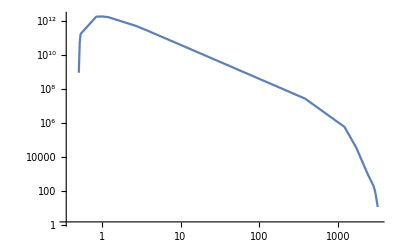

```mathematica
lifetimelistp01={0.0018,0.0019,0.002,0.005,0.007,0.01,0.05,0.1,1,10,10^2,10^3,10^4,2*10^4,4*10^4,4.3*10^4,5.5*10^4,6*10^4,7*10^4};
ma=0.01;
falistp01=Sqrt[lifetimelistp01/LifetimeFinal[ma]]*1000;
naxionsp01={8.719707644255341*^8,5.493415815880862*^10,1.6637202185239188*^11,1.7249325661865913*^12,1.774933861163792*^12,1.623382850961594*^12,5.009367405132962*^11,2.5893607834998438*^11,2.6247540768278763*^10,2.624832554196676*^9,2.624832554196675*^8,2.6248325541966736*^7,570216.5616884338,33588.31384567157,824.0123723821297,602.2681791497291,185.49196261415904,91.55693026468106,11.21105268547115};
ListLogLogPlot[Transpose@{falistp01,naxionsp01},Joined->True]
```

#### m_a=0.05 GeV

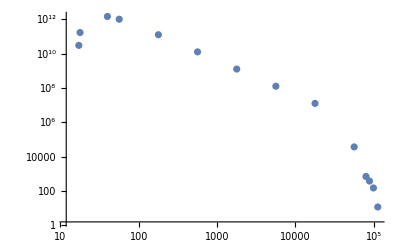

```mathematica
lifetimelistp05={0.0093,0.01,0.05,0.1,1,10,10^2,10^3,10^4,10^5,2*10^5,2.46*10^5,3.1*10^5,4*10^5};
ma=0.05;
falistp05=(alphaEM[ma](c2+5/3c1))/Sqrt[256 Pi^3] ma^(3/2)Sqrt[lifetimelistp05/(0.198*10^(-15))];
naxionsp05={3.054636846917804*^10,1.7044873605801343*^11,1.4743815669018157*^12,1.019851604080447*^12,1.2726838958998334*^11,1.2769451143012838*^10,1.2769451143012831*^9,1.2769451143012844*^8,1.2769451143012842*^7,37404.028190508514,710.2030669083892,384.9339116034629,152.7318423458901,11.895834707124543};
ListLogLogPlot[Transpose@{falistp05,naxionsp05}]
```

#### m_a=0.1 GeV

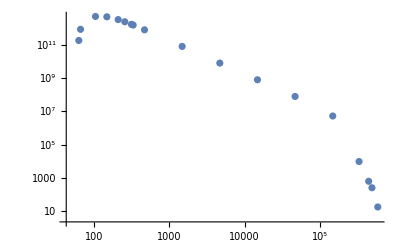

```mathematica
lifetimelistp1={0.018,0.02,0.05,0.1,0.2,0.3,0.45,0.5,1,10^1,10^2,10^3,10^4,10^5,5*10^5,9*10^5,1.1*10^6,1.57*10^6};
ma=0.1;
falistp1=(alphaEM[ma]cgamma[ma])/Sqrt[256 Pi^3] ma^(3/2)Sqrt[lifetimelistp1/(0.198*10^(-15))];
naxionsp1={1.7597134494159378*^11,8.206663632276146*^11,4.843371308592447*^12,4.613008820668906*^12,3.1430081946068115*^12,2.329540659126807*^12,1.6323741852582026*^12,1.4795030786889414*^12,7.659552723457737*^11,7.766095374122374*^10,7.766095374122374*^9,7.766095374122374*^8,7.766095374122378*^7,5.232108006963424*^6,9790.405736750487,639.8957997876139,261.7755544585693,18.43256393131094};
ListLogLogPlot[Transpose@{falistp1,naxionsp1}]
```

#### m_a=0.13 GeV

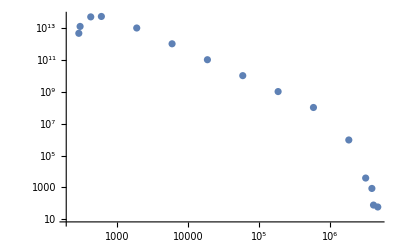

```mathematica
lifetimelistp13={0.023,0.025,0.05,0.1,1,10^1,10^2,10^3,10^4,10^5,10^6,3*10^6,4.5*10^6,5*10^6,6.6*10^6};
ma=0.13;
falistp13=(alphaEM[ma]cgamma[ma])/Sqrt[256 Pi^3] ma^(3/2)Sqrt[lifetimelistp13/(0.198*10^(-15))];
naxionsp13={4.746946890122031*^12,1.2835427695322375*^13,5.103242336694437*^13,5.427994121756811*^13,1.0229681229464758*^13,1.0426851956109772*^12,1.0426851956109769*^11,1.0426851956109772*^10,1.0426851956109776*^9,1.0426851956109776*^8,951058.7991112358,3866.0926793139665,859.1317065142151,77.70802738278059,58.86971771422769};
ListLogLogPlot[Transpose@{falistp13,naxionsp13}]
```

#### m_a=0.14 GeV

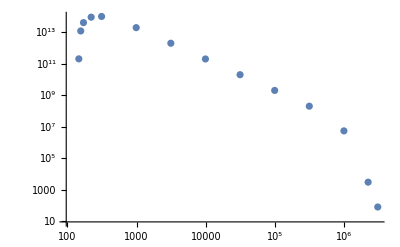

```mathematica
lifetimelistp14={0.022,0.025,0.03,0.05,0.1,1,10^1,10^2,10^3,10^4,10^5,10^6,5*10^6,9.5*10^6};
ma=0.14;
falistp14=(alphaEM[ma]Abs[cgamma[ma]])/Sqrt[256 Pi^3] ma^(3/2)Sqrt[lifetimelistp14/(0.198*10^(-15))];
naxionsp14={2.0282721288720227*^11,1.201818845427636*^13,4.07002160727426*^13,9.057648086006719*^13,1.0034453271752544*^14,1.95287036756305*^13,1.9957905954215789*^12,1.9957905954215784*^11,1.9957905954215782*^10,1.9957905954215782*^9,1.9957905954215792*^8,5.379828560887976*^6,2960.0157143812803,78.28418743014817};
ListLogLogPlot[Transpose@{falistp14,naxionsp14}]
```

#### m_a=0.16 GeV

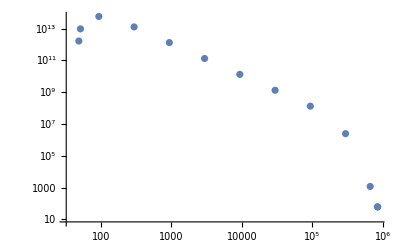

```mathematica
lifetimelistp16={0.027,0.03,0.1,1,10^1,10^2,10^3,10^4,10^5,10^6,5*10^6,8*10^6,8.2*10^6};
ma=0.16;
falistp16=(alphaEM[ma]Abs[cgamma[ma]])/Sqrt[256 Pi^3] ma^(3/2)Sqrt[lifetimelistp16/(0.198*10^(-15))];
naxionsp16={1.661875160073579*^12,9.656939788862342*^12,5.854153953823976*^13,1.2864214336920867*^13,1.324561468615775*^12,1.3249028755780077*^11,1.3249028755780073*^10,1.3249028755780075*^9,1.3249028755780075*^8,2.455203782683485*^6,1170.5381562257382,60.96552897009054,59.478564848868814};
ListLogLogPlot[Transpose@{falistp16,naxionsp16}]
```

#### m_a=0.4 GeV

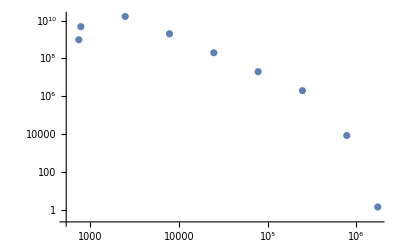

```mathematica
lifetimelistp4={0.09,0.1,1,10^1,10^2,10^3,10^4,10^5,5*10^5};
ma=0.4;
falistp4=(alphaEM[ma]Abs[cgamma[ma]])/Sqrt[256 Pi^3] ma^(3/2)Sqrt[lifetimelistp4/(0.198*10^(-15))];
naxionsp4={9.726350417558188*^8,4.755196233804509*^9,1.644659914250326*^10,2.0073456301172576*^9,2.0152091371497568*^8,2.0152091371497575*^7,2.015209137149757*^6,8724.041764358972,1.483680572169893};
ListLogLogPlot[Transpose@{falistp4,naxionsp4}]
```

#### Summary

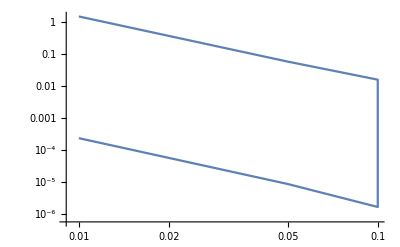

```mathematica
ListLogLogPlot[{{0.01,1/falistp01[[1]]},{0.05,1/falistp05[[1]]},{0.1,1/falistp1[[1]]},{0.1,1/falistp1[[-1]]},{0.05,1/falistp05[[-1]]},{0.01,1/falistp01[[-1]]}},Joined->True]
```

```mathematica
faser1=Import["/Volumes/GoogleDrive/My Drive/GoodNotes/ALP DUNE/constraints/FASER.csv","Data"];
faser2=Import["/Volumes/GoogleDrive/My Drive/GoodNotes/ALP DUNE/constraints/FASER2.csv","Data"];
```

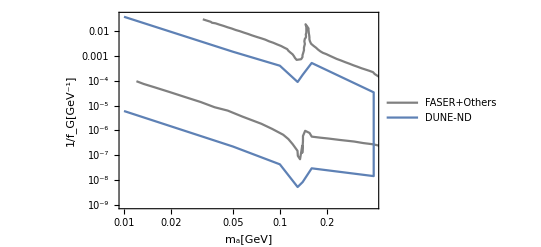

```mathematica
Show[ListLogLogPlot[{faser1,faser2},PlotStyle->{Gray,Gray},Joined->True,PlotRange->{{0.01,0.40},{10^-9,4*10^-2}},Frame->True,FrameLabel->{"m_a[GeV]","1/f_G[GeV^-1]"},PlotLegends->Placed[{"FASER+Others"},{0.24,0.2}]],ListLogLogPlot[{{0.01,1/falistp01[[1]]/(4 Pi^2)},{0.05,1/falistp05[[1]]/(4 Pi^2)},{0.1,1/falistp1[[1]]/(4 Pi^2)},{0.13,1/falistp13[[1]]/(4 Pi^2)},{0.14,1/falistp14[[1]]/(4 Pi^2)},{0.16,1/falistp16[[1]]/(4 Pi^2)},{0.4,1/falistp4[[1]]/(4 Pi^2)},{0.4,1/falistp4[[-1]]/(4 Pi^2)},{0.16,1/falistp16[[-1]]/(4 Pi^2)},{0.14,1/falistp14[[-1]]/(4 Pi^2)},{0.13,1/falistp13[[-1]]/(4 Pi^2)},{0.1,1/falistp1[[-1]]/(4 Pi^2)},{0.05,1/falistp05[[-1]]/(4 Pi^2)},{0.01,1/falistp01[[-1]]/(4 Pi^2)}},Joined->True,PlotLegends->Placed[{"DUNE-ND"},{0.2,0.1}]]]
```

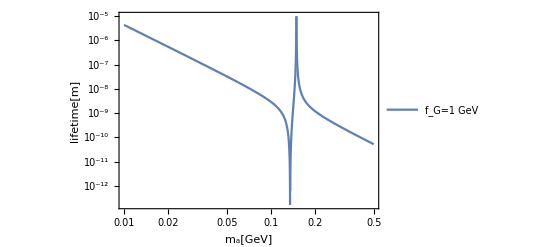

```mathematica
LogLogPlot[LifetimePhoton[ma,1/(4 Pi^2)],{ma,10^-2,0.5},Frame->True,FrameLabel->{"m_a[GeV]","lifetime[m]"},PlotLegends->Placed[{"f_G=1 GeV"},{0.2,0.2}]]
```

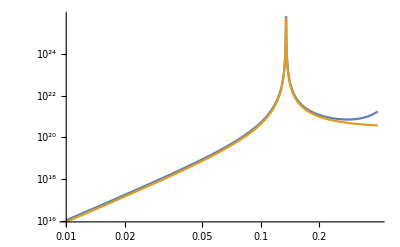

```mathematica
LogLogPlot[{Naxions[ma,1/(4 Pi^2),Length[decayprob]/Length[pi0]],NPOT*2.89*(1/6 ma^2/(ma^2-mPi^2)fpi/(1/(4 Pi^2)))^2*Length[decayprob]/Length[pi0]},{ma,0.01,0.4}]
```